### Initial Graphs

#### Full Matrix

```mathematica
init=({{0, 1}, {1, 0}});
```

```mathematica
inittri=({{0, 1, 1}, {1, 0, 1}, {1, 1, 0}});
```

#### “Sparse” Matrix

```mathematica
sparseinit={{2},{1}};
```

```mathematica
sparseinittri={{2,3},{1,3},{1,2}};
```

### Visualization and Classification of Graphs

#### Leaves, Hubs and Cores - “Sparse”

```mathematica
sparsenucleus[mat_]:=Length[DeleteElements[Map[Length,mat],{1}]]/Length[mat];
```

```mathematica
LHCs[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
{leaves,hubs,cores}];
```

```mathematica
LHCsf[mat_]:=Module[{LHCmat},
LHCmat=LHCs[mat];
Map[Length,LHCmat]/Length[mat]];
```

```mathematica
LHCsD[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
{{leaves,hubs,cores},Map[Extract[degrees,Transpose[{#}]]&,{leaves,hubs,cores}]}];
```

```mathematica
LHCsDo[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
Map[Extract[degrees,Transpose[{#}]]&,{leaves,hubs,cores}]];
```

```mathematica
LHCsDonL[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]];
```

```mathematica
LHCsDonL[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]];
```

```mathematica
LHCsDonLJ[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
Flatten[Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]]];
```

```mathematica
LHCsDonLN[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,degrees},
vertlist=Range[Length[mat]];
leaves=Pick[vertlist,Map[(Length[#]==1)&,mat]];
subgraphhubs=Delete[mat,Transpose[{leaves}]];
For[j=1,j<=Length[leaves],j++,
subgraphhubs=DeleteCases[subgraphhubs,leaves[[j]],2]];
hubs=If[vertlist==leaves,{},Flatten[Union[Part[mat,leaves]]]];
cores=Complement[vertlist,leaves,hubs];
degrees=Map[Length,mat];
Join[{{Length[mat],Length[mat]-Length[leaves],2(Length[mat]-1)-Length[leaves]}},Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]]];
```

```mathematica
LHCSstyle[mat_]:=Module[{leaves,hubs,cores},
{leaves,hubs,cores}=LHCs[mat];
{Style[leaves,Green],Style[hubs,Red],Style[cores,Blue]}];
```

```mathematica
LHCslist[{matlist_,titlelist_}]:=Map[LHCs,matlist];
```

```mathematica
LHCSsizelist[{matlist_,titlelist_}]:=Transpose[{Map[Length,Map[LHCs,matlist],{2}],titlelist}];
```

#### Graphs Visualization

```mathematica
grphps[mat_,p_]:=HighlightGraph[AdjacencyGraph[spar[mat],GraphLayout->"SpringElectricalEmbedding",PlotLabel->p,VertexSize->Medium],LHCSstyle[mat]];
```

```mathematica
grphslist[{matlist_,titlelist_}]:=MapThread[grphps,{matlist,titlelist}];
```

```mathematica
grphslistsort[{matlist_,problist_}]:=Module[{transp,matsor,probsort},
transp=Transpose[{matlist,problist}];
{matsor,probsort}=Transpose[ReverseSortBy[transp,Last]];
MapThread[grphps,{matsor,probsort}]];
```

```mathematica
spar[mat_]:=Module[{vertlist},
vertlist=Flatten[Table[Map[{j,#}&,mat[[j]]],{j,1,Length[mat]}],1];
SparseArray[Map[(#->1)&,vertlist]]];
```

```mathematica
sparsenext[mat_]:=Module[{size,node,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
neighbors=mat[[node]];
attach=RandomChoice[neighbors];
newmat=Append[mat,{attach}];
newmat[[attach]]=Append[newmat[[attach]],size+1];
newmat
];
```

```mathematica
Timing[nuclscdt=Table[Log[Map[sparsenucleus,NestList[sparsenext,sparseinit,2000]]],25];]
```

{488.751,Null}

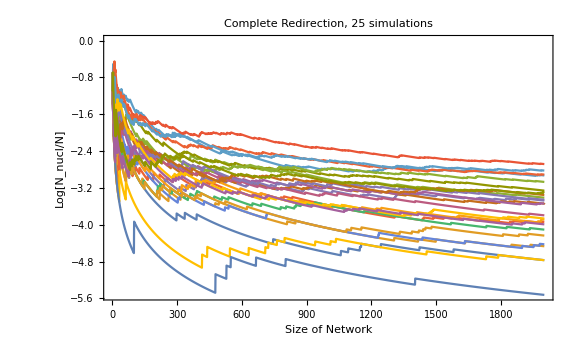

```mathematica
ListLinePlot[nuclscdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Redirection, 25 simulations"]
```

```mathematica
Timing[nuclscdt2=Table[Log[Map[sparsenucleus,NestList[sparsenext,sparseinit,5000]]],25];]
```

{6714.16,Null}

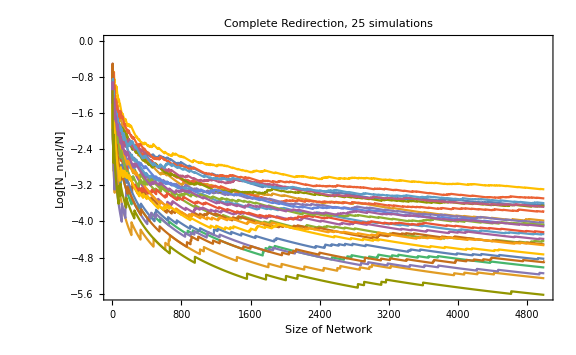

```mathematica
ListLinePlot[nuclscdt2,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Redirection, 25 simulations"]
```

```mathematica
sparsengnext[mat_]:=Module[{size,node,leaves,hubs,cores,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
{leaves,hubs,cores}=LHCs[mat];
If[size==2,neighbors=Complement[{1,2},{node}],
neighbors=Flatten[Pick[{hubs,Complement[Range[size],{node}],Complement[Join[hubs,cores],{node}]},
Map[MemberQ[#,node]&,{leaves,hubs,cores}]]]];
attach=RandomChoice[neighbors];
newmat=Append[mat,{attach}];
newmat[[attach]]=Append[newmat[[attach]],size+1];
newmat
];
```

```mathematica
Timing[nuclscfdt=Table[Log[Map[sparsenucleus,NestList[sparsengnext,sparseinit,2000]]],25];]
```

{1902.28,Null}

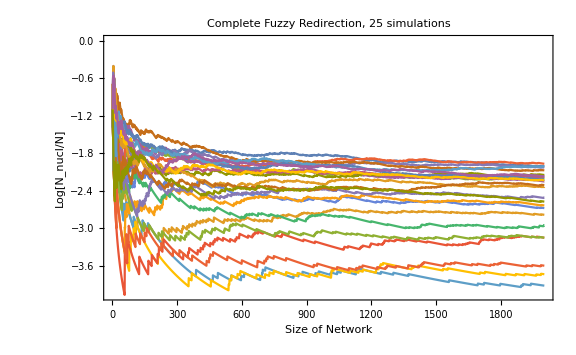

```mathematica
ListLinePlot[nuclscfdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Fuzzy Redirection, 25 simulations"]
```

```mathematica
Timing[nuclscfdt2=Table[Log[Map[sparsenucleus,NestList[sparsengnext,sparseinit,5000]]],25];]
```

{26155.8,Null}

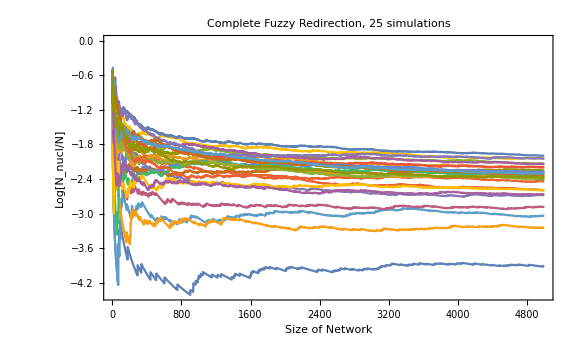

```mathematica
ListLinePlot[nuclscfdt2,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Fuzzy Redirection, 25 simulations"]
```

```mathematica
sparsenrnext[mat_]:=Module[{size,node,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
attach=node;
newmat=Append[mat,{attach}];
newmat[[attach]]=Append[newmat[[attach]],size+1];
newmat
];
```

```mathematica
Timing[nuclsnrdt=Table[Log[Map[sparsenucleus,NestList[sparsenrnext,sparseinit,2000]]],25];]
```

{312.429,Null}

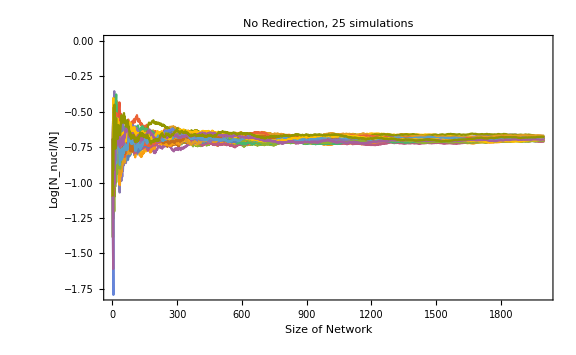

```mathematica
ListLinePlot[nuclsnrdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"No Redirection, 25 simulations"]
```

```mathematica
sparsemixrnext[mat_,pr_]:=Module[{size,node,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
neighbors=mat[[node]];
attach=RandomChoice[{1-pr,pr}->{node,RandomChoice[neighbors]}];
newmat=Append[mat,{attach}];
newmat[[attach]]=Append[newmat[[attach]],size+1];
newmat
];
```

```mathematica
Timing[nuclsmixrdt050=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.5]&,sparseinit,2000]]],25];]
```

{365.457,Null}

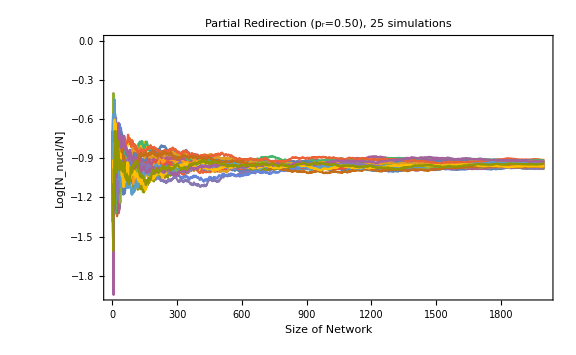

```mathematica
ListLinePlot[nuclsmixrdt050,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.50), 25 simulations"]
```

```mathematica
Timing[nuclsmixrdt070=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.7]&,sparseinit,2000]]],25];]
```

{398.666,Null}

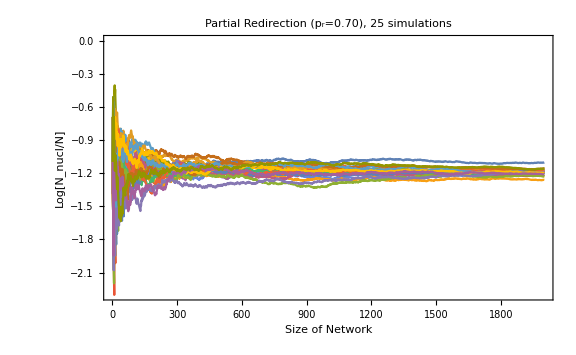

```mathematica
ListLinePlot[nuclsmixrdt070,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.70), 25 simulations"]
```

```mathematica
Timing[nuclsmixrdt080=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.8]&,sparseinit,2000]]],25];]
```

{422.198,Null}

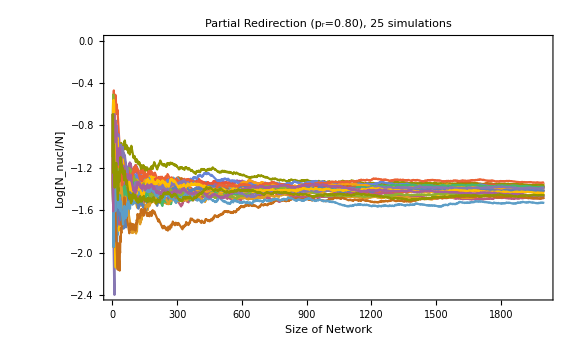

```mathematica
ListLinePlot[nuclsmixrdt080,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.80), 25 simulations"]
```

```mathematica
Timing[nuclsmixrdt090=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.9]&,sparseinit,2000]]],25];]
```

{455.035,Null}

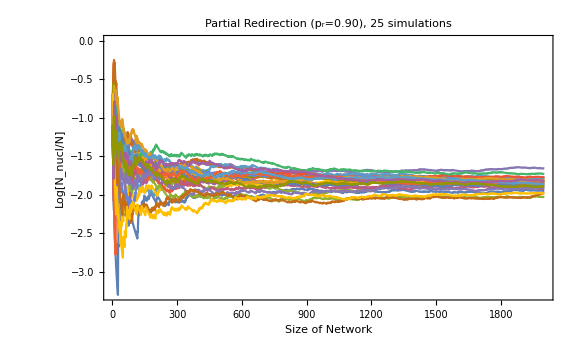

```mathematica
ListLinePlot[nuclsmixrdt090,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.90), 25 simulations"]
```

```mathematica
Timing[nuclsmixrdt095=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.95]&,sparseinit,5000]]],25];]
```

{6732.28,Null}

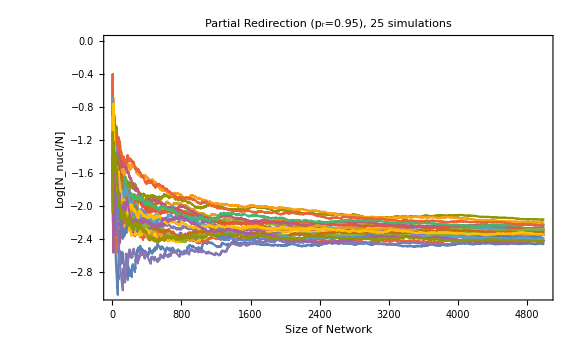

```mathematica
ListLinePlot[nuclsmixrdt095,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.95), 25 simulations"]
```

```mathematica
Timing[nuclsmixrdt099=Table[Log[Map[sparsenucleus,NestList[sparsemixrnext[#,0.99]&,sparseinit,5000]]],25];]
```

{6794.14,Null}

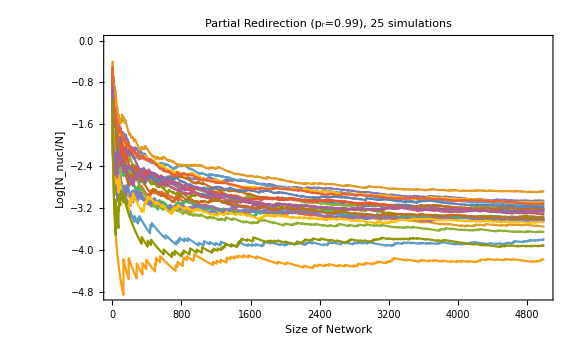

```mathematica
ListLinePlot[nuclsmixrdt099,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Partial Redirection (p_r=0.99), 25 simulations"]
```

```mathematica
fnuclsmixrdt[pr_,size_:1000,runs_:200]:=Table[{pr,Log[sparsenucleus[Nest[sparsemixrnext[#,pr]&,sparseinit,size]]]},runs];
```

```mathematica
Timing[datahist=Flatten[Table[fnuclsmixrdt[pr],{pr,0,1,0.01}],1];]
```

{315.767,Null}

```mathematica
Histogram3D[datahist,{{0.01},{0.1}},"Probability",PlotRange->All,
ImageSize->Large,AxesLabel->{"pr","Log[N_nucl/N]","Freq"}]
```

-Graphics3D-

```mathematica
Timing[datahist09=Flatten[Table[fnuclsmixrdt[pr,5000],{pr,0.95,1,0.001}],1];]
```

{2625.,Null}

```mathematica
Histogram3D[datahist09,{{0.001},{0.1}},"Probability",PlotRange->All,
ImageSize->Large,AxesLabel->{"pr","Log[N_nucl/N]","Freq"}]
```

-Graphics3D-

#### Leaves, Hubs and Cores

```mathematica
LHC[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
{leaves,hubs,cores}];
```

```mathematica
LHCf[mat_]:=Module[{LHCmat},
LHCmat=LHC[mat];
Map[Length,LHCmat]/Length[mat]];
```

```mathematica
LHCD[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores,degrees},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
degrees=Map[Total,mat];
{{leaves,hubs,cores},Map[Extract[degrees,Transpose[{#}]]&,{leaves,hubs,cores}]}];
```

```mathematica
LHCDo[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores,degrees},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
degrees=Map[Total,mat];
Map[Extract[degrees,Transpose[{#}]]&,{leaves,hubs,cores}]];
```

```mathematica
LHCDonL[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores,degrees},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
degrees=Map[Total,mat];
Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]];
```

```mathematica
LHCDonLJ[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores,degrees},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
degrees=Map[Total,mat];
Flatten[Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]]];
```

```mathematica
LHCDonLN[mat_]:=Module[{vertlist,leaves,hubs,cores,subgraphhubs,newvertlist,subgraphcores,degrees},
vertlist=VertexList[AdjacencyGraph[mat]];
leaves=Pick[vertlist,VertexDegree[AdjacencyGraph[mat]],1];
subgraphhubs=VertexDelete[AdjacencyGraph[mat],leaves];
hubs=If[vertlist==leaves,{},Flatten[Union[Map[Pick[vertlist,mat[[#]],1]&,leaves]]]];
subgraphcores=VertexDelete[subgraphhubs,hubs];
cores=VertexList[subgraphcores];
degrees=Map[Total,mat];
Join[{{Length[mat],Length[mat]-Length[leaves],2(Length[mat]-1)-Length[leaves]}},Map[Extract[degrees,Transpose[{#}]]&,{hubs,cores}]]];
```

```mathematica
LHC[({{0, 0, 1}, {0, 0, 1}, {1, 1, 0}})]
```

{{1,2},{3},{}}

```mathematica
LHCf[({{0, 0, 1}, {0, 0, 1}, {1, 1, 0}})]
```

{2/3,1/3,0}

```mathematica
LHC[{{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0},{0,1,0,0,0,0,1,0},{0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1},{0,0,1,0,0,1,1,0}}]
```

{{1,2,3},{4,5,8},{6,7}}

```mathematica
LHCDonLN[{{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0},{0,1,0,0,0,0,1,0},{0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1},{0,0,1,0,0,1,1,0}}]
```

{{8,5,11},{2,2,3},{2,2}}

```mathematica
LHCDonLJ[{{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0},{0,1,0,0,0,0,1,0},{0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1},{0,0,1,0,0,1,1,0}}]
```

{2,2,3,2,2}

Leaves are green and connect to hubs, hubs are red and have leaves, cores are blue because they don’t

```mathematica
LHCstyle[mat_]:=Module[{leaves,hubs,cores},
{leaves,hubs,cores}=LHC[mat];
{Style[leaves,Green],Style[hubs,Red],Style[cores,Blue]}];
```

```mathematica
LHClist[{matlist_,titlelist_}]:=Map[LHC,matlist];
```

```mathematica
LHCsizelist[{matlist_,titlelist_}]:=Transpose[{Map[Length,Map[LHC,matlist],{2}],titlelist}];
```

#### Graphs Visualization

```mathematica
grph[mat_]:=AdjacencyGraph[mat,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"];
```

```mathematica
grphp[mat_,p_]:=HighlightGraph[AdjacencyGraph[mat,GraphLayout->"SpringElectricalEmbedding",PlotLabel->p,VertexSize->Medium],LHCstyle[mat]];
```

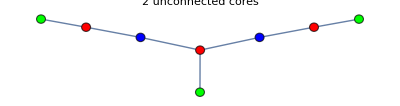

```mathematica
grphp[{{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0},{0,1,0,0,0,0,1,0},{0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1},{0,0,1,0,0,1,1,0}},"2 unconnected cores"]
```

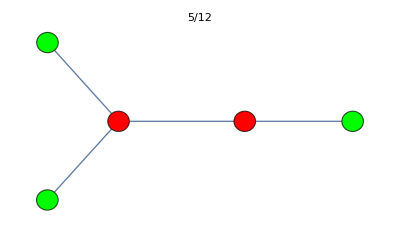
```mathematica
Normal[AdjacencyMatrix[-Graphics-]]
```

{{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,1},{1,0,0,0,1},{0,1,1,1,0}}

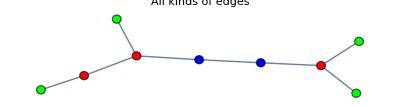

```mathematica
grphp[{{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,1,0},{0,0,0,0,1,0,0,0,1},{0,1,0,0,0,0,0,1,0},{1,0,0,0,1,0,1,0,0},{0,0,1,1,0,1,0,0,0}},"All kinds of edges"]
```

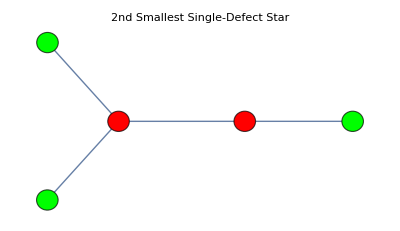

```mathematica
grphp[{{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,1},{1,0,0,0,1},{0,1,1,1,0}},"2nd Smallest Single-Defect Star"]
```

```mathematica
grphlist[{matlist_,titlelist_}]:=MapThread[grphp,{matlist,titlelist}];
```

```mathematica
grphlistsort[{matlist_,problist_}]:=Module[{transp,matsor,probsort},
transp=Transpose[{matlist,problist}];
{matsor,probsort}=Transpose[ReverseSortBy[transp,Last]];
MapThread[grphp,{matsor,probsort}]];
```

#### Degrees and Nucleus, different function for leaves

```mathematica
degrees[mat_]:=Sort[Tally[Map[Total,mat]]];
```

```mathematica
nucleus[mat_]:=Length[DeleteElements[Map[Total,mat],{1}]]/Length[mat];
```

```mathematica
griddegrees[mat_]:=Grid[Sort[Tally[Map[Total,mat]]]];
```

```mathematica
leavesc[mat_]:=Last[First[Sort[Tally[Map[Total,mat]]]]]/Length[mat];
```

```mathematica
leaveslist[{matlist_,titlelist_}]:=MapThread[{leavesc[#1],#2}&,{matlist,titlelist}];
```

### Iterate Graphs

#### Canonical Graphs

```mathematica
canon[mat_]:=Normal[AdjacencyMatrix[CanonicalGraph[AdjacencyGraph[mat]]]];
```

#### Update Graphs (next iteration is random)

```mathematica
next[mat_]:=Module[{size,node,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
neighbors=Pick[Range[size],mat[[node]],1];
attach=RandomChoice[neighbors];
newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[attach,size+1]]=1;
newmat[[size+1,attach]]=1;
canon[newmat]
];
```

```mathematica
ngnext[mat_]:=Module[{size,node,leaves,hubs,cores,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
{leaves,hubs,cores}=LHC[mat];
If[size==2,neighbors=Complement[{1,2},{node}],
neighbors=Flatten[Pick[{hubs,Complement[Range[size],{node}],Complement[Join[hubs,cores],{node}]},
Map[MemberQ[#,node]&,{leaves,hubs,cores}]]]];
attach=RandomChoice[neighbors];
newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[attach,size+1]]=1;
newmat[[size+1,attach]]=1;
canon[newmat]
];
```

```mathematica
nrnext[mat_]:=Module[{size,node,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
attach=node;
newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[attach,size+1]]=1;
newmat[[size+1,attach]]=1;
canon[newmat]
];
```

```mathematica
mixrnext[mat_,pr_]:=Module[{size,node,neighbors,attach,newmat},
size=Length[mat];
node=RandomInteger[{1,size}];
neighbors=Pick[Range[size],mat[[node]],1];
attach=RandomChoice[{1-pr,pr}->{node,RandomChoice[neighbors]}];
newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[attach,size+1]]=1;
newmat[[size+1,attach]]=1;
canon[newmat]
];
```

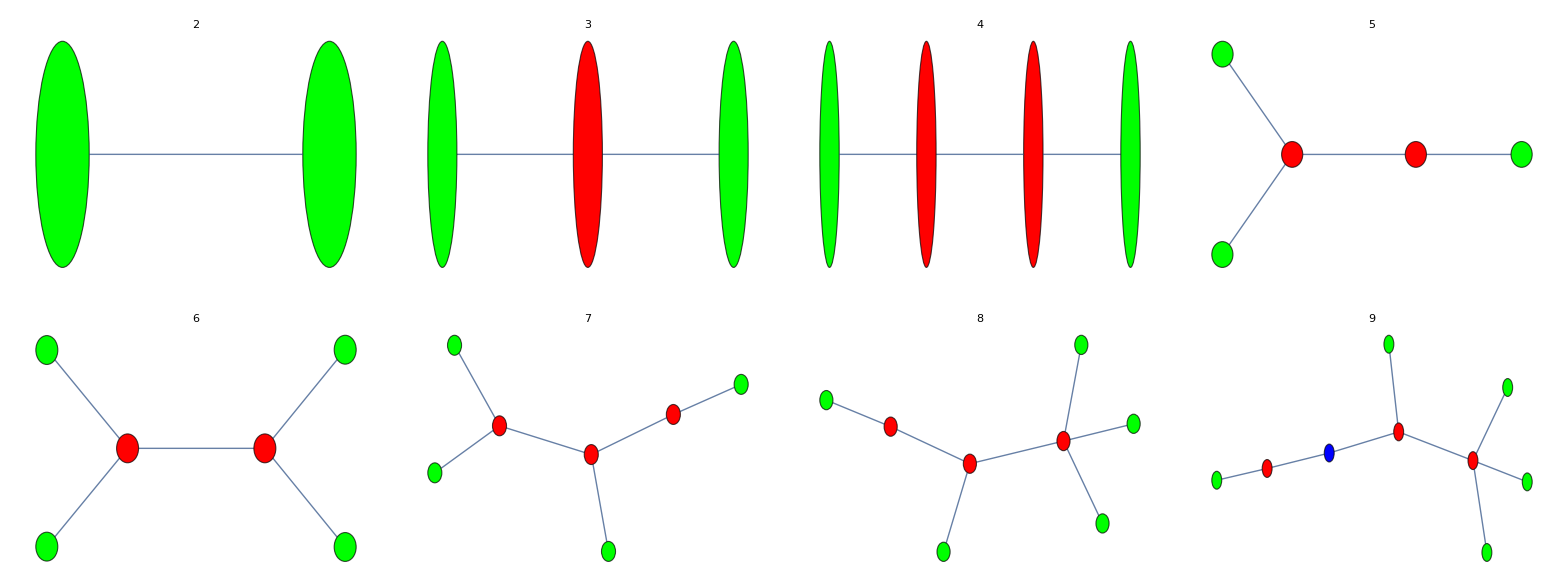

```mathematica
Grid[Partition[grphlist[{NestList[next,init,7],Range[2,9]}],4]]
```

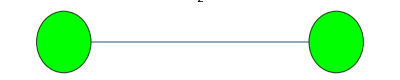
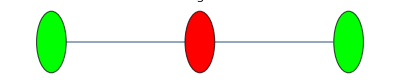
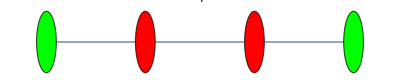
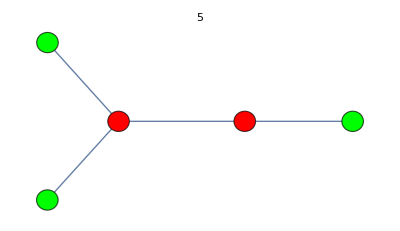
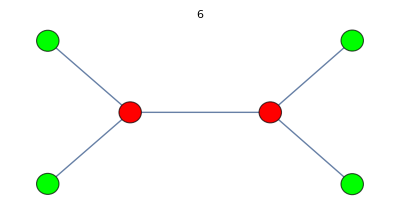
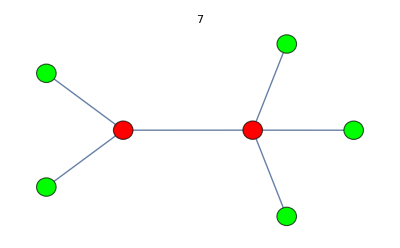
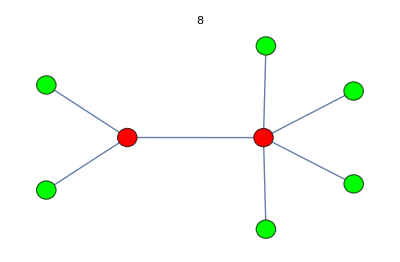
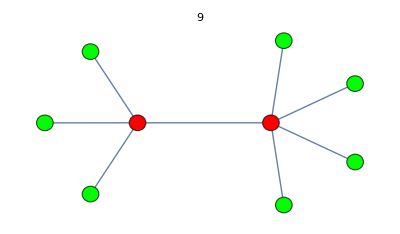

```mathematica
grphlist[{NestList[ngnext,init,10],Range[2,2+10]}]
```

```mathematica
Timing[nonlcd=Map[LHCDonL,Table[Nest[next,init,100],500]];]
```

{129.339,Null}

```mathematica
Map[Last,nonlcd]
```

{{},{2},{2,2,2,2},{2},{2},{2},{2,2,2},{},{2},{2,2},{2},{2,2},{2,2,2,3},{2},{},{2,2,2,3,3},{2},{},{2,2,2},{2,2},{2,2},{2,2,2},{},{2,2,2,2,2,2},{},{},{2,2},{},{2,2},{},{2,2},{2,3},{2,2},{2,3},{},{2,2},{},{2,2,3},{},{2,2,2},{2},{2,2},{2,3},{2},{2},{},{2,3},{},{},{2},{4},{2,2,2},{2},{},{2,2,2},{2,2},{2,2},{2,2},{2,2,2},{2,2},{2,2},{},{2},{2,2,2},{2},{2},{2,2},{},{2},{3},{2,2,2},{},{2},{2,2,2,2},{2,2},{2,2,3},{2,2},{2},{2},{2},{2,2,3},{2,2},{2,2},{2,2,2},{2},{2},{2,2},{2},{3},{2},{2,2,2,2,2},{2},{2,2,2,2,2},{2,2},{2,2},{2,2,2},{},{2},{2,4},{},{2,2,2,2},{},{},{2},{2,2,5},{2,2},{},{2,2,2},{},{2,2},{2,2,2,2,2},{},{2,2,2,3},{},{2},{2,2,2,2},{2,2,2},{2,2,2,3},{2,2,2},{2,2,2},{2,2},{2,2,2},{2,2,2,2,3,3},{2,2},{2,2,2},{2,2},{2,2,2},{2},{2},{2},{2,3},{2},{2,2,2,2},{2,2,2,3},{2},{2},{3},{},{2},{2,2},{},{2,2},{3},{},{2,2,2},{2,2,2},{4},{2},{},{},{2},{2,2},{2,2},{},{2},{},{2},{2,2},{2,2,3},{2,2,2,2},{2,2,2,2},{2},{2,2,2},{2},{},{},{2},{},{2},{2},{},{2,2,2,3},{},{},{3},{2},{2},{2,2,2},{2,2,4},{2,2},{2},{},{2},{2,2,2},{2},{2,2},{2,2,2},{2,2},{2},{2},{2,2,3},{2},{2,2,2},{2,2},{2,2,2,3,3},{2},{2,2,2},{},{},{},{2},{2},{},{2,3,3,3},{},{2,2},{2,2,2,2,2},{2},{2,2,2,2},{2},{2,2,2,2,2},{2,2,2,2,2,3},{2,2},{},{2},{2},{2,2},{2},{},{2,2},{},{2},{2,2},{2,2,2},{2,2},{},{2},{2,2},{2,2},{2},{},{2},{2},{2,3,3},{2,2,2},{2},{2,2},{},{2,2},{2},{2,2},{2},{},{2,2,3},{},{2,3},{2},{},{2},{2,2,2},{2},{2,2},{2},{},{},{},{2,3},{2},{2,2},{},{2,2,2},{2},{2,2},{},{},{2},{},{2},{2,2},{2},{2,2,2},{2,2,2},{2,2,2},{2},{2,4},{2,2,3},{},{},{},{2},{},{2,2},{},{2},{},{},{2},{},{2},{3},{2,2},{2,2,2,2},{2,2,2,2},{2,2,2,2},{2,2},{},{2},{},{2,2,2,2,2},{2,2,2},{2,2},{2,2,2,3,4},{},{},{2},{2},{2,2},{2,2,2,3},{2,2},{2,2},{},{2,2},{},{2},{2,2,2},{2,2,2},{2,2},{},{2},{2,2,3},{2,2,2},{2,2},{2,2,2},{2,2},{2,2,2},{},{},{2,3},{2,2,2,2},{2,2},{2},{2},{2,2},{},{2},{2,3},{2,2,2},{2,2,2,2,2},{},{2,2},{},{2,2,2},{},{2,2,2},{2,2},{},{2},{2},{2,2,2,2,5},{},{2},{2,2,2,3},{2,2},{2,2,2,2},{},{3},{2,2},{3},{2,2,2},{2,3},{2,3},{2,3},{2,2,2},{},{2},{2,2},{2},{2},{},{},{2},{2,2,2},{2,2},{2,2},{2,2,2,2,2,4},{2,2,2,2},{},{2},{2,2,2,3},{},{3},{},{2,2},{2},{2,2},{2,2},{2,2,2,3},{},{},{},{2,3},{2,2},{2},{},{2},{2,2,2,2},{2,3,3},{2},{2},{2,2},{},{2,2,2,2,3},{2,2},{2},{2,2},{2,2,2},{2,2,2,2},{2,2},{2},{2,2,2,2,2,2},{2},{},{2,2,2},{2},{},{},{3},{2,2},{2,2},{2,2,2},{2,2},{2},{2},{2,2,2},{2},{},{},{2},{2},{2,2,2,2},{},{2,2},{2},{2,3},{},{},{2,2,2},{2},{2},{2},{2,2,2},{},{2,2},{},{2},{},{},{},{2},{2},{},{2,2,2},{2},{},{2,2},{},{2},{},{2,2},{2},{},{2,2,2,4},{3},{2,2},{2,2,2,3},{},{2,2},{},{2},{2,2,2,3},{2,3},{2,2,2},{3},{},{2},{2,2},{2},{2},{2,2,2,2,2,3},{},{2},{2},{2},{2},{2},{2,2,2,2,2,2},{},{},{},{},{2,2,2},{2,2,2,2,2,3},{},{2},{2,2,3},{2,3},{2},{},{2},{}}

```mathematica
Timing[nonlcdJ=Map[LHCDonLJ,Table[Nest[next,init,100],500]];]
```

{129.743,Null}

```mathematica
ReverseSortBy[Tally[Flatten[nonlcdJ]],Last]
```

{{2,1871},{3,810},{4,414},{5,237},{6,182},{7,134},{8,127},{9,102},{11,75},{10,68},{12,60},{15,49},{18,43},{14,43},{13,42},{17,41},{20,28},{19,24},{16,24},{23,22},{21,22},{25,21},{34,19},{24,19},{22,19},{26,17},{60,16},{41,16},{56,14},{39,14},{61,13},{31,13},{29,13},{27,13},{32,12},{30,12},{28,12},{53,11},{40,11},{45,10},{83,9},{75,9},{74,9},{63,9},{59,9},{46,9},{42,9},{35,9},{33,9},{91,8},{81,8},{71,8},{70,8},{69,8},{57,8},{36,8},{100,7},{94,7},{93,7},{89,7},{85,7},{79,7},{64,7},{62,7},{58,7},{54,7},{49,7},{43,7},{101,6},{80,6},{55,6},{52,6},{51,6},{44,6},{37,6},{95,5},{92,5},{87,5},{84,5},{82,5},{73,5},{72,5},{50,5},{47,5},{99,4},{96,4},{77,4},{68,4},{67,4},{65,4},{38,4},{98,3},{97,3},{88,3},{78,3},{66,3},{48,3},{90,2},{86,1},{76,1}}

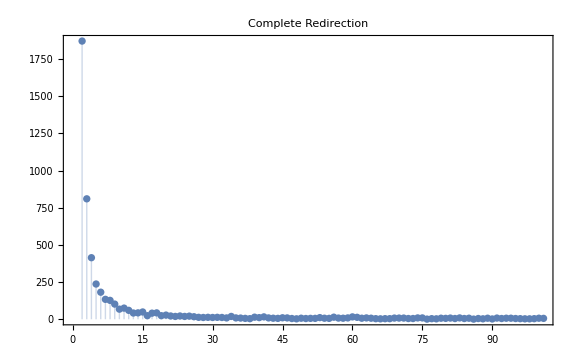

```mathematica
ListPlot[Tally[Flatten[nonlcdJ]],Filling->Axis,Frame->True,PlotRange->All,
ImageSize->Large,PlotLabel->"Complete Redirection"]
```

```mathematica
Timing[nonlcfdJ=Map[LHCDonLJ,Table[Nest[ngnext,init,100],500]];]
```

{460.315,Null}

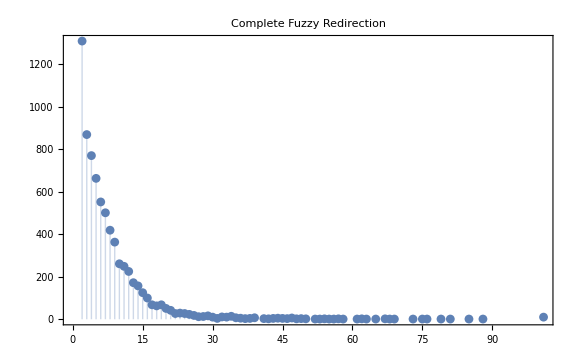

```mathematica
ListPlot[Tally[Flatten[nonlcfdJ]],Filling->Axis,Frame->True,PlotRange->All,
ImageSize->Large,PlotLabel->"Complete Fuzzy Redirection"]
```

```mathematica
Timing[nuclcd=Table[Log[nucleus[Nest[next,init,500]]],200];]
```

{1399.42,Null}

```mathematica
Timing[nuclcfd=Table[Log[nucleus[Nest[ngnext,init,500]]],200];]
```

{3098.75,Null}

```mathematica
PairedHistogram[nuclcd,nuclcfd,Frame->True,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
Timing[nuclcdt=Table[Log[Map[nucleus,NestList[next,init,2000]]],25];]
```

{10761.3,Null}

```mathematica
Timing[nuclcdt2=Table[Log[Map[nucleus,NestList[next,init,5000]]],20];]
```

$Aborted

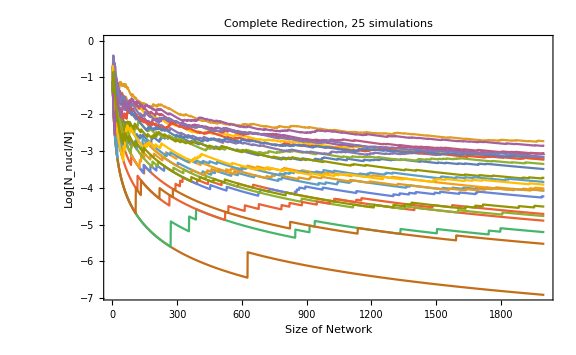

```mathematica
ListLinePlot[nuclcdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Redirection, 25 simulations"]
```

```mathematica
Timing[nuclcfdt=Table[Log[Map[nucleus,NestList[ngnext,init,2000]]],25];]
```

{8604.7,Null}

```mathematica
Timing[nuclcfdt2=Table[Log[Map[nucleus,NestList[ngnext,init,5000]]],20];]
```

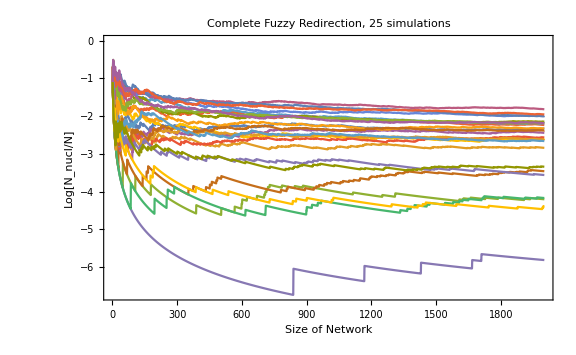

```mathematica
ListLinePlot[nuclcfdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"Complete Fuzzy Redirection, 25 simulations"]
```

```mathematica
Timing[nuclnrdt=Table[Log[Map[nucleus,NestList[nrnext,init,2000]]],25];]
```

{3321.76,Null}

```mathematica
ListLinePlot[nuclnrdt,
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Log[N_nucl/N]"},
PlotLabel->"No Redirection, 25 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[Rest[NestList[nrnext,init,1000]],20],{2}],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","N_nucl/N"},
PlotLabel->"20 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[Rest[NestList[mixrnext[#,1/2]&,init,1000]],20],{2}],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","N_nucl/N"},
PlotLabel->"20 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[Rest[NestList[mixrnext[#,1/4]&,init,1000]],20],{2}],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","N_nucl/N"},
PlotLabel->"20 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[Rest[NestList[mixrnext[#,3/4]&,init,1000]],20],{2}],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","N_nucl/N"},
PlotLabel->"20 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[Rest[NestList[mixrnext[#,1]&,init,1000]],20],{2}],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","N_nucl/N"},
PlotLabel->"20 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Map[nucleus,Table[NestList[next,inittri,100],50],{2}],Frame->True,PlotRange->All,ImageSize->Medium]
```

```mathematica
Map[Grid,NestList[sparsenext,{{2},{1}},5]]
```

{2
1,2 | 
1 | 3
2 | ,2 |  | 
1 | 3 | 4
2 |  | 
2 |  | ,2 |  |  | 
1 | 3 | 4 | 5
2 |  |  | 
2 |  |  | 
2 |  |  | ,2 |  |  | 
1 | 3 | 4 | 5
2 | 6 |  | 
2 |  |  | 
2 |  |  | 
3 |  |  | ,2 |  |  | 
1 | 3 | 4 | 5
2 | 6 | 7 | 
2 |  |  | 
2 |  |  | 
3 |  |  | 
3 |  |  | }

```mathematica
ListLinePlot[Map[sparsenucleus,Table[NestList[sparsenext,sparseinit,1000],50],{2}],Frame->True,PlotRange->All,ImageSize->Medium]
```

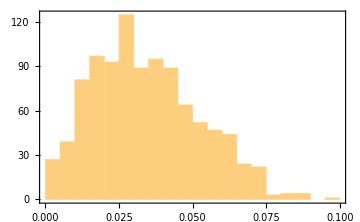

```mathematica
Histogram[Map[sparsenucleus,Table[Nest[sparsenext,sparseinit,1000],1000]],Frame->True,PlotRange->All,ImageSize->Medium]
```

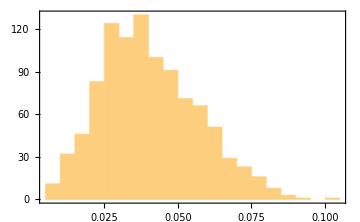

```mathematica
Histogram[Map[sparsenucleus,Table[Nest[sparsenext,sparseinittri,1000-1],1000]],Frame->True,PlotRange->All,ImageSize->Medium]
```

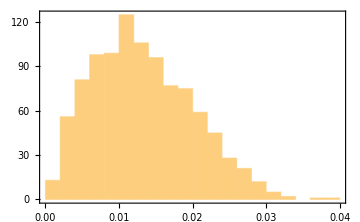

```mathematica
Histogram[Map[sparsenucleus,Table[Nest[sparsenext,sparseinit,10000],1000]],Frame->True,PlotRange->All,ImageSize->Medium]
```

```mathematica
Histogram[Map[sparsenucleus,Table[Nest[sparsenext,sparseinittri,10000-1],1000]],Frame->True,PlotRange->All,ImageSize->Medium]
```

-Graphics-

```mathematica
Timing[nustar100k=Map[sparsenucleus,Table[Nest[sparsenext,sparseinit,100000],10]]]
```

{844.662,{233/50001,88/50001,305/50001,893/100002,419/100002,220/50001,173/33334,86/16667,275/100002,440/50001}}

```mathematica
Timing[nutri100k=Map[sparsenucleus,Table[Nest[sparsenext,sparseinittri,100000-1],10]]]
```

{838.276,{190/50001,37/14286,295/100002,769/100002,485/100002,265/100002,430/50001,487/50001,132/16667,292/50001}}

```mathematica
ListLinePlot[{nustar100k,nutri100k}]
```

-Graphics-

```mathematica
nextj[mat_,node_]:=Module[{size,neighbors,attach,newmat,newmats},
size=Length[mat];
neighbors=Pick[Range[size],mat[[node]],1];
newmats=
Map[
(newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[#,size+1]]=1;
newmat[[size+1,#]]=1;
canon[newmat])&,neighbors];
newmats
];
```

```mathematica
ngnextj[mat_,node_]:=Module[{size,leaves,hubs,cores,neighbors,attach,newmat,newmats},
size=Length[mat];
{leaves,hubs,cores}=LHC[mat];
If[size==2,neighbors=Complement[{1,2},{node}],
neighbors=Flatten[Pick[{hubs,Complement[Range[size],{node}],Complement[Join[hubs,cores],{node}]},
Map[MemberQ[#,node]&,{leaves,hubs,cores}]]]];
newmats=
Map[
(newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[#,size+1]]=1;
newmat[[size+1,#]]=1;
canon[newmat])&,neighbors];
newmats
];
```

```mathematica
nrnextj[mat_,node_]:=Module[{size,neighbors,attach,newmat,newmats},
size=Length[mat];
newmat=Transpose[Append[Transpose[Append[mat,ConstantArray[0,size]]],ConstantArray[0,size+1]]];
newmat[[node,size+1]]=1;
newmat[[size+1,node]]=1;
{canon[newmat]}
];
```

```mathematica
nextall[mat_]:=Table[nextj[mat,j],{j,1,Length[mat]}];
```

```mathematica
ngnextall[mat_]:=Table[ngnextj[mat,j],{j,1,Length[mat]}];
```

```mathematica
nrnextall[mat_]:=Table[nrnextj[mat,j],{j,1,Length[mat]}];
```

```mathematica
nextalllist[mat_]:=Flatten[nextall[mat],1];
```

```mathematica
ngnextalllist[mat_]:=Flatten[ngnextall[mat],1];
```

```mathematica
nrnextalllist[mat_]:=Flatten[nrnextall[mat],1];
```

```mathematica
nextallprobs[mat_]:=Flatten[Map[ConstantArray[1/Length[#],Length[#]]&,nextall[mat]]/Length[mat]];
```

```mathematica
ngnextallprobs[mat_]:=Flatten[Map[ConstantArray[1/Length[#],Length[#]]&,ngnextall[mat]]/Length[mat]];
```

```mathematica
nrnextallprobs[mat_]:=Flatten[Map[ConstantArray[1/Length[#],Length[#]]&,nrnextall[mat]]/Length[mat]];
```

```mathematica
nestnext[{matlist_,problist_}]:={Flatten[Map[nextalllist,matlist],1],Flatten[problist Map[nextallprobs,matlist],1]};
```

```mathematica
ngnestnext[{matlist_,problist_}]:={Flatten[Map[ngnextalllist,matlist],1],Flatten[problist Map[ngnextallprobs,matlist],1]};
```

```mathematica
nrnestnext[{matlist_,problist_}]:={Flatten[Map[nrnextalllist,matlist],1],Flatten[problist Map[nrnextallprobs,matlist],1]};
```

```mathematica
mixnestnext[{matlist_,problist_},pr_]:=Module[{matlistrd,problistrd,matlistnr,problistnr},
{matlistrd,problistrd}=nestnext[{matlist,problist}];
{matlistnr,problistnr}=nrnestnext[{matlist,problist}];
{Join[matlistrd,matlistnr],Join[pr*problistrd,(1-pr)*problistnr]}];
```

```mathematica
collect[{matlist_,problist_}]:=Transpose[Map[{First[First[#]],Total[Last[Transpose[#]]]}&,GatherBy[Transpose[{matlist,problist}],First]]];
```

```mathematica
collectRS[{matlist_,problist_}]:=Transpose[ReverseSortBy[Map[{First[First[#]],Total[Last[Transpose[#]]]}&,GatherBy[Transpose[{matlist,problist}],First]],Last]];
```

```mathematica
nestnextcollected[{matlist_,problist_}]:=Module[{ans,t},t=Timing[ans=collect[nestnext[{matlist,problist}]]];Print[{Length[First[First[First[ans]]]],First[t]}];ans];
```

```mathematica
ngnestnextcollected[{matlist_,problist_}]:=Module[{ans,t},t=Timing[ans=collect[ngnestnext[{matlist,problist}]]];Print[{Length[First[First[First[ans]]]],First[t]}];ans];
```

```mathematica
nrnestnextcollected[{matlist_,problist_}]:=Module[{ans,t},t=Timing[ans=collect[nrnestnext[{matlist,problist}]]];Print[{Length[First[First[First[ans]]]],First[t]}];ans];
```

```mathematica
mixnestnextcollected[{matlist_,problist_},pr_]:=Module[{ans,t},t=Timing[ans=collect[mixnestnext[{matlist,problist},pr]]];Print[{Length[First[First[First[ans]]]],First[t]}];ans];
```

```mathematica
nestnext[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}}]
```

{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}},{1/3,1/3,1/6,1/6}}

```mathematica
nestnextcollected[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}}]
```

{4,0.002198}

{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}},{2/3,1/3}}

```mathematica
nrnestnext[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}}]
```

{{{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}}},{1/3,1/3,1/3}}

```mathematica
nrnestnextcollected[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}}]
```

{4,0.00178}

{{{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}}},{2/3,1/3}}

```mathematica
mixnestnext[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}},1/2]
```

{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}}},{1/6,1/6,1/12,1/12,1/6,1/6,1/6}}

```mathematica
mixnestnextcollected[{{{{0,0,1},{0,0,1},{1,1,0}}},{1}},1/2]
```

{4,0.003447}

{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}},{1/2,1/2}}

```mathematica
nextbranches[{matlist_,problist_}]:=Map[{grphlist[#],grphlist[collect[nestnext[#]]]}&,Map[{#}&,Transpose[{matlist,problist}],{2}]];
nextbranchescond[{matlist_,problist_}]:=Map[{grphlist[#],grphlist[collect[nestnext[#]]]}&,Map[{#}&,Transpose[{matlist,ConstantArray[1,Length[problist]]}],{2}]];
nextbranchescondLHC[{matlist_,problist_}]:=Map[{LHClist[#],LHClist[collect[nestnext[#]]]}&,Map[{#}&,Transpose[{matlist,ConstantArray[1,Length[problist]]}],{2}]];
nextbranchesLHCsize[{matlist_,problist_}]:=Map[{LHCsizelist[#],Transpose[collect[Transpose[LHCsizelist[collect[nestnext[#]]]]]]}&,Map[{#}&,Transpose[{matlist,problist}],{2}]];
nextbranchescondLHCsize[{matlist_,problist_}]:=Map[{LHCsizelist[#],Transpose[collect[Transpose[LHCsizelist[collect[nestnext[#]]]]]]}&,Map[{#}&,Transpose[{matlist,ConstantArray[1,Length[problist]]}],{2}]];
```

```mathematica
nextallbranches[{matlist_,problist_}]:=Map[{grphlist[#],grphlist[nestnext[#]]}&,Map[{#}&,Transpose[{matlist,problist}],{2}]];
nextallbranchesLHCsize[{matlist_,problist_}]:=Map[{LHCsizelist[#],LHCsizelist[collect[nestnext[#]]]}&,Map[{#}&,Transpose[{matlist,problist}],{2}]];
nextallbranchescond[{matlist_,problist_}]:=Map[{grphlist[#],grphlist[nestnext[#]]}&,Map[{#}&,Transpose[{matlist,ConstantArray[1,Length[problist]]}],{2}]];
```

```mathematica
nextallbrancheslist[{matlist_,problist_}]:=Map[{#,Transpose[nestnext[#]]}&,Map[{#}&,Transpose[{matlist,problist}],{2}]];
nextallbrancheslistcond[{matlist_,problist_}]:=Map[{#,Transpose[nestnext[#]]}&,Map[{#}&,Transpose[{matlist,ConstantArray[1,Length[problist]]}],{2}]];
```

```mathematica
sdstar[p_,n_]:=2/(n-1)1/n+If[n==4,2,1]p((n-3)/n+1/(2(n)));
```

```mathematica
Table[{2/(n-1)1/n,(n-3)/n,1/(2(n))},{n,3,6}]
```

{{1/3,0,1/6},{1/6,1/4,1/8},{1/10,2/5,1/10},{1/15,1/2,1/12}}

```mathematica
FoldList[sdstar,0,Range[3,8]]
```

{0,1/3,5/12,37/120,71/288,277/1344,545/3072}

```mathematica
RSolve[{a[n+1]==2/(n-1)1/n+((n-3)/n+1/(2(n)))a[n],a[5]==5/12},a[n], n]
```

{{a[n]→(8 (-5 √π (-2+n)!+2 n √π (-2+n)!+4 (1/2 (-5+2 n))!) Pochhammer[-3/2,-1+n])/(9 (1/2 (-5+2 n))! Pochhammer[1,-1+n])}}

```mathematica
FullSimplify[(8 (-5 √π (-2+n)!+2 n √π (-2+n)!+4 (1/2 (-5+2 n))!) Pochhammer[-3/2,-1+n])/(9 (1/2 (-5+2 n))! Pochhammer[1,-1+n])]
```

4/3 (1/(-1+n)+(2 Gamma[-5/2+n])/(√π Gamma[n]))

```mathematica
starn[n_]:=2/(n-1);
```

```mathematica
sdtarn5Gamma[n_]:=4/3 (1/(-1+n)+(2 Gamma[-5/2+n])/(√π Gamma[n]));
```

```mathematica
sdtarn5v1[n_]:=4/3 (1/(-1+n)+(2^(8-2n)(2n-7)!)/((n-1)!(n-4)!));
```

```mathematica
sdtarn5[n_]:=4/(3(n-1)) (1+2^(8-2n)/(n-2)Binomial[2n-7,n-4]);
```

```mathematica
sdtarn[n_]:=Piecewise[{{sdtarn5[n], n>=5}, {1/3, n==4}, {0, True}}];
```

```mathematica
Table[sdtarn5Gamma[n],{n,5,9}]
```

{5/12,37/120,71/288,277/1344,545/3072}

```mathematica
Table[sdtarn5[n],{n,5,9}]
```

{5/12,37/120,71/288,277/1344,545/3072}

```mathematica
Limit[sdtarn5[n]/starn[n],n->∞]
```

2/3

```mathematica
{Limit[(4/3 (1/(-1+n)))/starn[n],n->∞],Limit[(-4/3 ((2 Gamma[-5/2+n])/(√π Gamma[n])))/starn[n],n->∞]}
```

{2/3,0}

```mathematica
Limit[starn[n]/starn[n-1],n->∞]
```

1

```mathematica
Limit[sdtarn5[n]/sdtarn5[n-1],n->∞]
```

1

```mathematica
Clear[ah2n]
```

```mathematica
ah2n[n_,1]:=sdtarn[n];
```

```mathematica
ah2n[n_,2]:=ah2n[n-1,1](1/(n-1)+1/((n-1)(n-3)))+Piecewise[{{ah2n[n-1,2](((n-1)-(1+1+2))/(n-1)+1/(n-1)1/(1+2)), n>7}, {2ah2n[n-1,2](((n-1)-(1+1+2))/(n-1)+1/(n-1)1/(1+2)), n==7}, {0, True}}];
```

```mathematica
Clear[hub]
```

```mathematica
hub[s_,t_]:=hub[s,t]=If[s==t,1/2,1](If[s-1==t,2,1]hub[s-1,t]((s-1)/(s+t+1)+1/((s+t+1)(t+1)))+If[s==t-1,2,1]hub[s,t-1]((t-1)/(s+t+1)+1/((s+t+1)(s+1))));
hub[s_,1]:=hub[s,1]=sdtarn[s+1+2];
hub[1,t_]:=hub[1,t]=sdtarn[1+t+2];
```

```mathematica
Table[hub[s,t],{s,1,9},{t,1,9}]
```

{{1/3,5/12,37/120,71/288,277/1344,545/3072,8621/55296,17099/122880,67967/540672},{5/12,1/9,781/5184,31027/272160,2398699/26127360,6783923/88179840,22437550741/338610585600,325343635451/5587074662400,4180527915983/80453875138560},{37/120,781/5184,781/16128,12314027/174182400,3131369611/56435097600,240271325339/5267275776000,16152346716613/417168241459200,18185937529025803/540650040931123200,278706126086419961/9371267376139468800},{71/288,31027/272160,12314027/174182400,12314027/489888000,3274806212329/84652646400000,7145460765577271/228138882048000000,23009908769553040039/876053307064320000000,78169887320333259409043/3459315496270233600000000,76794120968706345539504083/3874433355822661632000000000},{277/1344,2398699/26127360,3131369611/56435097600,3274806212329/84652646400000,3274806212329/223482986496000,8082557326593117587/344945989656576000000,334907758489427335183403/17219703803656273920000000,3239883590252969788703951183/195271441133462146252800000000,69771076611053954697855041273/4828140028025162956800000000000},{545/3072,6783923/88179840,240271325339/5267275776000,7145460765577271/228138882048000000,8082557326593117587/344945989656576000000,8082557326593117587/871946807187456000000,1441554601487083528139550067/94501734474465631272960000000,233599429634533201154058383386123/18084088163369929364471808000000000,1887059258055147975892118658045815443/168784822858119340735070208000000000000},{8621/55296,22437550741/338610585600,16152346716613/417168241459200,23009908769553040039/876053307064320000000,334907758489427335183403/17219703803656273920000000,1441554601487083528139550067/94501734474465631272960000000,1441554601487083528139550067/231432819121140321484800000000,349368133426426291167301370688246029/33332591302723453804594436505600000000,894580099261853958439179523461936450915863/99164459125602275068668448604160000000000000},{17099/122880,325343635451/5587074662400,18185937529025803/540650040931123200,78169887320333259409043/3459315496270233600000000,3239883590252969788703951183/195271441133462146252800000000,233599429634533201154058383386123/18084088163369929364471808000000000,349368133426426291167301370688246029/33332591302723453804594436505600000000,349368133426426291167301370688246029/79685726083073256751608574771200000000,10857597868643844828151433452923795595425128113/1445817814051281170501185980648652800000000000000},{67967/540672,4180527915983/80453875138560,278706126086419961/9371267376139468800,76794120968706345539504083/3874433355822661632000000000,69771076611053954697855041273/4828140028025162956800000000000,1887059258055147975892118658045815443/168784822858119340735070208000000000000,894580099261853958439179523461936450915863/99164459125602275068668448604160000000000000,10857597868643844828151433452923795595425128113/1445817814051281170501185980648652800000000000000,10857597868643844828151433452923795595425128113/3391424502095597807348460942262272000000000000000}}

```mathematica
core2n[n_]:=core2n[n]=∑_(s=1)^Floor[(n-2)/2] hub[s,n-s-2];
```

```mathematica
Table[core2n[n],{n,4,14}]
```

{1/3,5/12,151/360,2059/5184,802391/2177280,177620561/522547200,9827916023/31352832000,343353975097381/1185137049600000,490285124719313543/1825111056384000000,41387956489577597177881/165574075035156480000000,1266138950294872034777673469/5424206698151726284800000000}

```mathematica
Show[ListPlot[Table[{starn[n],core2n[n]},{n,4,200}],Frame->True,PlotRange->{{0,1},{0,0.5}},AspectRatio->1/2,ImageSize->Large],
Plot[3/2 x,{x,0,1},PlotStyle->Red]]
```

-Graphics-

```mathematica
ListPlot[Table[core2n[n]/starn[n],{n,4,20}],Frame->True,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[Table[core2n[n]/starn[n],{n,4,200}],Frame->True,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
Timing[ratio2star=Table[core2n[n]/starn[n],{n,4,500}];]
```

{0.00541,Null}

```mathematica
ListPlot[ratio2star,Frame->True,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
Timing[ratiocore2=Table[core2n[n+1]/core2n[n],{n,4,500}];]
```

{0.632093,Null}

```mathematica
ListPlot[ratiocore2,Frame->True,PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
Timing[tablediag=Table[{-3Log[n],Log[hub[n/2,n/2]]},{n,2,200,2}];]
```

{0.000764,Null}

```mathematica
ListPlot[tablediag,Frame->True,AspectRatio->1]
```

-Graphics-

```mathematica
ArrayPlot[Table[hub[s,t],{s,1,9},{t,1,9}]]
```

```mathematica
ArrayPlot[Table[hub[s,t],{s,2,10},{t,2,10}]]
```

```mathematica
ArrayPlot[Table[hub[s,t],{s,11,19},{t,11,19}]]
```

```mathematica
RSolve[{
a[n]==sdtarn5Gamma[n-1](1/(n-1)+1/((n-1)(n-3)))+a[n-1](((n-1)-(1+1+2))/(n-1)+1/(n-1)1/(1+2)),
a[7]==781/5184},a[n], n]
```

{{a[n]→1/(403200 (-2+n) (-1+n) √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n])(23605120 √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]-35407680 n √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]+11802560 n^2 √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]+6593562 √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]-9890343 n √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]+3296781 n^2 √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]-117936 √π Gamma[10/3] Gamma[-11/3+n] Gamma[n]-80640 √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n]+201600 n √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n]+1075200 Gamma[-8/3] Gamma[10/3] Gamma[-11/3+n] Gamma[n] [-3+n]+2150400 Gamma[-8/3] Gamma[10/3] Gamma[-11/3+n] Gamma[n] [-3+n])}}

```mathematica
FullSimplify[1/(403200 (-2+n) (-1+n) √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n])(23605120 √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]-35407680 n √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]+11802560 n^2 √π Gamma[-8/3] Gamma[-11/3+n] Gamma[-2+n]+6593562 √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]-9890343 n √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]+3296781 n^2 √π Gamma[10/3] Gamma[-11/3+n] Gamma[-2+n]-117936 √π Gamma[10/3] Gamma[-11/3+n] Gamma[n]-80640 √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n]+201600 n √π Gamma[-8/3] Gamma[10/3] Gamma[-2+n] Gamma[n]+1075200 Gamma[-8/3] Gamma[10/3] Gamma[-11/3+n] Gamma[n] [-3+n]+2150400 Gamma[-8/3] Gamma[10/3] Gamma[-11/3+n] Gamma[n] [-3+n])]
```

(28 (3 √π (657 Gamma[-11/3+n]+40 (2-5 n) Gamma[-8/3] Gamma[-2+n])-3200 Gamma[-8/3] Gamma[-11/3+n] ([-3+n]+2 [-3+n])))/(10935 √π Gamma[10/3] Gamma[n])

```mathematica
test2[n_]:=(28 (3 √π (657 Gamma[-11/3+n]+40 (2-5 n) Gamma[-8/3] Gamma[-2+n])-3200 Gamma[-8/3] Gamma[-11/3+n] ([-3+n]+2 [-3+n])))/(10935 √π Gamma[10/3] Gamma[n]);
```

```mathematica
FullSimplify[Table[test2[n],{n,7,13}]]
```

{781/5184,31027/272160,2398699/26127360,6783923/88179840,22437550741/338610585600,325343635451/5587074662400,4180527915983/80453875138560}

```mathematica
Limit[test2[n]/starn[n],n->∞]
```

$Aborted

```mathematica
ah2n[6,2]
```

1/9

```mathematica
ah2n[7,2]
```

781/5184

```mathematica
781/5184
```

```mathematica
ah2n[8,2]
```

31027/272160

```mathematica
31027/272160
```

```mathematica
ah2n[9,2]
```

2398699/26127360

```mathematica
2398699/26127360
```

```mathematica
sdtarn[13]
```

135271/1179648

```mathematica
135271/1179648
```

```mathematica
ah2n[13,2]
```

4180527915983/80453875138560

```mathematica
4180527915983/80453875138560
```

```mathematica
2/5+37/120+1/9+11/120+13/180+1/60
```

1

```mathematica
grphlist[Nest[nestnextcollected,{{init},{1}},13-2]]
```

{3,0.001439}

{4,0.001833}

{5,0.004795}

{6,0.009141}

{7,0.020284}

{8,0.040947}

{9,0.100621}

{10,0.231504}

{11,0.585314}

{12,1.44836}

{13,3.76958}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Last[Map[MeanGraphDistance[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},12-2]],{2}]],PlotRange->All,Frame->True]
```

{3,0.001417}

{4,0.002488}

{5,0.006963}

{6,0.010434}

{7,0.02346}

{8,0.050989}

{9,0.12454}

{10,0.285893}

{11,0.7266}

{12,1.73651}

-Graphics-

```mathematica
Grid[Map[GraphLinkEfficiency[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},8-2]],{2}],Frame->All]
```

{3,0.001955}

{4,0.00205}

{5,0.005627}

{6,0.010773}

{7,0.022779}

{8,0.047385}

0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1/3 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1/2 | 4/9 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3/5 | 11/20 | 1/2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2/3 | 47/75 | 46/75 | 43/75 | 44/75 | 8/15 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5/7 | 43/63 | 2/3 | 40/63 | 41/63 | 40/63 | 13/21 | 37/63 | 38/63 | 13/21 | 5/9 |  |  |  |  |  |  |  |  |  |  |  | 
3/4 | 71/98 | 139/196 | 67/98 | 137/196 | 69/98 | 19/28 | 67/98 | 65/98 | 125/196 | 129/196 | 33/49 | 131/196 | 9/14 | 32/49 | 129/196 | 125/196 | 61/98 | 117/196 | 30/49 | 121/196 | 31/49 | 4/7

```mathematica
ListLinePlot[Last[Map[GraphLinkEfficiency[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},12-2]],{2}]],PlotRange->All,Frame->True]
```

{3,0.001606}

{4,0.002093}

{5,0.005115}

{6,0.00957}

{7,0.02203}

{8,0.047108}

{9,0.113804}

{10,0.264317}

{11,0.671477}

{12,1.66679}

-Graphics-

```mathematica
NestList[nestnextcollected,{{init},{1}},4-2]
```

{3,0.00176}

{4,0.002142}

{{{{{0,1},{1,0}}},{1}},{{{{0,0,1},{0,0,1},{1,1,0}}},{1}},{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}},{2/3,1/3}}}

```mathematica
Nest[nestnextcollected,{{init},{1}},4-2]
```

{3,0.001917}

{4,0.001661}

{{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}},{2/3,1/3}}

```mathematica
First[Nest[nestnextcollected,{{init},{1}},4-2]]
```

{3,0.002857}

{4,0.002144}

{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}}}

```mathematica
Map[VertexDegree[AdjacencyGraph[#]]&,First[Nest[nestnextcollected,{{init},{1}},4-2]]]
```

{3,0.001745}

{4,0.002134}

{{1,1,1,3},{1,1,2,2}}

```mathematica
Map[VertexDegree[AdjacencyGraph[First[#]]]&,Transpose[Nest[nestnextcollected,{{init},{1}},4-2]]]
```

{3,0.00213}

{4,0.002432}

{{1,1,1,3},{1,1,2,2}}

```mathematica
ListLinePlot[Last[Map[GraphRadius[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},12-2]],{2}]],PlotRange->All,Frame->True]
```

{3,0.001581}

{4,0.001842}

{5,0.004752}

{6,0.008957}

{7,0.021511}

{8,0.04699}

{9,0.114884}

{10,0.264146}

{11,0.671888}

{12,1.672}

-Graphics-

```mathematica
ListLinePlot[Last[Map[GraphDiameter[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},12-2]],{2}]],PlotRange->All,Frame->True]
```

{3,0.003764}

{4,0.003089}

{5,0.007699}

{6,0.011854}

{7,0.027015}

{8,0.047891}

{9,0.115064}

{10,0.266905}

{11,0.668896}

{12,1.6623}

-Graphics-

```mathematica
Grid[Map[MeanDegreeConnectivity[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},6-2]],{2}],Frame->All]
```

{3,0.001835}

{4,0.002148}

{5,0.006601}

{6,0.010626}

{0,1} |  |  |  |  | 
{0,2,1} |  |  |  |  | 
{0,3,0,1} | {0,2,3/2} |  |  |  | 
{0,4,0,0,1} | {0,8/3,2,4/3} | {0,2,5/3} |  |  | 
{0,5,0,0,0,1} | {0,7/2,5/2,0,5/4} | {0,3,0,5/3} | {0,8/3,2,4/3} | {0,7/3,2,5/3} | {0,2,7/4}

```mathematica
Grid[Map[MeanNeighborDegree[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},6-2]],{2}],Frame->All]
```

{3,0.001905}

{4,0.002326}

{5,0.006483}

{6,0.011156}

{1,1} |  |  |  |  | 
{2,2,1} |  |  |  |  | 
{3,3,3,1} | {2,2,3/2,3/2} |  |  |  | 
{4,4,4,4,1} | {2,3,3,2,4/3} | {2,2,2,3/2,3/2} |  |  | 
{5,5,5,5,5,1} | {2,4,4,4,5/2,5/4} | {3,3,3,3,5/3,5/3} | {2,3,3,3/2,5/2,4/3} | {2,2,3,2,2,5/3} | {2,2,2,2,3/2,3/2}

```mathematica
Grid[Map[VertexDegree[AdjacencyGraph[#]]&,Map[First,NestList[nestnextcollected,{{init},{1}},6-2]],{2}],Frame->All]
```

{3,0.002231}

{4,0.002872}

{5,0.006802}

{6,0.011454}

{1,1} |  |  |  |  | 
{1,1,2} |  |  |  |  | 
{1,1,1,3} | {1,1,2,2} |  |  |  | 
{1,1,1,1,4} | {1,1,1,2,3} | {1,1,2,2,2} |  |  | 
{1,1,1,1,1,5} | {1,1,1,1,2,4} | {1,1,1,1,3,3} | {1,1,1,2,2,3} | {1,1,1,2,2,3} | {1,1,2,2,2,2}

```mathematica
Grid[Map[LHC,Map[First,NestList[nestnextcollected,{{init},{1}},6-2]],{2}],Frame->All]
```

{3,0.002017}

{4,0.002248}

{5,0.006576}

{6,0.011462}

{{1,2},{},{}} |  |  |  |  | 
{{1,2},{3},{}} |  |  |  |  | 
{{1,2,3},{4},{}} | {{1,2},{3,4},{}} |  |  |  | 
{{1,2,3,4},{5},{}} | {{1,2,3},{4,5},{}} | {{1,2},{4,5},{3}} |  |  | 
{{1,2,3,4,5},{6},{}} | {{1,2,3,4},{5,6},{}} | {{1,2,3,4},{5,6},{}} | {{1,2,3},{4,6},{5}} | {{1,2,3},{4,5,6},{}} | {{1,2},{5,6},{3,4}}

```mathematica
Grid[Map[Length,Map[LHC,Map[First,NestList[nestnextcollected,{{init},{1}},7-2]],{2}],{3}],Frame->All]
```

{3,0.002521}

{4,0.002214}

{5,0.00581}

{6,0.010718}

{7,0.02373}

{2,0,0} |  |  |  |  |  |  |  |  |  | 
{2,1,0} |  |  |  |  |  |  |  |  |  | 
{3,1,0} | {2,2,0} |  |  |  |  |  |  |  |  | 
{4,1,0} | {3,2,0} | {2,2,1} |  |  |  |  |  |  |  | 
{5,1,0} | {4,2,0} | {4,2,0} | {3,2,1} | {3,3,0} | {2,2,2} |  |  |  |  | 
{6,1,0} | {5,2,0} | {5,2,0} | {4,2,1} | {4,3,0} | {4,3,0} | {4,2,1} | {3,2,2} | {3,3,1} | {3,3,1} | {2,2,3}

```mathematica
Map[Grid[#,Frame->All]&,Map[LHCDonLN,Map[First,NestList[nestnextcollected,{{init},{1}},9-2]],{2}]]
```

{3,0.000946}

{4,0.001658}

{5,0.005295}

{6,0.008325}

{7,0.020293}

{8,0.037576}

{9,0.089607}

{{2,0,0} | {} | {},{3,1,2} | {2} | {},{4,1,3} | {3} | {}
{4,2,4} | {2,2} | {},{5,1,4} | {4} | {}
{5,2,5} | {2,3} | {}
{5,3,6} | {2,2} | {2},{6,1,5} | {5} | {}
{6,2,6} | {2,4} | {}
{6,2,6} | {3,3} | {}
{6,3,7} | {2,3} | {2}
{6,3,7} | {2,2,3} | {}
{6,4,8} | {2,2} | {2,2},{7,1,6} | {6} | {}
{7,2,7} | {2,5} | {}
{7,2,7} | {3,4} | {}
{7,3,8} | {2,4} | {2}
{7,3,8} | {2,2,4} | {}
{7,3,8} | {2,3,3} | {}
{7,3,8} | {3,3} | {2}
{7,4,9} | {2,3} | {2,2}
{7,4,9} | {2,2,3} | {2}
{7,4,9} | {2,2,2} | {3}
{7,5,10} | {2,2} | {2,2,2},{8,1,7} | {7} | {}
{8,2,8} | {2,6} | {}
{8,2,8} | {3,5} | {}
{8,3,9} | {2,5} | {2}
{8,3,9} | {2,2,5} | {}
{8,2,8} | {4,4} | {}
{8,3,9} | {2,3,4} | {}
{8,3,9} | {2,3,4} | {}
{8,3,9} | {3,4} | {2}
{8,4,10} | {2,4} | {2,2}
{8,4,10} | {2,2,4} | {2}
{8,4,10} | {2,2,2,4} | {}
{8,3,9} | {3,3,3} | {}
{8,4,10} | {2,3,3} | {2}
{8,4,10} | {2,2,3,3} | {}
{8,4,10} | {2,2,3} | {3}
{8,4,10} | {2,3,3} | {2}
{8,4,10} | {3,3} | {2,2}
{8,5,11} | {2,3} | {2,2,2}
{8,5,11} | {2,2,3} | {2,2}
{8,5,11} | {2,2,3} | {2,2}
{8,5,11} | {2,2,2} | {2,3}
{8,6,12} | {2,2} | {2,2,2,2},{9,1,8} | {8} | {}
{9,2,9} | {2,7} | {}
{9,2,9} | {3,6} | {}
{9,3,10} | {2,6} | {2}
{9,3,10} | {2,2,6} | {}
{9,2,9} | {4,5} | {}
{9,3,10} | {2,3,5} | {}
{9,3,10} | {2,3,5} | {}
{9,3,10} | {3,5} | {2}
{9,4,11} | {2,5} | {2,2}
{9,4,11} | {2,2,5} | {2}
{9,4,11} | {2,2,2,5} | {}
{9,3,10} | {2,4,4} | {}
{9,3,10} | {3,3,4} | {}
{9,4,11} | {2,3,4} | {2}
{9,4,11} | {2,2,4} | {3}
{9,4,11} | {2,2,3,4} | {}
{9,3,10} | {3,3,4} | {}
{9,4,11} | {2,3,4} | {2}
{9,4,11} | {2,2,3,4} | {}
{9,3,10} | {4,4} | {2}
{9,4,11} | {2,3,4} | {2}
{9,4,11} | {2,3,4} | {2}
{9,4,11} | {3,4} | {2,2}
{9,5,12} | {2,4} | {2,2,2}
{9,5,12} | {2,2,4} | {2,2}
{9,5,12} | {2,2,4} | {2,2}
{9,5,12} | {2,2,2,4} | {2}
{9,5,12} | {2,2,2,2} | {4}
{9,4,11} | {2,3,3} | {3}
{9,4,11} | {2,3,3,3} | {}
{9,4,11} | {3,3,3} | {2}
{9,5,12} | {2,3,3} | {2,2}
{9,5,12} | {2,2,3} | {2,3}
{9,5,12} | {2,2,3,3} | {2}
{9,5,12} | {2,2,2,3} | {3}
{9,5,12} | {2,3,3} | {2,2}
{9,5,12} | {2,2,3} | {2,3}
{9,5,12} | {2,2,3,3} | {2}
{9,5,12} | {2,3,3} | {2,2}
{9,5,12} | {3,3} | {2,2,2}
{9,6,13} | {2,3} | {2,2,2,2}
{9,6,13} | {2,2,3} | {2,2,2}
{9,6,13} | {2,2,3} | {2,2,2}
{9,6,13} | {2,2,2} | {2,2,3}
{9,6,13} | {2,2,2} | {2,2,3}
{9,7,14} | {2,2} | {2,2,2,2,2}}

```mathematica
TableForm[Map[grphlist,NestList[nestnextcollected,{{init},{1}},6-2]]]
```

{3,0.001322}

{4,0.001848}

{5,0.004938}

{6,0.009238}

-Graphics- |  |  |  |  | 
-Graphics- |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Map[grphlist,NestList[ngnestnextcollected,{{init},{1}},6-2]]]
```

{3,0.004546}

{4,0.009113}

{5,0.019137}

{6,0.034721}

-Graphics- |  |  |  |  | 
-Graphics- |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Map[grphlist,NestList[nrnestnextcollected,{{init},{1}},6-2]]]
```

{3,0.042361}

{4,0.001046}

{5,0.002256}

{6,0.004131}

-Graphics- |  |  |  |  | 
-Graphics- |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Map[grphlist,NestList[mixnestnextcollected[#,1/2]&,{{init},{1}},6-2]]]
```

{3,0.002663}

{4,0.002989}

{5,0.007647}

{6,0.013311}

-Graphics- |  |  |  |  | 
-Graphics- |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Map[grphlistsort,NestList[nestnextcollected,{{init},{1}},8-2]]
```

{3,0.001456}

{4,0.002138}

{5,0.005634}

{6,0.010306}

{7,0.021358}

{8,0.039645}

{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[grphlistsort,NestList[ngnestnextcollected,{{init},{1}},8-2]]
```

{3,0.003151}

{4,0.008043}

{5,0.019746}

{6,0.03482}

{7,0.078429}

{8,0.184034}

{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[grphlistsort,NestList[nrnestnextcollected,{{init},{1}},8-2]]
```

{3,0.001774}

{4,0.00175}

{5,0.003235}

{6,0.006426}

{7,0.014531}

{8,0.024494}

{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[grphlistsort,NestList[mixnestnextcollected[#,1/2]&,{{init},{1}},8-2]]
```

{3,0.00295}

{4,0.003444}

{5,0.009126}

{6,0.01528}

{7,0.029579}

{8,0.060122}

{{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
grphlist[Nest[nestnextcollected,{{init},{1}},7-2]]
```

{3,0.001476}

{4,0.002088}

{5,0.005445}

{6,0.009684}

{7,0.020721}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlistsort[Nest[nestnextcollected,{{init},{1}},7-2]]
```

{3,0.001752}

{4,0.001565}

{5,0.004085}

{6,0.012354}

{7,0.024622}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlistsort[Nest[ngnestnextcollected,{{init},{1}},7-2]]
```

{3,0.002555}

{4,0.006091}

{5,0.015498}

{6,0.032607}

{7,0.080388}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlistsort[Nest[mixnestnextcollected[#,1/2]&,{{init},{1}},7-2]]
```

{3,0.001449}

{4,0.002201}

{5,0.009049}

{6,0.0154}

{7,0.03047}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlistsort[Nest[nrnestnextcollected,{{init},{1}},7-2]]
```

{3,0.001793}

{4,0.001161}

{5,0.00299}

{6,0.007809}

{7,0.014395}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlist[Nest[nestnextcollected,{{init},{1}},8-2]]
```

{3,0.001478}

{4,0.002091}

{5,0.005613}

{6,0.009717}

{7,0.020867}

{8,0.038435}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
grphlist[Nest[nestnextcollected,{{init},{1}},9-2]]
```

{3,0.000939}

{4,0.001507}

{5,0.005709}

{6,0.010144}

{7,0.021153}

{8,0.038766}

{9,0.091385}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[grphlist,NestList[nestnextcollected,{{init},{1}},9-2]]
```

{3,0.002051}

{4,0.002374}

{5,0.006482}

{6,0.011175}

{7,0.024298}

{8,0.050123}

{9,0.119791}

```mathematica
nextbranchescond[Nest[nestnextcollected,{{init},{1}},5-2]]
```

{3,0.00294}

{4,0.002319}

{5,0.006487}

{{{-Graphics-},{-Graphics-,-Graphics-}},{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Grid[nextbranchescondLHC[Nest[nestnextcollected,{{init},{1}},5-2]],Frame->All]
```

{3,0.002271}

{4,0.002352}

{5,0.007023}

{{{1,2,3,4},{5},{}}} | {{{1,2,3,4,5},{6},{}},{{1,2,3,4},{5,6},{}}}
{{{1,2,3},{4,5},{}}} | {{{1,2,3,4},{5,6},{}},{{1,2,3,4},{5,6},{}},{{1,2,3},{4,6},{5}},{{1,2,3},{4,5,6},{}}}
{{{1,2},{4,5},{3}}} | {{{1,2,3},{4,6},{5}},{{1,2},{5,6},{3,4}},{{1,2,3},{4,5,6},{}}}

```mathematica
Grid[nextbranchescondLHCsize[Nest[nestnextcollected,{{init},{1}},5-2]],Frame->All]
```

{3,0.001795}

{4,0.002351}

{5,0.008936}

{{{4,1,0},1}} | {{{5,1,0},4/5},{{4,2,0},1/5}}
{{{3,2,0},1}} | {{{4,2,0},23/30},{{3,2,1},1/10},{{3,3,0},2/15}}
{{{2,2,1},1}} | {{{3,2,1},3/5},{{2,2,2},1/5},{{3,3,0},1/5}}

```mathematica
Grid[Map[Grid[#,Frame->All]&,Transpose[{Map[nextallbranchesLHCsize,NestList[nestnext,{{init},{1}},4-2]]}],{3}],Frame->All]
```

{{{2,0,0},1}
{{2,1,0},1}}
{{{2,1,0},1/2} | 
{{3,1,0},1/3} | {{2,2,0},1/6},{{2,1,0},1/2} | 
{{3,1,0},1/3} | {{2,2,0},1/6}}
{{{3,1,0},1/6} | 
{{4,1,0},1/8} | {{3,2,0},1/24},{{3,1,0},1/6} | 
{{4,1,0},1/8} | {{3,2,0},1/24},{{2,2,0},1/12} | 
{{3,2,0},1/16} | {{2,2,1},1/48},{{2,2,0},1/12} | 
{{3,2,0},1/16} | {{2,2,1},1/48},{{3,1,0},1/6} | 
{{4,1,0},1/8} | {{3,2,0},1/24},{{3,1,0},1/6} | 
{{4,1,0},1/8} | {{3,2,0},1/24},{{2,2,0},1/12} | 
{{3,2,0},1/16} | {{2,2,1},1/48},{{2,2,0},1/12} | 
{{3,2,0},1/16} | {{2,2,1},1/48}}

```mathematica
LHCDonLlist[{matlist_,problist_}]:={Map[LHCDonL,matlist],problist};
```

```mathematica
LHCDonLlistsetp[{matlist_,problist_}]:=Table[{LHCDonLlist[{{matlist[[j]]},{problist[[j]]}}],LHCDonLlist[nestnextcollected[{{matlist[[j]]},{problist[[j]]}}]]},{j,1,Length[matlist]}];
```

```mathematica
LHCDonLJlist[{matlist_,problist_}]:={Map[Sort[LHCDonLJ[#]]&,matlist],problist};
```

```mathematica
LHCDonLNlist[{matlist_,problist_}]:={Map[LHCDonLN,matlist],problist};
```

```mathematica
LHCDonLNlistsetp[{matlist_,problist_}]:=Table[{LHCDonLNlist[{{matlist[[j]]},{problist[[j]]}}],LHCDonLNlist[nestnextcollected[{{matlist[[j]]},{problist[[j]]}}]]},{j,1,Length[matlist]}];
```

```mathematica
Map[Grid,LHCDonLlistsetp[Nest[nestnextcollected,{{init},{1}},4-2]],{2}]
```

{3,0.001255}

{4,0.001637}

{5,0.002367}

{5,0.002141}

{{{{3},{}}
2/3,{{4},{}} | {{2,3},{}}
1/2 | 1/6},{{{2,2},{}}
1/3,{{2,3},{}} | {{2,2},{2}}
1/4 | 1/12}}

```mathematica
Grid[Map[Grid[#,Frame->All]&,Map[LHCDonLNlistsetp,NestList[nestnextcollected,{{init},{1}},7-2]],{2}]]
```

{3,0.001835}

{4,0.001935}

{5,0.003772}

{6,0.010547}

{7,0.020802}

{3,0.000693}

{4,0.001309}

{5,0.001807}

{5,0.001794}

{6,0.002357}

{6,0.002361}

{6,0.002256}

{7,0.002809}

{7,0.00277}

{7,0.002756}

{7,0.002768}

{7,0.00281}

{7,0.002721}

{8,0.003377}

{8,0.003355}

{8,0.003364}

{8,0.003365}

{8,0.003337}

{8,0.003341}

{8,0.003332}

{8,0.003304}

{8,0.003318}

{8,0.003348}

{8,0.003318}

{{{2,0,0},{},{}}} | {1}
{{{3,1,2},{2},{}}} | {1} |  |  |  |  |  |  |  |  |  | 
{{{3,1,2},{2},{}}} | {1}
{{{4,1,3},{3},{}},{{4,2,4},{2,2},{}}} | {2/3,1/3} |  |  |  |  |  |  |  |  |  | 
{{{4,1,3},{3},{}}} | {2/3}
{{{5,1,4},{4},{}},{{5,2,5},{2,3},{}}} | {1/2,1/6} | {{{4,2,4},{2,2},{}}} | {1/3}
{{{5,2,5},{2,3},{}},{{5,3,6},{2,2},{2}}} | {1/4,1/12} |  |  |  |  |  |  |  |  | 
{{{5,1,4},{4},{}}} | {1/2}
{{{6,1,5},{5},{}},{{6,2,6},{2,4},{}}} | {2/5,1/10} | {{{5,2,5},{2,3},{}}} | {5/12}
{{{6,2,6},{3,3},{}},{{6,2,6},{2,4},{}},{{6,3,7},{2,3},{2}},{{6,3,7},{2,2,3},{}}} | {1/9,5/24,1/24,1/18} | {{{5,3,6},{2,2},{2}}} | {1/12}
{{{6,3,7},{2,3},{2}},{{6,4,8},{2,2},{2,2}},{{6,3,7},{2,2,3},{}}} | {1/20,1/60,1/60} |  |  |  |  |  |  |  | 
{{{6,1,5},{5},{}}} | {2/5}
{{{7,1,6},{6},{}},{{7,2,7},{2,5},{}}} | {1/3,1/15} | {{{6,2,6},{2,4},{}}} | {37/120}
{{{7,2,7},{3,4},{}},{{7,2,7},{2,5},{}},{{7,3,8},{2,4},{2}},{{7,3,8},{2,2,4},{}}} | {37/576,259/1440,37/1440,37/960} | {{{6,2,6},{3,3},{}}} | {1/9}
{{{7,2,7},{3,4},{}},{{7,3,8},{2,3,3},{}}} | {7/81,2/81} | {{{6,3,7},{2,3},{2}}} | {11/120}
{{{7,3,8},{3,3},{2}},{{7,3,8},{2,4},{2}},{{7,4,9},{2,3},{2,2}},{{7,3,8},{2,3,3},{}},{{7,4,9},{2,2,3},{2}}} | {11/480,11/288,11/1440,11/864,11/1080} | {{{6,3,7},{2,2,3},{}}} | {13/180}
{{{7,3,8},{2,3,3},{}},{{7,3,8},{2,2,4},{}},{{7,4,9},{2,2,3},{2}},{{7,4,9},{2,2,2},{3}}} | {13/405,13/540,13/1080,13/3240} | {{{6,4,8},{2,2},{2,2}}} | {1/60}
{{{7,4,9},{2,3},{2,2}},{{7,4,9},{2,2,3},{2}},{{7,5,10},{2,2},{2,2,2}}} | {1/120,1/180,1/360} |  |  |  |  | 
{{{7,1,6},{6},{}}} | {1/3}
{{{8,1,7},{7},{}},{{8,2,8},{2,6},{}}} | {2/7,1/21} | {{{7,2,7},{2,5},{}}} | {71/288}
{{{8,2,8},{3,5},{}},{{8,2,8},{2,6},{}},{{8,3,9},{2,5},{2}},{{8,3,9},{2,2,5},{}}} | {71/1680,71/448,71/4032,71/2520} | {{{7,2,7},{3,4},{}}} | {781/5184}
{{{8,2,8},{4,4},{}},{{8,2,8},{3,5},{}},{{8,3,9},{2,3,4},{}},{{8,3,9},{2,3,4},{}}} | {781/16128,3905/54432,781/54432,781/48384} | {{{7,3,8},{2,4},{2}}} | {23/360}
{{{8,3,9},{3,4},{2}},{{8,3,9},{2,5},{2}},{{8,4,10},{2,4},{2,2}},{{8,3,9},{2,3,4},{}},{{8,4,10},{2,2,4},{2}}} | {23/1680,23/720,23/5040,23/3360,23/3360} | {{{7,3,8},{2,2,4},{}}} | {541/8640}
{{{8,3,9},{2,3,4},{}},{{8,3,9},{2,2,5},{}},{{8,4,10},{2,2,4},{2}},{{8,4,10},{2,2,2,4},{}}} | {541/24192,541/20160,541/60480,541/120960} | {{{7,3,8},{2,3,3},{}}} | {901/12960}
{{{8,3,9},{2,3,4},{}},{{8,3,9},{2,3,4},{}},{{8,3,9},{3,3,3},{}},{{8,4,10},{2,3,3},{2}},{{8,4,10},{2,2,3,3},{}},{{8,4,10},{2,2,3},{3}}} | {901/38880,9911/544320,901/68040,901/181440,901/136080,901/272160} | {{{7,3,8},{3,3},{2}}} | {11/480}
{{{8,3,9},{3,4},{2}},{{8,4,10},{2,3,3},{2}},{{8,3,9},{3,3,3},{}}} | {11/672,11/2520,11/5040} | {{{7,4,9},{2,3},{2,2}}} | {23/1440}
{{{8,4,10},{3,3},{2,2}},{{8,4,10},{2,4},{2,2}},{{8,5,11},{2,3},{2,2,2}},{{8,4,10},{2,3,3},{2}},{{8,4,10},{2,3,3},{2}},{{8,5,11},{2,2,3},{2,2}}} | {23/6720,23/4032,23/20160,23/10080,23/12096,23/15120} | {{{7,4,9},{2,2,3},{2}}} | {1/36}
{{{8,4,10},{2,3,3},{2}},{{8,4,10},{2,3,3},{2}},{{8,4,10},{2,2,4},{2}},{{8,5,11},{2,2,3},{2,2}},{{8,4,10},{2,2,3,3},{}},{{8,5,11},{2,2,3},{2,2}},{{8,5,11},{2,2,2},{2,3}}} | {1/168,1/189,1/126,1/504,5/1512,1/504,1/756} | {{{7,4,9},{2,2,2},{3}}} | {13/3240}
{{{8,4,10},{2,2,3},{3}},{{8,5,11},{2,2,2},{2,3}},{{8,4,10},{2,2,2,4},{}}} | {13/5670,13/15120,13/15120} | {{{7,5,10},{2,2},{2,2,2}}} | {1/360}
{{{8,5,11},{2,3},{2,2,2}},{{8,5,11},{2,2,3},{2,2}},{{8,5,11},{2,2,3},{2,2}},{{8,6,12},{2,2},{2,2,2,2}}} | {1/840,1/2520,1/1260,1/2520}

```mathematica
Grid[Map[Grid[#,Frame->All]&,Map[LHCDonLlistsetp,NestList[nestnextcollected,{{init},{1}},7-2]],{2}]]
```

{3,0.00119}

{4,0.001757}

{5,0.005757}

{6,0.010539}

{7,0.020933}

{3,0.000724}

{4,0.001328}

{5,0.001907}

{5,0.001857}

{6,0.002345}

{6,0.002307}

{6,0.002262}

{7,0.002878}

{7,0.002823}

{7,0.002767}

{7,0.002794}

{7,0.002804}

{7,0.002898}

{8,0.003465}

{8,0.00338}

{8,0.00345}

{8,0.003366}

{8,0.003378}

{8,0.003363}

{8,0.003275}

{8,0.00325}

{8,0.003409}

{8,0.003363}

{8,0.003352}

{{{},{}}} | {1}
{{{2},{}}} | {1} |  |  |  |  |  |  |  |  |  | 
{{{2},{}}} | {1}
{{{3},{}},{{2,2},{}}} | {2/3,1/3} |  |  |  |  |  |  |  |  |  | 
{{{3},{}}} | {2/3}
{{{4},{}},{{2,3},{}}} | {1/2,1/6} | {{{2,2},{}}} | {1/3}
{{{2,3},{}},{{2,2},{2}}} | {1/4,1/12} |  |  |  |  |  |  |  |  | 
{{{4},{}}} | {1/2}
{{{5},{}},{{2,4},{}}} | {2/5,1/10} | {{{2,3},{}}} | {5/12}
{{{3,3},{}},{{2,4},{}},{{2,3},{2}},{{2,2,3},{}}} | {1/9,5/24,1/24,1/18} | {{{2,2},{2}}} | {1/12}
{{{2,3},{2}},{{2,2},{2,2}},{{2,2,3},{}}} | {1/20,1/60,1/60} |  |  |  |  |  |  |  | 
{{{5},{}}} | {2/5}
{{{6},{}},{{2,5},{}}} | {1/3,1/15} | {{{2,4},{}}} | {37/120}
{{{3,4},{}},{{2,5},{}},{{2,4},{2}},{{2,2,4},{}}} | {37/576,259/1440,37/1440,37/960} | {{{3,3},{}}} | {1/9}
{{{3,4},{}},{{2,3,3},{}}} | {7/81,2/81} | {{{2,3},{2}}} | {11/120}
{{{3,3},{2}},{{2,4},{2}},{{2,3},{2,2}},{{2,3,3},{}},{{2,2,3},{2}}} | {11/480,11/288,11/1440,11/864,11/1080} | {{{2,2,3},{}}} | {13/180}
{{{2,3,3},{}},{{2,2,4},{}},{{2,2,3},{2}},{{2,2,2},{3}}} | {13/405,13/540,13/1080,13/3240} | {{{2,2},{2,2}}} | {1/60}
{{{2,3},{2,2}},{{2,2,3},{2}},{{2,2},{2,2,2}}} | {1/120,1/180,1/360} |  |  |  |  | 
{{{6},{}}} | {1/3}
{{{7},{}},{{2,6},{}}} | {2/7,1/21} | {{{2,5},{}}} | {71/288}
{{{3,5},{}},{{2,6},{}},{{2,5},{2}},{{2,2,5},{}}} | {71/1680,71/448,71/4032,71/2520} | {{{3,4},{}}} | {781/5184}
{{{4,4},{}},{{3,5},{}},{{2,3,4},{}},{{2,3,4},{}}} | {781/16128,3905/54432,781/54432,781/48384} | {{{2,4},{2}}} | {23/360}
{{{3,4},{2}},{{2,5},{2}},{{2,4},{2,2}},{{2,3,4},{}},{{2,2,4},{2}}} | {23/1680,23/720,23/5040,23/3360,23/3360} | {{{2,2,4},{}}} | {541/8640}
{{{2,3,4},{}},{{2,2,5},{}},{{2,2,4},{2}},{{2,2,2,4},{}}} | {541/24192,541/20160,541/60480,541/120960} | {{{2,3,3},{}}} | {901/12960}
{{{2,3,4},{}},{{2,3,4},{}},{{3,3,3},{}},{{2,3,3},{2}},{{2,2,3,3},{}},{{2,2,3},{3}}} | {901/38880,9911/544320,901/68040,901/181440,901/136080,901/272160} | {{{3,3},{2}}} | {11/480}
{{{3,4},{2}},{{2,3,3},{2}},{{3,3,3},{}}} | {11/672,11/2520,11/5040} | {{{2,3},{2,2}}} | {23/1440}
{{{3,3},{2,2}},{{2,4},{2,2}},{{2,3},{2,2,2}},{{2,3,3},{2}},{{2,3,3},{2}},{{2,2,3},{2,2}}} | {23/6720,23/4032,23/20160,23/10080,23/12096,23/15120} | {{{2,2,3},{2}}} | {1/36}
{{{2,3,3},{2}},{{2,3,3},{2}},{{2,2,4},{2}},{{2,2,3},{2,2}},{{2,2,3,3},{}},{{2,2,3},{2,2}},{{2,2,2},{2,3}}} | {1/168,1/189,1/126,1/504,5/1512,1/504,1/756} | {{{2,2,2},{3}}} | {13/3240}
{{{2,2,3},{3}},{{2,2,2},{2,3}},{{2,2,2,4},{}}} | {13/5670,13/15120,13/15120} | {{{2,2},{2,2,2}}} | {1/360}
{{{2,3},{2,2,2}},{{2,2,3},{2,2}},{{2,2,3},{2,2}},{{2,2},{2,2,2,2}}} | {1/840,1/2520,1/1260,1/2520}

```mathematica
Grid[Transpose[{Map[Grid[collect[#],Frame->All]&,Map[LHCDonLlist,NestList[nestnextcollected,{{init},{1}},8-2]]]}],Frame->All]
```

{3,0.001259}

{4,0.002035}

{5,0.005173}

{6,0.00909}

{7,0.01963}

{8,0.037645}

{{},{}}
1
{{2},{}}
1
{{3},{}} | {{2,2},{}}
2/3 | 1/3
{{4},{}} | {{2,3},{}} | {{2,2},{2}}
1/2 | 5/12 | 1/12
{{5},{}} | {{2,4},{}} | {{3,3},{}} | {{2,3},{2}} | {{2,2,3},{}} | {{2,2},{2,2}}
2/5 | 37/120 | 1/9 | 11/120 | 13/180 | 1/60
{{6},{}} | {{2,5},{}} | {{3,4},{}} | {{2,4},{2}} | {{2,2,4},{}} | {{2,3,3},{}} | {{3,3},{2}} | {{2,3},{2,2}} | {{2,2,3},{2}} | {{2,2,2},{3}} | {{2,2},{2,2,2}}
1/3 | 71/288 | 781/5184 | 23/360 | 541/8640 | 901/12960 | 11/480 | 23/1440 | 1/36 | 13/3240 | 1/360
{{7},{}} | {{2,6},{}} | {{3,5},{}} | {{2,5},{2}} | {{2,2,5},{}} | {{4,4},{}} | {{2,3,4},{}} | {{3,4},{2}} | {{2,4},{2,2}} | {{2,2,4},{2}} | {{2,2,2,4},{}} | {{3,3,3},{}} | {{2,3,3},{2}} | {{2,2,3,3},{}} | {{2,2,3},{3}} | {{3,3},{2,2}} | {{2,3},{2,2,2}} | {{2,2,3},{2,2}} | {{2,2,2},{2,3}} | {{2,2},{2,2,2,2}}
2/7 | 277/1344 | 31027/272160 | 111/2240 | 1109/20160 | 781/16128 | 220079/2177280 | 101/3360 | 23/2240 | 41/1728 | 43/8064 | 2099/136080 | 1123/45360 | 193/19440 | 305/54432 | 23/6720 | 47/20160 | 101/15120 | 11/5040 | 1/2520

```mathematica
Grid[Transpose[{Map[Grid[N[collectRS[#]],Frame->All]&,Map[LHCDonLJlist,NestList[nestnextcollected,{{init},{1}},10-2]]]}],Frame->All]
```

{3,0.00124}

{4,0.001676}

{5,0.004715}

{6,0.009209}

{7,0.019652}

{8,0.037298}

{9,0.089824}

{10,0.20775}

{}
1.
{2.}
1.
{3.} | {2.,2.}
0.666667 | 0.333333
{4.} | {2.,3.} | {2.,2.,2.}
0.5 | 0.416667 | 0.0833333
{5.} | {2.,4.} | {2.,2.,3.} | {3.,3.} | {2.,2.,2.,2.}
0.4 | 0.308333 | 0.163889 | 0.111111 | 0.0166667
{6.} | {2.,5.} | {3.,4.} | {2.,2.,4.} | {2.,3.,3.} | {2.,2.,2.,3.} | {2.,2.,2.,2.,2.}
0.333333 | 0.246528 | 0.150656 | 0.126505 | 0.0924383 | 0.0477623 | 0.00277778
{7.} | {2.,6.} | {2.,3.,4.} | {3.,5.} | {2.,2.,5.} | {4.,4.} | {2.,2.,3.,3.} | {2.,2.,2.,4.} | {3.,3.,3.} | {2.,2.,2.,2.,3.} | {2.,2.,2.,2.,2.,2.}
0.285714 | 0.206101 | 0.131139 | 0.114003 | 0.104563 | 0.0484251 | 0.0437114 | 0.0393271 | 0.0154248 | 0.0111938 | 0.000396825
{8.} | {2.,7.} | {2.,3.,5.} | {3.,6.} | {2.,2.,6.} | {4.,5.} | {2.,2.,3.,4.} | {2.,4.,4.} | {2.,2.,2.,5.} | {3.,3.,4.} | {2.,3.,3.,3.} | {2.,2.,2.,3.,3.} | {2.,2.,2.,2.,4.} | {2.,2.,2.,2.,2.,3.} | {2.,2.,2.,2.,2.,2.,2.}
0.25 | 0.177409 | 0.102754 | 0.0918079 | 0.089729 | 0.0706962 | 0.0656477 | 0.044129 | 0.0341106 | 0.030659 | 0.0157996 | 0.0149717 | 0.0100273 | 0.00220975 | 0.0000496032
{9.} | {2.,8.} | {2.,3.,6.} | {2.,2.,7.} | {3.,7.} | {2.,4.,5.} | {4.,6.} | {2.,2.,3.,5.} | {2.,3.,3.,4.} | {2.,2.,2.,6.} | {5.,5.} | {2.,2.,2.,3.,4.} | {2.,2.,4.,4.} | {3.,3.,5.} | {3.,4.,4.} | {2.,2.,2.,2.,5.} | {2.,2.,3.,3.,3.} | {2.,2.,2.,2.,3.,3.} | {2.,2.,2.,2.,2.,4.} | {3.,3.,3.,3.} | {2.,2.,2.,2.,2.,2.,3.} | {2.,2.,2.,2.,2.,2.,2.,2.}
0.222222 | 0.155906 | 0.0850333 | 0.0788658 | 0.0769328 | 0.0667085 | 0.0554862 | 0.053733 | 0.0331303 | 0.0303671 | 0.0251364 | 0.0240921 | 0.0232577 | 0.0229777 | 0.0194712 | 0.00924358 | 0.00880482 | 0.00409116 | 0.00219197 | 0.00196345 | 0.000378741 | 5.51146×10^-6

```mathematica
partitno1[nodes_,leaves_]:=Module[{parts,flagno1,flagsz},
parts=IntegerPartitions[2(nodes-1)-leaves];
flagno1=Map[Not[MemberQ[#,1]]&,parts];
parts=Pick[parts,flagno1];
flagsz=Map[(Length[#]==nodes-leaves)&,parts];
Pick[parts,flagsz]];
```

```mathematica
partitno1all[nodes_]:=Table[{leaves,partitno1[nodes,leaves]},{leaves,nodes-1,2,-1}]
```

```mathematica
Grid[partitno1all[10],Alignment->Left,Frame->All]
```

9 | {{9}}
8 | {{8,2},{7,3},{6,4},{5,5}}
7 | {{7,2,2},{6,3,2},{5,4,2},{5,3,3},{4,4,3}}
6 | {{6,2,2,2},{5,3,2,2},{4,4,2,2},{4,3,3,2},{3,3,3,3}}
5 | {{5,2,2,2,2},{4,3,2,2,2},{3,3,3,2,2}}
4 | {{4,2,2,2,2,2},{3,3,2,2,2,2}}
3 | {{3,2,2,2,2,2,2}}
2 | {{2,2,2,2,2,2,2,2}}

```mathematica
Grid[Transpose[{Map[Grid[N[collectRS[#]],Frame->All]&,Map[LHCDonLJlist,NestList[nrnestnextcollected,{{init},{1}},10-2]]]}],Frame->All]
```

{3,0.001114}

{4,0.000934}

{5,0.00253}

{6,0.006482}

{7,0.014396}

{8,0.026173}

{9,0.052351}

{10,0.118116}

{}
1.
{2.}
1.
{2.,2.} | {3.}
0.666667 | 0.333333
{2.,3.} | {2.,2.,2.} | {4.}
0.583333 | 0.333333 | 0.0833333
{2.,2.,3.} | {2.,4.} | {2.,2.,2.,2.} | {3.,3.} | {5.}
0.55 | 0.183333 | 0.133333 | 0.116667 | 0.0166667
{2.,2.,2.,3.} | {2.,3.,3.} | {2.,2.,4.} | {3.,4.} | {2.,2.,2.,2.,2.} | {2.,5.} | {6.}
0.363889 | 0.261111 | 0.213889 | 0.0694444 | 0.0444444 | 0.0444444 | 0.00277778
{2.,2.,3.,3.} | {2.,2.,2.,2.,3.} | {2.,3.,4.} | {2.,2.,2.,4.} | {2.,2.,5.} | {3.,3.,3.} | {3.,5.} | {2.,2.,2.,2.,2.,2.} | {4.,4.} | {2.,6.} | {7.}
0.305159 | 0.187698 | 0.185317 | 0.174206 | 0.0623016 | 0.0373016 | 0.0162698 | 0.0126984 | 0.00992063 | 0.00873016 | 0.000396825
{2.,2.,3.,4.} | {2.,2.,2.,3.,3.} | {2.,2.,2.,2.,4.} | {2.,3.,3.,3.} | {2.,2.,2.,2.,2.,3.} | {2.,2.,2.,5.} | {2.,3.,5.} | {3.,3.,4.} | {2.,4.,4.} | {2.,2.,6.} | {4.,5.} | {2.,2.,2.,2.,2.,2.,2.} | {3.,6.} | {2.,7.} | {8.}
0.25744 | 0.246429 | 0.110565 | 0.0996032 | 0.0799107 | 0.0607143 | 0.0509425 | 0.0371528 | 0.0306052 | 0.0143353 | 0.00451389 | 0.0031746 | 0.003125 | 0.00143849 | 0.0000496032
{2.,2.,2.,3.,4.} | {2.,2.,2.,2.,3.,3.} | {2.,2.,3.,3.,3.} | {2.,3.,3.,4.} | {2.,2.,3.,5.} | {2.,2.,2.,2.,2.,4.} | {2.,2.,4.,4.} | {2.,2.,2.,2.,5.} | {2.,2.,2.,2.,2.,2.,3.} | {2.,2.,2.,6.} | {2.,4.,5.} | {3.,4.,4.} | {2.,3.,6.} | {3.,3.,3.,3.} | {3.,3.,5.} | {2.,2.,7.} | {4.,6.} | {2.,2.,2.,2.,2.,2.,2.,2.} | {3.,7.} | {5.,5.} | {2.,8.} | {9.}
0.246925 | 0.153919 | 0.137478 | 0.115179 | 0.0828042 | 0.0580192 | 0.0490079 | 0.0460152 | 0.029106 | 0.0163029 | 0.0159722 | 0.0116567 | 0.0112765 | 0.011067 | 0.00978836 | 0.00271164 | 0.000848765 | 0.000705467 | 0.000507055 | 0.000501543 | 0.000203924 | 5.51146×10^-6

```mathematica
Grid[Transpose[{Map[Grid[#,Frame->All]&,Map[LHCDonLNlist,NestList[nestnextcollected,{{init},{1}},8-2]]]}],Frame->All]
```

{3,0.001182}

{4,0.001627}

{5,0.004654}

{6,0.008695}

{7,0.019327}

{8,0.036638}

{{2,0,0},{},{}}
1
{{3,1,2},{2},{}}
1
{{4,1,3},{3},{}} | {{4,2,4},{2,2},{}}
2/3 | 1/3
{{5,1,4},{4},{}} | {{5,2,5},{2,3},{}} | {{5,3,6},{2,2},{2}}
1/2 | 5/12 | 1/12
{{6,1,5},{5},{}} | {{6,2,6},{2,4},{}} | {{6,2,6},{3,3},{}} | {{6,3,7},{2,3},{2}} | {{6,3,7},{2,2,3},{}} | {{6,4,8},{2,2},{2,2}}
2/5 | 37/120 | 1/9 | 11/120 | 13/180 | 1/60
{{7,1,6},{6},{}} | {{7,2,7},{2,5},{}} | {{7,2,7},{3,4},{}} | {{7,3,8},{2,4},{2}} | {{7,3,8},{2,2,4},{}} | {{7,3,8},{2,3,3},{}} | {{7,3,8},{3,3},{2}} | {{7,4,9},{2,3},{2,2}} | {{7,4,9},{2,2,3},{2}} | {{7,4,9},{2,2,2},{3}} | {{7,5,10},{2,2},{2,2,2}}
1/3 | 71/288 | 781/5184 | 23/360 | 541/8640 | 901/12960 | 11/480 | 23/1440 | 1/36 | 13/3240 | 1/360
{{8,1,7},{7},{}} | {{8,2,8},{2,6},{}} | {{8,2,8},{3,5},{}} | {{8,3,9},{2,5},{2}} | {{8,3,9},{2,2,5},{}} | {{8,2,8},{4,4},{}} | {{8,3,9},{2,3,4},{}} | {{8,3,9},{2,3,4},{}} | {{8,3,9},{3,4},{2}} | {{8,4,10},{2,4},{2,2}} | {{8,4,10},{2,2,4},{2}} | {{8,4,10},{2,2,2,4},{}} | {{8,3,9},{3,3,3},{}} | {{8,4,10},{2,3,3},{2}} | {{8,4,10},{2,2,3,3},{}} | {{8,4,10},{2,2,3},{3}} | {{8,4,10},{2,3,3},{2}} | {{8,4,10},{3,3},{2,2}} | {{8,5,11},{2,3},{2,2,2}} | {{8,5,11},{2,2,3},{2,2}} | {{8,5,11},{2,2,3},{2,2}} | {{8,5,11},{2,2,2},{2,3}} | {{8,6,12},{2,2},{2,2,2,2}}
2/7 | 277/1344 | 31027/272160 | 111/2240 | 1109/20160 | 781/16128 | 115/2592 | 123479/2177280 | 101/3360 | 23/2240 | 41/1728 | 43/8064 | 2099/136080 | 1103/90720 | 193/19440 | 305/54432 | 127/10080 | 23/6720 | 47/20160 | 13/3024 | 1/420 | 11/5040 | 1/2520

```mathematica
Grid[Map[Grid[#,Frame->All]&,Transpose[{Map[nextbranchesLHCsize,NestList[nestnextcollected,{{init},{1}},8-2]]}],{3}],Frame->All]
```

{3,0.001538}

{4,0.001808}

{5,0.005151}

{6,0.0099}

{7,0.020303}

{8,0.038059}

{{{2,0,0},1}
{{2,1,0},1}}
{{{2,1,0},1} | 
{{3,1,0},2/3} | {{2,2,0},1/3}}
{{{3,1,0},2/3} | 
{{4,1,0},1/2} | {{3,2,0},1/6},{{2,2,0},1/3} | 
{{3,2,0},1/4} | {{2,2,1},1/12}}
{{{4,1,0},1/2} | 
{{5,1,0},2/5} | {{4,2,0},1/10},{{3,2,0},5/12} |  | 
{{4,2,0},23/72} | {{3,2,1},1/24} | {{3,3,0},1/18},{{2,2,1},1/12} |  | 
{{3,2,1},1/20} | {{2,2,2},1/60} | {{3,3,0},1/60}}
{{{5,1,0},2/5} | 
{{6,1,0},1/3} | {{5,2,0},1/15},{{4,2,0},37/120} |  | 
{{5,2,0},703/2880} | {{4,2,1},37/1440} | {{4,3,0},37/960},{{4,2,0},1/9} | 
{{5,2,0},7/81} | {{4,3,0},2/81},{{3,2,1},11/120} |  |  | 
{{4,2,1},11/180} | {{3,2,2},11/1440} | {{4,3,0},11/864} | {{3,3,1},11/1080},{{3,3,0},13/180} | 
{{4,3,0},91/1620} | {{3,3,1},13/810},{{2,2,2},1/60} |  | 
{{3,2,2},1/120} | {{3,3,1},1/180} | {{2,2,3},1/360}}
{{{6,1,0},1/3} | 
{{7,1,0},2/7} | {{6,2,0},1/21},{{5,2,0},71/288} |  | 
{{6,2,0},1349/6720} | {{5,2,1},71/4032} | {{5,3,0},71/2520},{{5,2,0},781/5184} | 
{{6,2,0},52327/435456} | {{5,3,0},13277/435456},{{4,2,1},23/360} |  |  | 
{{5,2,1},23/504} | {{4,2,2},23/5040} | {{5,3,0},23/3360} | {{4,3,1},23/3360},{{4,3,0},541/8640} |  | 
{{5,3,0},5951/120960} | {{4,3,1},541/60480} | {{4,4,0},541/120960},{{4,3,0},901/12960} |  | 
{{5,3,0},9911/181440} | {{4,3,1},901/108864} | {{4,4,0},901/136080},{{4,2,1},11/480} |  | 
{{5,2,1},11/672} | {{4,3,1},11/2520} | {{5,3,0},11/5040},{{3,2,2},23/1440} |  |  | 
{{4,2,2},23/2520} | {{3,2,3},23/20160} | {{4,3,1},253/60480} | {{3,3,2},23/15120},{{3,3,1},1/36} |  | 
{{4,3,1},29/1512} | {{3,3,2},1/189} | {{4,4,0},5/1512},{{3,3,1},13/3240} |  | 
{{4,3,1},13/5670} | {{3,3,2},13/15120} | {{4,4,0},13/15120},{{2,2,3},1/360} |  | 
{{3,2,3},1/840} | {{3,3,2},1/840} | {{2,2,4},1/2520}}
{{{7,1,0},2/7} | 
{{8,1,0},1/4} | {{7,2,0},1/28},{{6,2,0},277/1344} |  | 
{{7,2,0},1385/8064} | {{6,2,1},277/21504} | {{6,3,0},1385/64512},{{6,2,0},31027/272160} | 
{{7,2,0},217189/2332800} | {{6,3,0},341297/16329600},{{5,2,1},111/2240} |  |  | 
{{6,2,1},333/8960} | {{5,2,2},111/35840} | {{6,3,0},111/25600} | {{5,3,1},111/22400},{{5,3,0},1109/20160} |  | 
{{6,3,0},1109/25200} | {{5,3,1},1109/161280} | {{5,4,0},1109/268800},{{6,2,0},781/16128} | 
{{7,2,0},10153/258048} | {{6,3,0},781/86016},{{5,3,0},115/2592} |  | 
{{6,3,0},8855/248832} | {{5,3,1},575/124416} | {{5,4,0},115/27648},{{5,3,0},123479/2177280} |  | 
{{6,3,0},2346101/52254720} | {{5,3,1},123479/34836480} | {{5,4,0},123479/14929920},{{5,2,1},101/3360} |  | 
{{6,2,1},101/4480} | {{5,3,1},1717/322560} | {{6,3,0},101/46080},{{4,2,2},23/2240} |  |  | 
{{5,2,2},23/3584} | {{4,2,3},23/35840} | {{5,3,1},23/10240} | {{4,3,2},69/71680},{{4,3,1},41/1728} |  |  | 
{{5,3,1},943/55296} | {{4,3,2},41/13824} | {{5,4,0},41/18432} | {{4,4,1},41/27648},{{4,4,0},43/8064} | 
{{5,4,0},1075/258048} | {{4,4,1},43/36864},{{5,3,0},2099/136080} |  | 
{{6,3,0},39881/3265920} | {{5,3,1},2099/3265920} | {{5,4,0},2099/816480},{{4,3,1},1103/90720} |  |  | 
{{5,3,1},18751/2177280} | {{4,3,2},1103/870912} | {{5,4,0},1103/870912} | {{4,4,1},1103/1088640},{{4,4,0},193/19440} | 
{{5,4,0},3667/466560} | {{4,4,1},193/93312},{{4,3,1},305/54432} |  |  | 
{{5,3,1},1525/435456} | {{4,3,2},305/435456} | {{5,4,0},305/326592} | {{4,4,1},305/653184},{{4,3,1},127/10080} |  |  | 
{{5,3,1},127/13824} | {{4,3,2},127/96768} | {{5,4,0},127/120960} | {{4,4,1},127/120960},{{4,2,2},23/6720} |  | 
{{5,2,2},23/10752} | {{5,3,1},23/32256} | {{4,3,2},23/40320},{{3,2,3},47/20160} |  |  | 
{{4,2,3},47/40320} | {{3,2,4},47/322560} | {{4,3,2},799/967680} | {{3,3,3},47/241920},{{3,3,2},13/3024} |  | 
{{4,3,2},377/145152} | {{4,4,1},143/145152} | {{3,3,3},13/18144},{{3,3,2},1/420} |  | 
{{4,3,2},1/672} | {{3,3,3},1/2520} | {{4,4,1},1/2016},{{3,3,2},11/5040} |  | 
{{4,3,2},55/48384} | {{3,3,3},11/26880} | {{4,4,1},11/17280},{{2,2,4},1/2520} |  | 
{{3,2,4},1/6720} | {{3,3,3},1/5040} | {{2,2,5},1/20160}}

```mathematica
diffLHC[start_,end_]:={First[end]-First[start],Last[end]/Last[start],Last[start]};
```

```mathematica
transLHC[mats_]:=Module[{start,endlist},
start=First[First[mats]];
endlist=Last[mats];
Map[diffLHC[start,#]&,endlist]
];
```

```mathematica
collectLHCdot[trmat_]:={First[First[trmat]],Dot[trmat[[2]],trmat[[3]]]};
```

```mathematica
groupLHC[matproblist_]:=GatherBy[Flatten[Map[transLHC,nextbranchesLHCsize[matproblist]],1],First];
```

```mathematica
collectLHC[matproblist_]:=Map[collectLHCdot,Map[Transpose,GatherBy[Flatten[Map[transLHC,nextbranchesLHCsize[matproblist]],1],First]]];
```

```mathematica
Map[Grid[#,Frame->True]&,Map[transLHC,Map[nextallbranchesLHCsize,NestList[nestnextcollected,{{init},{1}},6-2]],{2}]]
```

{3,0.002594}

{4,0.001973}

{5,0.007784}

{6,0.012552}

{{{0,1,0},1,1},{{1,0,0},2/3,1} | {{0,1,0},1/3,1},{{1,0,0},3/4,2/3} | {{0,1,0},1/4,2/3}
{{1,0,0},3/4,1/3} | {{0,0,1},1/4,1/3},{{1,0,0},4/5,1/2} | {{0,1,0},1/5,1/2} |  | 
{{1,0,0},4/15,5/12} | {{1,0,0},1/2,5/12} | {{0,0,1},1/10,5/12} | {{0,1,0},2/15,5/12}
{{1,0,0},3/5,1/12} | {{0,0,1},1/5,1/12} | {{1,1,-1},1/5,1/12} | ,{{1,0,0},5/6,2/5} | {{0,1,0},1/6,2/5} |  |  | 
{{1,0,0},5/24,37/120} | {{1,0,0},7/12,37/120} | {{0,0,1},1/12,37/120} | {{0,1,0},1/8,37/120} | 
{{1,0,0},7/9,1/9} | {{0,1,0},2/9,1/9} |  |  | 
{{1,0,0},1/4,11/120} | {{1,0,0},5/12,11/120} | {{0,0,1},1/12,11/120} | {{1,1,-1},5/36,11/120} | {{0,1,0},1/9,11/120}
{{1,0,0},4/9,13/180} | {{1,0,0},1/3,13/180} | {{0,0,1},1/6,13/180} | {{0,0,1},1/18,13/180} | 
{{1,0,0},1/2,1/60} | {{1,1,-1},1/3,1/60} | {{0,0,1},1/6,1/60} |  | }

```mathematica
Map[Grid[#,Frame->True]&,Map[transLHC,Map[nextbranchesLHCsize,NestList[nestnextcollected,{{init},{1}},6-2]],{2}]]
```

{3,0.002157}

{4,0.002573}

{5,0.006703}

{6,0.011768}

{{{0,1,0},1,1},{{1,0,0},2/3,1} | {{0,1,0},1/3,1},{{1,0,0},3/4,2/3} | {{0,1,0},1/4,2/3}
{{1,0,0},3/4,1/3} | {{0,0,1},1/4,1/3},{{1,0,0},4/5,1/2} | {{0,1,0},1/5,1/2} | 
{{1,0,0},23/30,5/12} | {{0,0,1},1/10,5/12} | {{0,1,0},2/15,5/12}
{{1,0,0},3/5,1/12} | {{0,0,1},1/5,1/12} | {{1,1,-1},1/5,1/12},{{1,0,0},5/6,2/5} | {{0,1,0},1/6,2/5} |  | 
{{1,0,0},19/24,37/120} | {{0,0,1},1/12,37/120} | {{0,1,0},1/8,37/120} | 
{{1,0,0},7/9,1/9} | {{0,1,0},2/9,1/9} |  | 
{{1,0,0},2/3,11/120} | {{0,0,1},1/12,11/120} | {{1,1,-1},5/36,11/120} | {{0,1,0},1/9,11/120}
{{1,0,0},7/9,13/180} | {{0,0,1},2/9,13/180} |  | 
{{1,0,0},1/2,1/60} | {{1,1,-1},1/3,1/60} | {{0,0,1},1/6,1/60} | }

```mathematica
Map[Grid[#,Frame->True]&,Map[groupLHC,NestList[nestnextcollected,{{init},{1}},6-2]],{2}]
```

{3,0.001656}

{4,0.002501}

{5,0.008172}

{6,0.01216}

{{{0,1,0} | 1 | 1},{{1,0,0} | 2/3 | 1,{0,1,0} | 1/3 | 1},{{1,0,0} | 3/4 | 2/3
{1,0,0} | 3/4 | 1/3,{0,1,0} | 1/4 | 2/3,{0,0,1} | 1/4 | 1/3},{{1,0,0} | 4/5 | 1/2
{1,0,0} | 23/30 | 5/12
{1,0,0} | 3/5 | 1/12,{0,1,0} | 1/5 | 1/2
{0,1,0} | 2/15 | 5/12,{0,0,1} | 1/10 | 5/12
{0,0,1} | 1/5 | 1/12,{1,1,-1} | 1/5 | 1/12},{{1,0,0} | 5/6 | 2/5
{1,0,0} | 19/24 | 37/120
{1,0,0} | 7/9 | 1/9
{1,0,0} | 2/3 | 11/120
{1,0,0} | 7/9 | 13/180
{1,0,0} | 1/2 | 1/60,{0,1,0} | 1/6 | 2/5
{0,1,0} | 1/8 | 37/120
{0,1,0} | 2/9 | 1/9
{0,1,0} | 1/9 | 11/120,{0,0,1} | 1/12 | 37/120
{0,0,1} | 1/12 | 11/120
{0,0,1} | 2/9 | 13/180
{0,0,1} | 1/6 | 1/60,{1,1,-1} | 5/36 | 11/120
{1,1,-1} | 1/3 | 1/60}}

```mathematica
Map[Grid[#,Frame->True]&,N[Map[collectLHC,NestList[nestnextcollected,{{init},{1}},12-2]]]]
```

{3,0.002064}

{4,0.002261}

{5,0.006146}

{6,0.010674}

{7,0.024193}

{8,0.049801}

{9,0.120913}

{10,0.278431}

{11,0.712365}

{12,1.76045}

{{0.,1.,0.} | 1.,{1.,0.,0.} | 0.666667
{0.,1.,0.} | 0.333333,{1.,0.,0.} | 0.75
{0.,1.,0.} | 0.166667
{0.,0.,1.} | 0.0833333,{1.,0.,0.} | 0.769444
{0.,1.,0.} | 0.155556
{0.,0.,1.} | 0.0583333
{1.,1.,-1.} | 0.0166667,{1.,0.,0.} | 0.789468
{0.,1.,0.} | 0.140085
{0.,0.,1.} | 0.0521605
{1.,1.,-1.} | 0.018287,{1.,0.,0.} | 0.804241
{0.,1.,0.} | 0.130109
{0.,0.,1.} | 0.0470826
{1.,1.,-1.} | 0.0185681,{1.,0.,0.} | 0.816085
{0.,1.,0.} | 0.122309
{0.,0.,1.} | 0.043503
{1.,1.,-1.} | 0.0181035,{1.,0.,0.} | 0.825798
{0.,1.,0.} | 0.115999
{0.,0.,1.} | 0.0407486
{1.,1.,-1.} | 0.017454,{1.,0.,0.} | 0.833958
{0.,1.,0.} | 0.110721
{0.,0.,1.} | 0.0385453
{1.,1.,-1.} | 0.0167754,{1.,0.,0.} | 0.840944
{0.,1.,0.} | 0.106204
{0.,0.,1.} | 0.0367259
{1.,1.,-1.} | 0.0161264,{1.,0.,0.} | 0.847017
{0.,1.,0.} | 0.102271
{0.,0.,1.} | 0.0351869
{1.,1.,-1.} | 0.0155257}

```mathematica
Timing[tablesLHC=Map[collectLHC,NestList[nestnextcollected,{{init},{1}},14-2]];]
```

{3,0.002095}

{4,0.002476}

{5,0.006606}

{6,0.011257}

{7,0.0266}

{8,0.052464}

{9,0.128383}

{10,0.293862}

{11,0.724603}

{12,1.79541}

{13,4.67662}

{14,12.1063}

{160.821,Null}

```mathematica
Map[Grid[#,Frame->True]&,N[tablesLHC]]
```

{{0.,1.,0.} | 1.,{1.,0.,0.} | 0.666667
{0.,1.,0.} | 0.333333,{1.,0.,0.} | 0.75
{0.,1.,0.} | 0.166667
{0.,0.,1.} | 0.0833333,{1.,0.,0.} | 0.769444
{0.,1.,0.} | 0.155556
{0.,0.,1.} | 0.0583333
{1.,1.,-1.} | 0.0166667,{1.,0.,0.} | 0.789468
{0.,1.,0.} | 0.140085
{0.,0.,1.} | 0.0521605
{1.,1.,-1.} | 0.018287,{1.,0.,0.} | 0.804241
{0.,1.,0.} | 0.130109
{0.,0.,1.} | 0.0470826
{1.,1.,-1.} | 0.0185681,{1.,0.,0.} | 0.816085
{0.,1.,0.} | 0.122309
{0.,0.,1.} | 0.043503
{1.,1.,-1.} | 0.0181035,{1.,0.,0.} | 0.825798
{0.,1.,0.} | 0.115999
{0.,0.,1.} | 0.0407486
{1.,1.,-1.} | 0.017454,{1.,0.,0.} | 0.833958
{0.,1.,0.} | 0.110721
{0.,0.,1.} | 0.0385453
{1.,1.,-1.} | 0.0167754,{1.,0.,0.} | 0.840944
{0.,1.,0.} | 0.106204
{0.,0.,1.} | 0.0367259
{1.,1.,-1.} | 0.0161264,{1.,0.,0.} | 0.847017
{0.,1.,0.} | 0.102271
{0.,0.,1.} | 0.0351869
{1.,1.,-1.} | 0.0155257,{1.,0.,0.} | 0.852364
{0.,1.,0.} | 0.0987996
{0.,0.,1.} | 0.0338601
{1.,1.,-1.} | 0.0149766,{1.,0.,0.} | 0.857122
{0.,1.,0.} | 0.0957021
{0.,0.,1.} | 0.0326988
{1.,1.,-1.} | 0.0144767}

```mathematica
Map[((#[[2,2]])/(#[[3,2]]))&,Drop[N[tablesLHC],2]]
```

{2.,2.66667,2.68565,2.76341,2.8115,2.8467,2.87249,2.8918,2.9065,2.91787,2.92678}

```mathematica
Timing[nrtablesLHC=Map[collectLHC,NestList[nrnestnextcollected,{{init},{1}},14-2]];]
```

{3,0.001612}

{4,0.001009}

{5,0.002409}

{6,0.005876}

{7,0.012474}

{8,0.023768}

{9,0.05295}

{10,0.12063}

{11,0.296852}

{12,0.726911}

{13,1.87005}

{14,4.83791}

{94.3376,Null}

```mathematica
Map[Grid[#,Frame->True]&,N[nrtablesLHC]]
```

{{0.,1.,0.} | 1.,{1.,0.,0.} | 0.666667
{0.,1.,0.} | 0.333333,{1.,0.,0.} | 0.75
{0.,0.,1.} | 0.166667
{0.,1.,0.} | 0.0833333,{1.,0.,0.} | 0.713889
{0.,0.,1.} | 0.125
{1.,1.,-1.} | 0.0666667
{0.,1.,0.} | 0.0944444,{1.,0.,0.} | 0.716435
{1.,1.,-1.} | 0.0791667
{0.,0.,1.} | 0.125
{0.,1.,0.} | 0.0793981,{1.,0.,0.} | 0.713142
{1.,1.,-1.} | 0.0911376
{0.,0.,1.} | 0.121296
{0.,1.,0.} | 0.0744246,{1.,0.,0.} | 0.711968
{1.,1.,-1.} | 0.0978414
{0.,0.,1.} | 0.119345
{0.,1.,0.} | 0.0708449,{1.,0.,0.} | 0.711064
{1.,1.,-1.} | 0.102524
{0.,0.,1.} | 0.117903
{0.,1.,0.} | 0.0685091,{1.,0.,0.} | 0.710463
{1.,1.,-1.} | 0.105841
{0.,0.,1.} | 0.116844
{0.,1.,0.} | 0.0668509,{1.,0.,0.} | 0.710036
{1.,1.,-1.} | 0.108299
{0.,0.,1.} | 0.116035
{0.,1.,0.} | 0.0656293,{1.,0.,0.} | 0.709727
{1.,1.,-1.} | 0.110174
{0.,0.,1.} | 0.1154
{0.,1.,0.} | 0.0646986,{1.,0.,0.} | 0.709499
{1.,1.,-1.} | 0.111641
{0.,0.,1.} | 0.11489
{0.,1.,0.} | 0.0639705,{1.,0.,0.} | 0.709326
{1.,1.,-1.} | 0.112812
{0.,0.,1.} | 0.114474
{0.,1.,0.} | 0.0633881}

```mathematica
0.063381/0.114474
```

0.553672

```mathematica
0.355/0.645
```

0.550388

```mathematica
Map[Grid[#,Frame->True]&,N[Map[collectLHC,NestList[nestnextcollected,{{inittri},{1}},10-3]]]]
```

{4,0.00507}

{5,0.004706}

{6,0.015539}

{7,0.036252}

{8,0.098873}

{9,0.272642}

{10,0.804645}

{{1.,1.,-1.} | 1.,{1.,0.,0.} | 0.5
{1.,1.,-1.} | 0.416667
{0.,0.,1.} | 0.0833333,{1.,0.,0.} | 0.627778
{1.,1.,-1.} | 0.258333
{0.,1.,0.} | 0.05
{0.,0.,1.} | 0.0638889,{1.,0.,0.} | 0.695872
{1.,1.,-1.} | 0.177485
{0.,1.,0.} | 0.0704321
{0.,0.,1.} | 0.0562114,{1.,0.,0.} | 0.735999
{1.,1.,-1.} | 0.132071
{0.,1.,0.} | 0.0814996
{0.,0.,1.} | 0.05043,{1.,0.,0.} | 0.762799
{1.,1.,-1.} | 0.103534
{0.,1.,0.} | 0.0873174
{0.,0.,1.} | 0.0463504,{1.,0.,0.} | 0.782076
{1.,1.,-1.} | 0.0843323
{0.,1.,0.} | 0.0903054
{0.,0.,1.} | 0.0432861,{1.,0.,0.} | 0.796729
{1.,1.,-1.} | 0.0707225
{0.,1.,0.} | 0.0916584
{0.,0.,1.} | 0.0408905}

```mathematica
Table[N[(n-1)/n],{n,3,16}]
```

{0.666667,0.75,0.8,0.833333,0.857143,0.875,0.888889,0.9,0.909091,0.916667,0.923077,0.928571,0.933333,0.9375}

```mathematica
nextcount[{leaves_,hubs_,cores_,n_}]:=Append[(n*{leaves,hubs,cores}+{leaves+hubs*0.2+cores,hubs*0.6,hubs*0.2})/(n+1),(n+1)];
```

```mathematica
nrnextcount[{leaves_,hubs_,cores_,n_}]:=Append[(n*{leaves,hubs,cores}+{hubs+cores,leaves*0.5+cores,leaves*0.5-cores})/(n+1),(n+1)];
```

```mathematica
DSolve[{
Cf'[t]==μ Cf[t]/(Cf[t]+Lf[t]),
Lf'[t]==1 Lf[t]/(Cf[t]+Lf[t])+(1-μ )Cf[t]/(Cf[t]+Lf[t]),
Cf[0]==2,Lf[0]==1}, {Cf,Lf},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2-(((2/μ)^μ)^(1/μ))^μ == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Lf→Function[{t},-2^(-1/μ) (2^(1/μ) (-(-2^(1/μ) μ-1/3 2^(1/μ) t μ)/μ)^μ-3 ((-(-2^(1/μ) μ-1/3 2^(1/μ) t μ)/μ)^μ)^(1/μ))],Cf→Function[{t},(-(-2^(1/μ) μ-1/3 2^(1/μ) t μ)/μ)^μ]}}

```mathematica
DSolve[{
Cf'[x]==μ Cf[x],
Lf'[x]==1Lf[x]+(1-μ )Cf[x]}, {Cf,Lf},x]
```

{{Cf→Function[{x},ⅇ^(x μ) C[1]],Lf→Function[{x},(ⅇ^x-ⅇ^(x μ)) C[1]+ⅇ^x C[2]]}}

```mathematica
{ⅇ^(x μ) Cf[0],(ⅇ^x-ⅇ^(x μ)) Cf[0]+ⅇ^x Lf[0]}//.{ⅇ^x->(1+t/(Cf[0]+Lf[0])),ⅇ^(x μ)->(1+t/(Cf[0]+Lf[0]))^μ}
```

{Cf[0] (1+t/(Cf[0]+Lf[0]))^μ,Lf[0] (1+t/(Cf[0]+Lf[0]))+Cf[0] (1+t/(Cf[0]+Lf[0])-(1+t/(Cf[0]+Lf[0]))^μ)}

```mathematica
mixnextcount[{leaves_,hubs_,cores_,n_,pr_}]:=Join[1/(n+1)(n*{leaves,hubs,cores}+{pr(leaves+hubs*0.2+cores)+(1-pr)(hubs+cores),pr(hubs*0.6)+(1-pr)(leaves*0.5+cores),pr(hubs*0.2)+(1-pr)(leaves*0.5-cores)}),{n+1,pr}];
```

```mathematica
ListLinePlot[Most[Transpose[NestList[nextcount,{2/3,1/3,0,3},5000]]],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Most[Transpose[NestList[nextcount,{2/3,1/3,0,3},500]]],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[next,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Most[Transpose[NestList[nrnextcount,{2/3,1/3,0,3},50]]],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[nrnext,init,50]],500],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 500 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,1/2},500]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[mixrnext[#,1/2]&,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,3/4},500]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[mixrnext[#,3/4]&,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,3/4},50000]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,9/10},500]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[mixrnext[#,9/10]&,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,9/10},50000]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,95/100},500]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[mixrnext[#,95/100]&,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,95/100},50000]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,99/100},500]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[Mean[Map[LHCf,Table[Rest[NestList[mixrnext[#,99/100]&,init,500]],50],{2}]]],
Frame->True,PlotRange->All,ImageSize->Large,FrameLabel->{"Size of Network","Frequency"},
PlotLegends->{"leaves","hubs","cores"},
PlotLabel->"Frequencies of leaves, hubs and cores, 50 simulations"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,99/100},50000]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
ListLinePlot[Drop[Transpose[NestList[mixnextcount,{2/3,1/3,0,3,1},50000]],-2],
Frame->True,PlotRange->All,ImageSize->Large,PlotLegends->{"leaves","hubs","cores"},
FrameLabel->{"N","f"},
PlotLabel->"Average frequencies of leaves, hubs and cores"]
```

-Graphics-

```mathematica
largeNleaves[pr_,initcond_:{2/3,1/3,0,3},niter_:50000]:=First[Nest[mixnextcount,Append[initcond,pr],niter]];
```

```mathematica
leavesprcurve=Table[{pr,largeNleaves[pr]},{pr,0,1,0.01}];
```

```mathematica
ListLinePlot[leavesprcurve,Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->Red,FrameLabel->{"pr","L/N"},PlotLabel->"L/N as a function of pr"]
```

-Graphics-

```mathematica
Show[
ListLinePlot[leavesprcurve,Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->Red,FrameLabel->{"pr","L/N"},PlotLabel->"L/N as a function of pr (red) vs 2^(x^2.5 - 1) (blue)"],
Plot[2^(x^2.5-1),{x,0,1},PlotStyle->Blue,PlotRange->All]]
```

-Graphics-

```mathematica
Show[
ListLinePlot[leavesprcurve,Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->Red],
Plot[2^(x-1),{x,0,1},PlotStyle->Gray,PlotRange->All],
Plot[2^(x^3-1),{x,0,1},PlotStyle->Green,PlotRange->All],
Plot[2^(x^2.5-1),{x,0,1},PlotStyle->Blue,PlotRange->All]]
```

-Graphics-

```mathematica
ListPlot[
{Transpose[{Range[3,3+5000],Map[(#[[2]]+#[[3]])&,NestList[nextcount,{2/3,1/3,0,3},5000]]}],
Table[{n,n^(0.566-1)},{n,3,3+5000}]},
Frame->True,PlotRange->{{3,3+5000},{0,0.35}},ImageSize->Large,
FrameLabel->{"N","f"},PlotLegends->{"From rules","N^(0.566 - 1)"},
PlotLabel->"Average frequencies of nucleus (hubs + cores) compared with N^(0.566 - 1)"]
```

-Graphics-

```mathematica
ListPlot[
{Transpose[{Range[3,3+50000],Map[Log[(#[[2]]+#[[3]])]&,NestList[nextcount,{2/3,1/3,0,3},50000]]}],
Table[{n,(0.566-1)Log[n]},{n,3,3+50000}]},
Frame->True,PlotRange->{{3,3+50000},{-5,-1}},ImageSize->Large,
FrameLabel->{"N","Log[f]"},PlotLegends->{"From rules","N^(0.566 - 1)"},
PlotLabel->"Average Log[frequencies] of nucleus (hubs + cores) compared with N^(0.566 - 1)"]
```

-Graphics-

```mathematica
ListPlot[
{Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[nextcount,{2/3,1/3,0,3},500000]]}],
Table[{n,(0.566-1)Log[n]},{n,3,3+500000}]},
Frame->True,PlotRange->{{3,3+500000},{-6,-1}},ImageSize->Large,
FrameLabel->{"N","Log[f]"},PlotLegends->{"From rules","N^(0.566 - 1)"},
PlotLabel->"Average Log[frequencies] of nucleus (hubs + cores) compared with N^(0.566 - 1)"]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[nextcount,{2/3,1/3,0,3},500000]]}],
Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->Red],
Plot[(0.566-1)Log[x],{x,3,3+500000},Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->Blue]]
```

-Graphics-

```mathematica
ListPlot[{
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[nextcount,{2/3,1/3,0,3},500000]]}],
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[nrnextcount,{2/3,1/3,0,3},500000]]}],
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[mixnextcount,{2/3,1/3,0,3,3/4},500000]]}],
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[mixnextcount,{2/3,1/3,0,3,9/10},500000]]}],
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[mixnextcount,{2/3,1/3,0,3,95/100},500000]]}],
Transpose[{Range[3,3+500000],Map[Log[(#[[2]]+#[[3]])]&,NestList[mixnextcount,{2/3,1/3,0,3,99/100},500000]]}]},
Frame->True,PlotRange->All,ImageSize->Large,
PlotLegends->{"Complete Redirection","No Redirection","Partial Redirection (pr=3/4)",
"Partial Redirection (pr=9/10)","Partial Redirection (pr=95/100)","Partial Redirection (pr=99/100)"}]
```

-Graphics-

```mathematica
NestList[nextcount,{3/4,1/4,0,4},5]
```

{{3/4,1/4,0,4},{3/4,0.2375,0.0125,5},{0.752083,0.227604,0.0203125,6},{0.754985,0.219475,0.0255394,7},{0.758178,0.212617,0.0292056,8},{0.761423,0.206711,0.0318666,9}}

```mathematica
nextallbranchescond[Nest[nestnextcollected,{{init},{1}},5-2]]
```

{3,0.001599}

{4,0.001793}

{5,0.005615}

```mathematica
nextallbranchescond[Nest[nestnextcollected,{{init},{1}},6-2]]
```

{3,0.002029}

{4,0.00233}

{5,0.006601}

{6,0.011559}

```mathematica
nextallbranchescond[Nest[nestnextcollected,{{init},{1}},7-2]]
```

{3,0.001978}

{4,0.002423}

{5,0.006628}

{6,0.011673}

{7,0.025158}

```mathematica
Map[grphlist,NestList[nestnextcollected,{{inittri},{1}},8-3]]
```

{4,0.004123}

{5,0.004068}

{6,0.014732}

{7,0.033408}

{8,0.098375}

```mathematica
Table[core2n[n],{n,4,14}]
```

{1/3,5/12,151/360,2059/5184,802391/2177280,177620561/522547200,9827916023/31352832000,343353975097381/1185137049600000,490285124719313543/1825111056384000000,41387956489577597177881/165574075035156480000000,1266138950294872034777673469/5424206698151726284800000000}

```mathematica
Grid[Map[collect[Transpose[leaveslist[#]]]&,NestList[nestnextcollected,{{init},{1}},10-2]]]
```

{1} | {1}
{2/3} | {1}
{3/4,1/2} | {2/3,1/3}
{4/5,3/5,2/5} | {1/2,5/12,1/12}
{5/6,2/3,1/2,1/3} | {2/5,151/360,59/360,1/60}
{6/7,5/7,4/7,3/7,2/7} | {1/3,2059/5184,1135/5184,619/12960,1/360}
{7/8,3/4,5/8,1/2,3/8,1/4} | {2/7,802391/2177280,109355/435456,30133/362880,677/60480,1/2520}
{8/9,7/9,2/3,5/9,4/9,1/3,2/9} | {1/4,177620561/522547200,27932329/104509440,60384419/522547200,124411/4976640,1283/580608,1/20160}
{9/10,4/5,7/10,3/5,1/2,2/5,3/10,1/5} | {2/9,9827916023/31352832000,51366565091/188116992000,11484670087/80621568000,5945507201/141087744000,11819639/1881169920,733/1935360,1/181440}

```mathematica
Grid[Map[collect[Transpose[leaveslist[#]]]&,NestList[nestnextcollected,{{inittri},{1}},10-3]]]
```

{1} | {1}
{1/4} | {1}
{2/5,1/5} | {11/12,1/12}
{1/2,1/3,1/6} | {73/90,13/72,1/120}
{4/7,3/7,2/7,1/7} | {11479/16200,33653/129600,161/5184,1/1440}
{5/8,1/2,3/8,1/4,1/8} | {1400347/2268000,3416239/10886400,55579/864000,2383/544320,1/20160}
{2/3,5/9,4/9,1/3,2/9,1/9} | {6163575499/11430720000,123584453/357210000,1325957783/13063680000,55654229/4354560000,1033/1935360,1/322560}
{7/10,3/5,1/2,2/5,3/10,1/5,1/10} | {6811997081/14402707200,124956825266501/345664972800000,6329662107067/46088663040000,366460371337/14108774400000,764694463/352719360000,2269/39191040,1/5806080}

```mathematica
Table[1/(2^(n-6)(n-1)!),{n,5,10}]
```

{1/12,1/120,1/1440,1/20160,1/322560,1/5806080}

```mathematica
Timing[leavestable=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[nestnextcollected,{{init},{1}},16-2]];]
```

{3,0.027757}

{4,0.001182}

{5,0.003985}

{6,0.007747}

{7,0.019508}

{8,0.040361}

{9,0.093204}

{10,0.214039}

{11,0.55739}

{12,1.35447}

{13,3.47204}

{14,8.95636}

{15,23.9127}

{16,63.5623}

{102.588,Null}

```mathematica
Timing[ngleavestable=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[ngnestnextcollected,{{init},{1}},16-2]];]
```

{3,0.002113}

{4,0.006987}

{5,0.015985}

{6,0.033174}

{7,0.078986}

{8,0.184862}

{9,0.470579}

{10,1.17262}

{11,3.13036}

{12,8.31694}

{13,22.4147}

{14,61.5187}

{15,169.801}

{16,468.71}

{736.29,Null}

```mathematica
Timing[nrleavestable=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[nrnestnextcollected,{{init},{1}},16-2]];]
```

{3,0.000815}

{4,0.000898}

{5,0.002299}

{6,0.004276}

{7,0.0106}

{8,0.022177}

{9,0.053127}

{10,0.122768}

{11,0.302849}

{12,0.740761}

{13,1.89839}

{14,4.88706}

{15,12.9333}

{16,34.1654}

{55.479,Null}

```mathematica
Timing[mixleavestable050=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[mixnestnextcollected[#,1/2]&,{{init},{1}},16-2]];]
```

{3,0.001374}

{4,0.001988}

{5,0.005577}

{6,0.010992}

{7,0.02799}

{8,0.060234}

{9,0.144214}

{10,0.332997}

{11,0.842913}

{12,2.08262}

{13,5.39518}

{14,13.9564}

{15,36.9969}

{16,98.0589}

{158.441,Null}

```mathematica
Timing[mixleavestable075=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[mixnestnextcollected[#,3/4]&,{{init},{1}},16-2]];]
```

{3,0.001428}

{4,0.002032}

{5,0.005667}

{6,0.011147}

{7,0.02768}

{8,0.059902}

{9,0.143351}

{10,0.328842}

{11,0.837686}

{12,2.06978}

{13,5.3891}

{14,13.8892}

{15,37.2016}

{16,98.5503}

{159.038,Null}

```mathematica
Timing[mixleavestable099=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[mixnestnextcollected[#,1-10^-2]&,{{init},{1}},16-2]];]
```

{3,0.001534}

{4,0.002081}

{5,0.005707}

{6,0.011004}

{7,0.027058}

{8,0.059013}

{9,0.142892}

{10,0.332735}

{11,0.859379}

{12,2.15393}

{13,5.42783}

{14,13.995}

{15,36.9477}

{16,98.399}

{158.88,Null}

```mathematica
Timing[mixleavestable09999=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[mixnestnextcollected[#,1-10^-4]&,{{init},{1}},16-2]];]
```

{3,0.001455}

{4,0.001967}

{5,0.005582}

{6,0.011015}

{7,0.026934}

{8,0.060401}

{9,0.142932}

{10,0.330143}

{11,0.841306}

{12,2.07854}

{13,5.37689}

{14,14.1146}

{15,37.2666}

{16,99.2186}

{160.003,Null}

```mathematica
transf[{an1_,an_}]:=Module[{r1,r2},
r1=Most[an1]/an;
r2=Prepend[Most[an]/Rest[an],0];
Rest[FoldList[(#2[[1]]-#2[[2]](1-#1))&,1,Transpose[{r1,r2}]]]];
```

```mathematica
transfn[{an1_,an_},shift_:-1/2]:=Module[{n,ln,lf,r1,r2,ps},
n=Length[an]+2;
ln=ConstantArray[n,n-2];
lf=Range[n-1,2,-1]/n;
r1=Most[an1]/an;
r2=Prepend[Most[an]/Rest[an],0];
ps=Rest[FoldList[(#2[[1]]-#2[[2]](1-#1))&,1,Transpose[{r1,r2}]]]+shift;
Transpose[{ln,lf,ps}]
];
```

```mathematica
transps[leavctprobs_]:=Module[{probs},
probs=Table[{Last[Transpose[leavctprobs[[j+1]]]],Last[Transpose[leavctprobs[[j]]]]},{j,2,Length[leavctprobs]-1}];
Join[{{0},{1}},Map[transf,probs]]];
```

```mathematica
transpsn[leavctprobs_,shift_:-1/2]:=Module[{probs},
probs=Table[{Last[Transpose[leavctprobs[[j+1]]]],Last[Transpose[leavctprobs[[j]]]]},{j,2,Length[leavctprobs]-1}];
Map[transfn[#,shift]&,probs]];
```

```mathematica
flatdiffgrids[grid1_,grid2_]:=Module[{trfgrid1,trfgrid2},
trfgrid1=Transpose[Flatten[grid1,1]];
trfgrid2=Transpose[Flatten[grid2,1]];
Transpose[Append[Most[trfgrid1],Last[trfgrid1]-Last[trfgrid2]]]
];
```

```mathematica
leavestable
```

{{{1,1}},{{2/3,1}},{{3/4,2/3},{1/2,1/3}},{{4/5,1/2},{3/5,5/12},{2/5,1/12}},{{5/6,2/5},{2/3,151/360},{1/2,59/360},{1/3,1/60}},{{6/7,1/3},{5/7,2059/5184},{4/7,1135/5184},{3/7,619/12960},{2/7,1/360}},{{7/8,2/7},{3/4,802391/2177280},{5/8,109355/435456},{1/2,30133/362880},{3/8,677/60480},{1/4,1/2520}},{{8/9,1/4},{7/9,177620561/522547200},{2/3,27932329/104509440},{5/9,60384419/522547200},{4/9,124411/4976640},{1/3,1283/580608},{2/9,1/20160}},{{9/10,2/9},{4/5,9827916023/31352832000},{7/10,51366565091/188116992000},{3/5,11484670087/80621568000},{1/2,5945507201/141087744000},{2/5,11819639/1881169920},{3/10,733/1935360},{1/5,1/181440}},{{10/11,1/5},{9/11,343353975097381/1185137049600000},{8/11,4035553259771/14814213120000},{7/11,96730873891433/592568524800000},{6/11,10228713649919/169305292800000},{5/11,241784537/18895680000},{4/11,12817799/9405849600},{3/11,2407/41803776},{2/11,1/1814400}},{{11/12,2/11},{5/6,490285124719313543/1825111056384000000},{3/4,58671159386529731/219013326766080000},{2/3,11635166419721959/65182537728000000},{7/12,42808581116712749/547533316915200000},{1/2,1193503486714543/55870746624000000},{5/12,10378448304149/3103930368000000},{1/3,40519007/155196518400},{1/4,2239/283852800},{1/6,1/19958400}},{{12/13,1/6},{11/13,41387956489577597177881/165574075035156480000000},{10/13,43233975440959470001733/165574075035156480000000},{9/13,10439555626020350244367/55191358345052160000000},{8/13,1042631612801619382453/11038271669010432000000},{7/13,172906007102785218023/5519135834505216000000},{6/13,264077506574341/40633270272000000},{5/13,172042006836647/223482986496000000},{4/13,127565351/2837879193600},{3/13,77689/78829977600},{2/13,1/239500800}},{{13/14,2/13},{6/7,1266138950294872034777673469/5424206698151726284800000000},{11/14,4237563159272661428677177/16741378697999155200000000},{5/7,1063797234545417504420832119/5424206698151726284800000000},{9/14,3277135685953851056656459/30134481656398479360000000},{4/7,2110147352596784109508063/50224136093997465600000000},{1/2,163010353855296561250619/15067240828199239680000000},{3/7,546170034951118511/313770113040384000000},{5/14,923457260138747/5810557648896000000},{2/7,727936757/103298802647040},{3/14,542117/4782351974400},{1/7,1/3113510400}},{{14/15,1/7},{13/15,460415445565809511373597401963061/2105026135418721936605184000000000},{4/5,395979286600196577760111399717/1619250873399016874311680000000},{11/15,140490885540552725752521234997579/701675378472907312201728000000000},{2/3,296679158355227818023143373631/2453410414240934658048000000000},{3/5,46812975571090497011933795179/885953760698115293184000000000},{8/15,63593933793256567681503811/3937572269769401303040000000},{7/15,19436935282410799963778197/5906358404654101954560000000},{2/5,917167735323676513/2196390791282688000000},{1/3,4851612063020377/162695614169088000000},{4/15,2449495273/2410305395097600},{1/5,694009/57388223692800},{2/15,1/43589145600}},{{15/16,2/15},{7/8,179961983118118959598003335319447038721/875269867107104581240435507200000000000},{13/16,818988141402609471811523776547056727/3473293123440891195398553600000000000},{3/4,176917618081410412801916475407084497403/875269867107104581240435507200000000000},{11/16,390115656175178969848209536081870887/2977108391520763881770188800000000000},{5/8,10913047388257367488280670487559407/172229411079713612994969600000000000},{9/16,710065002498756462725712610721/31894335385132150554624000000000},{1/2,1018908880125796822489244791799/186050289746604211568640000000000},{7/16,37230486363431331591394253/41529082532724154368000000000},{3/8,18676775829932987693/205376801262796800000000},{5/16,4181081081984329/813478070845440000000},{1/4,29486192297/216927485558784000},{3/16,1611959/1339058552832000},{1/8,1/653837184000}}}

```mathematica
Grid[transps[Take[leavestable,11]]]
```

0 |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
2/3 |  |  |  |  |  |  |  | 
3/4 | 3/4 |  |  |  |  |  |  | 
4/5 | 23/30 | 4/5 |  |  |  |  |  | 
5/6 | 8567/10872 | 1685/2124 | 5/6 |  |  |  |  | 
6/7 | 9841/12180 | 63451/79450 | 7067/8666 | 6/7 |  |  |  | 
7/8 | 158958161/192573840 | 53022983/65613000 | 2346959/2892768 | 27089/32496 | 7/8 |  |  | 
8/9 | 8957004023/10657233660 | 41165187269/50278192200 | 6631709477/8151896565 | 38735107/47027358 | 10887/12830 | 8/9 |  | 
9/10 | 317017596217381/371495225669400 | 268366631329661/323609360073300 | 940265435641/1148467008700 | 73206007696/89182608015 | 3795989/4546015 | 340829/395820 | 9/10 | 
10/11 | 457101287330513543/528765121649966740 | 28449715493292811/33898647382076400 | 18440024403754166/22344831868921023 | 554884719511129/675095100894654 | 98741929966153/119151419833600 | 715057003/845974734 | 1154011/1323850 | 10/11

```mathematica
Grid[transpsn[Take[leavestable,6]]]
```

{3,2/3,2/3} |  |  | 
{4,3/4,3/4} | {4,1/2,3/4} |  | 
{5,4/5,4/5} | {5,3/5,23/30} | {5,2/5,4/5} | 
{6,5/6,5/6} | {6,2/3,8567/10872} | {6,1/2,1685/2124} | {6,1/3,5/6}

```mathematica
Grid[N[transps[leavestable]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.666667 |  |  |  |  |  |  |  |  |  |  |  | 
0.75 | 0.75 |  |  |  |  |  |  |  |  |  |  | 
0.8 | 0.766667 | 0.8 |  |  |  |  |  |  |  |  |  | 
0.833333 | 0.787987 | 0.793315 | 0.833333 |  |  |  |  |  |  |  |  | 
0.857143 | 0.807964 | 0.798628 | 0.815486 | 0.857143 |  |  |  |  |  |  |  | 
0.875 | 0.82544 | 0.808117 | 0.811319 | 0.83361 | 0.875 |  |  |  |  |  |  | 
0.888889 | 0.840462 | 0.818748 | 0.813517 | 0.823672 | 0.848558 | 0.888889 |  |  |  |  |  | 
0.9 | 0.853356 | 0.829292 | 0.818713 | 0.820855 | 0.835015 | 0.861071 | 0.9 |  |  |  |  | 
0.909091 | 0.864469 | 0.839258 | 0.825248 | 0.821936 | 0.82871 | 0.845246 | 0.871708 | 0.909091 |  |  |  | 
0.916667 | 0.87411 | 0.848478 | 0.832268 | 0.825173 | 0.826694 | 0.836483 | 0.854442 | 0.880881 | 0.916667 |  |  | 
0.923077 | 0.882532 | 0.856923 | 0.839329 | 0.829583 | 0.827288 | 0.83213 | 0.843928 | 0.86272 | 0.888888 | 0.923077 |  | 
0.928571 | 0.889939 | 0.864628 | 0.846199 | 0.834587 | 0.829483 | 0.830618 | 0.837798 | 0.850951 | 0.870199 | 0.895949 | 0.928571 | 
0.933333 | 0.896497 | 0.87165 | 0.852763 | 0.839845 | 0.832653 | 0.830968 | 0.834608 | 0.843461 | 0.857529 | 0.876984 | 0.902227 | 0.933333

```mathematica
N[Map[Min,transps[leavestable]]]
```

{0.,1.,0.666667,0.75,0.766667,0.787987,0.798628,0.808117,0.813517,0.818713,0.821936,0.825173,0.827288,0.829483,0.830968}

```mathematica
ListLinePlot[Map[Min,transps[leavestable]],Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[transps[leavestable],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[transpsn[leavestable],1],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap",PlotLabel->"Drift - Complete Redirection"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[transpsn[leavestable],1],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap",PlotLabel->"Drift - Complete Redirection"]
```

-Graphics3D-

```mathematica
ngleavestable
```

{{{1,1}},{{2/3,1}},{{3/4,2/3},{1/2,1/3}},{{4/5,1/2},{3/5,7/18},{2/5,1/9}},{{5/6,2/5},{2/3,67/180},{1/2,37/180},{1/3,1/45}},{{6/7,1/3},{5/7,917/2700},{4/7,172/675},{3/7,187/2700},{2/7,2/675}},{{7/8,2/7},{3/4,4343/14175},{5/8,3863/14175},{1/2,3377/28350},{3/8,151/9450},{1/4,4/14175}},{{8/9,1/4},{7/9,109721/396900},{2/3,1154593/4233600},{5/9,6037919/38102400},{4/9,75557/1905120},{1/3,569/211680},{2/9,2/99225}},{{9/10,2/9},{4/5,3578809/14288400},{7/10,24154553/91445760},{3/5,217132309/1175731200},{1/2,80296613/1175731200},{2/5,11256283/1143072000},{3/10,131599/381024000},{1/5,1/893025}},{{10/11,1/5},{9/11,146704333/642978000},{8/11,10353436781/41150592000},{7/11,4622717521/23147208000},{6/11,7907523331/82301184000},{5/11,416981115283/18517766400000},{4/11,2923581461/1543147200000},{3/11,57319/1632960000},{2/11,2/40186125}},{{11/12,2/11},{5/6,3695688659/17681895000},{3/4,107570972387/452656512000},{2/3,1577248656919/7638578640000},{7/12,29253651324823/244434516480000},{1/2,19973335551409/509238576000000},{5/12,11913629982467/2036954304000000},{1/3,346101532537/1188223344000000},{1/4,76538549/26404963200000},{1/6,4/2210236875}},{{12/13,1/6},{11/13,2005718392/10419688125},{10/13,66797009159999/298753297920000},{9/13,5023525806238717/24199017131520000},{8/13,26705546132631187/193592137052160000},{7/13,66388934271880789/1152334149120000000},{6/13,17258981158630217/1344389840640000000},{5/13,16172358392141659/13175020438272000000},{4/13,40279687947013/1097918369856000000},{3/13,138485257/697091028480000},{2/13,4/72937816875}},{{13/14,2/13},{6/7,144802820389/812735673750},{11/14,4895241369851761/23302757237760000},{5/7,257953035259229111/1258348890839040000},{9/14,81445597867339369/539292381788160000},{4/7,71363671025583789971/943761668129280000000},{1/2,1294308282387294091/57197676856320000000},{3/7,271736867973904667/79050122629632000000},{5/14,437179430637415489/2055303188370432000000},{2/7,508931698697/131750204382720000},{3/14,56246148317/4893579019929600000},{1/7,4/2844574858125}},{{14/15,1/7},{13/15,12252158484481/73958946311250},{4/5,3720714893412949/18849341410099200},{11/15,2643543010617725737/13212663353809920000},{2/3,438641519657014976737/2748233977592463360000},{3/5,65742506099930631966149/715685931664704000000000},{8/15,147636599554612467556561/4294115589988224000000000},{7/15,843757472442071880332533/114557461461796953600000000},{2/5,70263449837723405679839/91645969169437562880000000},{1/3,17390479632713941111/561097770425127936000000},{4/15,8816122469712527/25504444110233088000000},{1/5,506990802181/890631381627187200000},{2/15,8/258856312089375}},{{15/16,2/15},{7/8,600578763441751/3882844681340625},{13/16,82674356598179287619/445315690813593600000},{3/4,4660105974850023510667/24047047303934054400000},{11/16,4070275082071951090487/24734105798332170240000},{5/8,1039267838407313497037983121/9837428442518476800000000000},{9/16,11546662069555264107908159/245378033713612800000000000},{1/2,3787691407441355879193583111/288684802883728323072000000000},{7/16,387983185359760238690416099/192456535255818882048000000000},{3/8,10741842001599870518763929/74233235027244425932800000000},{5/16,57254808272000580143057/14846647005448885186560000000},{1/4,265718821331522101/9970275766784965632000000},{3/16,10046569765091/411471698311760486400000},{1/8,16/27179912769384375}}}

```mathematica
Grid[transps[Take[ngleavestable,11]]]
```

0 |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
2/3 |  |  |  |  |  |  |  | 
3/4 | 2/3 |  |  |  |  |  |  | 
4/5 | 7/10 | 4/5 |  |  |  |  |  | 
5/6 | 11/15 | 28/37 | 13/15 |  |  |  |  | 
6/7 | 16/21 | 10867/14448 | 3173/3927 | 19/21 |  |  |  | 
7/8 | 11/14 | 2629923/3461248 | 442993/567336 | 43033/50736 | 13/14 |  |  | 
8/9 | 29/36 | 32065087/41565348 | 1006912069/1304190504 | 306479/377785 | 2699563/3072600 | 17/18 |  | 
9/10 | 37/45 | 946787397/1207727650 | 52827319843/68396677335 | 8005798999/10117373238 | 1822358/2171475 | 2463901/2733210 | 43/45 | 
10/11 | 46/55 | 453353166127/569439022955 | 2370917780249/3050993563860 | 6124146262349/7828448097690 | 37285796322111/45867922681130 | 12619331907/14617907305 | 59412281/64663830 | 53/55

```mathematica
Grid[N[transps[ngleavestable]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.666667 |  |  |  |  |  |  |  |  |  |  |  | 
0.75 | 0.666667 |  |  |  |  |  |  |  |  |  |  | 
0.8 | 0.7 | 0.8 |  |  |  |  |  |  |  |  |  | 
0.833333 | 0.733333 | 0.756757 | 0.866667 |  |  |  |  |  |  |  |  | 
0.857143 | 0.761905 | 0.752146 | 0.807996 | 0.904762 |  |  |  |  |  |  |  | 
0.875 | 0.785714 | 0.759819 | 0.78083 | 0.848175 | 0.928571 |  |  |  |  |  |  | 
0.888889 | 0.805556 | 0.771438 | 0.772059 | 0.811252 | 0.878592 | 0.944444 |  |  |  |  |  | 
0.9 | 0.822222 | 0.783941 | 0.772367 | 0.791292 | 0.839226 | 0.901468 | 0.955556 |  |  |  |  | 
0.909091 | 0.836364 | 0.79614 | 0.777097 | 0.782294 | 0.812895 | 0.863279 | 0.918787 | 0.963636 |  |  |  | 
0.916667 | 0.848485 | 0.807586 | 0.783914 | 0.779829 | 0.797072 | 0.834116 | 0.883322 | 0.932069 | 0.969697 |  |  | 
0.923077 | 0.858974 | 0.818142 | 0.791611 | 0.78119 | 0.788577 | 0.813852 | 0.853608 | 0.899812 | 0.942412 | 0.974359 |  | 
0.928571 | 0.868132 | 0.827803 | 0.799552 | 0.784768 | 0.784944 | 0.800727 | 0.830855 | 0.870877 | 0.913343 | 0.950593 | 0.978022 | 
0.933333 | 0.87619 | 0.836623 | 0.8074 | 0.789598 | 0.784484 | 0.792861 | 0.814467 | 0.847072 | 0.885885 | 0.924476 | 0.957161 | 0.980952

```mathematica
N[Map[Min,transps[ngleavestable]]]
```

{0.,1.,0.666667,0.666667,0.7,0.733333,0.752146,0.759819,0.771438,0.772367,0.777097,0.779829,0.78119,0.784768,0.784484}

```mathematica
ListLinePlot[Map[Min,transps[ngleavestable]],Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[transps[ngleavestable],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[transpsn[ngleavestable],1],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap",PlotLabel->"Drift - Complete Fuzzy Redirection"]
```

-Graphics3D-

```mathematica
ListPlot3D[{
Flatten[transpsn[leavestable],1],
Flatten[transpsn[ngleavestable],1]},
PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},
PlotLegends->{"Complete","Fuzzy"},
PlotLabel->"Drifts - Complete and Complete Fuzzy Redirections"]
```

-Graphics3D-

```mathematica
ListPlot3D[flatdiffgrids[transpsn[leavestable],transpsn[ngleavestable]],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap",PlotLabel->"Drift Differences - Complete vs Complete Fuzzy Redirection"]
```

-Graphics3D-

```mathematica
nrleavestable
```

{{{1,1}},{{2/3,1}},{{1/2,2/3},{3/4,1/3}},{{2/5,1/3},{3/5,7/12},{4/5,1/12}},{{1/3,2/15},{1/2,11/20},{2/3,3/10},{5/6,1/60}},{{2/7,2/45},{3/7,131/360},{4/7,19/40},{5/7,41/360},{6/7,1/360}},{{1/4,4/315},{3/8,473/2520},{1/2,151/315},{5/8,359/1260},{3/4,11/315},{7/8,1/2520}},{{2/9,1/315},{1/3,179/2240},{4/9,2399/6720},{5/9,4211/10080},{2/3,149/1120},{7/9,61/6720},{8/9,1/20160}},{{1/5,2/2835},{3/10,5281/181440},{2/5,6409/30240},{1/2,15619/36288},{3/5,2489/9072},{7/10,3109/60480},{4/5,187/90720},{9/10,1/181440}},{{2/11,2/14175},{3/11,16867/1814400},{4/11,190783/1814400},{5/11,621199/1814400},{6/11,137831/362880},{7/11,264409/1814400},{8/11,30973/1814400},{9/11,757/1814400},{10/11,1/1814400}},{{1/6,4/155925},{1/4,3527/1330560},{1/3,74839/1663200},{5/12,370123/1663200},{1/2,655177/1663200},{7/12,882773/3326400},{2/3,21757/332640},{3/4,8311/1663200},{5/6,127/1663200},{11/12,1/19958400}},{{2/13,2/467775},{3/13,4681/6842880},{4/13,1356139/79833600},{5/13,2449327/19958400},{6/13,6521923/19958400},{7/13,2808307/7983360},{8/13,27353/177408},{9/13,509939/19958400},{10/13,26203/19958400},{11/13,437/34214400},{12/13,1/239500800}},{{1/7,4/6081075},{3/14,502769/3113510400},{2/7,8956009/1556755200},{5/14,61191791/1037836800},{3/7,29363077/129729600},{1/2,27085381/74131200},{4/7,635641/2471040},{9/14,4439003/57657600},{5/7,127877/14414400},{11/14,976957/3113510400},{6/7,613/311351040},{13/14,1/3113510400}},{{2/15,4/42567525},{1/5,46451/1320883200},{4/15,25726177/14529715200},{1/3,219399409/8717829120},{2/5,130676921/968647680},{7/15,755600711/2421619200},{8/15,342151507/1037836800},{3/5,128940767/807206400},{2/3,606891/17937920},{11/15,24246451/8717829120},{4/5,1001477/14529715200},{13/15,4091/14529715200},{14/15,1/43589145600}},{{1/8,8/638512875},{3/16,4651897/653837184000},{1/4,1362953/2724321600},{5/16,3166974533/326918592000},{3/8,82594177/1167566400},{7/16,16458871399/72648576000},{1/2,2330931341/6810804000},{9/16,2720962597/10897286400},{5/8,21807199/252252000},{11/16,1741456091/130767436800},{3/4,32561387/40864824000},{13/16,218401/15567552000},{7/8,307/8172964800},{15/16,1/653837184000}}}

```mathematica
Grid[transps[Take[nrleavestable,11]]]
```

0 |  |  |  |  |  |  |  | 
1 |  |  |  |  |  |  |  | 
2/3 |  |  |  |  |  |  |  | 
1/2 | 3/4 |  |  |  |  |  |  | 
2/5 | 3/5 | 4/5 |  |  |  |  |  | 
1/3 | 1/2 | 2/3 | 5/6 |  |  |  |  | 
2/7 | 3/7 | 4/7 | 5/7 | 6/7 |  |  |  | 
1/4 | 3/8 | 1/2 | 5/8 | 3/4 | 7/8 |  |  | 
2/9 | 1/3 | 4/9 | 5/9 | 2/3 | 7/9 | 8/9 |  | 
1/5 | 3/10 | 2/5 | 1/2 | 3/5 | 7/10 | 4/5 | 9/10 | 
2/11 | 3/11 | 4/11 | 5/11 | 6/11 | 7/11 | 8/11 | 9/11 | 10/11

```mathematica
Grid[N[transps[nrleavestable]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.666667 |  |  |  |  |  |  |  |  |  |  |  | 
0.5 | 0.75 |  |  |  |  |  |  |  |  |  |  | 
0.4 | 0.6 | 0.8 |  |  |  |  |  |  |  |  |  | 
0.333333 | 0.5 | 0.666667 | 0.833333 |  |  |  |  |  |  |  |  | 
0.285714 | 0.428571 | 0.571429 | 0.714286 | 0.857143 |  |  |  |  |  |  |  | 
0.25 | 0.375 | 0.5 | 0.625 | 0.75 | 0.875 |  |  |  |  |  |  | 
0.222222 | 0.333333 | 0.444444 | 0.555556 | 0.666667 | 0.777778 | 0.888889 |  |  |  |  |  | 
0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 |  |  |  |  | 
0.181818 | 0.272727 | 0.363636 | 0.454545 | 0.545455 | 0.636364 | 0.727273 | 0.818182 | 0.909091 |  |  |  | 
0.166667 | 0.25 | 0.333333 | 0.416667 | 0.5 | 0.583333 | 0.666667 | 0.75 | 0.833333 | 0.916667 |  |  | 
0.153846 | 0.230769 | 0.307692 | 0.384615 | 0.461538 | 0.538462 | 0.615385 | 0.692308 | 0.769231 | 0.846154 | 0.923077 |  | 
0.142857 | 0.214286 | 0.285714 | 0.357143 | 0.428571 | 0.5 | 0.571429 | 0.642857 | 0.714286 | 0.785714 | 0.857143 | 0.928571 | 
0.133333 | 0.2 | 0.266667 | 0.333333 | 0.4 | 0.466667 | 0.533333 | 0.6 | 0.666667 | 0.733333 | 0.8 | 0.866667 | 0.933333

```mathematica
ArrayPlot[transps[nrleavestable],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[transpsn[nrleavestable],1],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap",PlotLabel->"Drift - No Redirection"]
```

-Graphics3D-

```mathematica
mixleavestable050
```

{{{1,1}},{{2/3,1}},{{3/4,1/2},{1/2,1/2}},{{4/5,1/4},{3/5,9/16},{2/5,3/16}},{{5/6,1/8},{2/3,29/64},{1/2,117/320},{1/3,9/160}},{{6/7,1/16},{5/7,4861/15360},{4/7,1337/3072},{3/7,1319/7680},{2/7,9/640}},{{7/8,1/32},{3/4,376379/1843200},{5/8,5288077/12902400},{1/2,371297/1290240},{3/8,41231/645120},{1/4,27/8960}},{{8/9,1/64},{7/9,776167283/6193152000},{2/3,2081391161/6193152000},{5/9,735634577/2064384000},{4/9,36224813/247726080},{1/3,136447/6881280},{2/9,81/143360}},{{9/10,1/128},{4/5,165719978567/2229534720000},{7/10,373942161259/1486356480000},{3/5,4902378793499/13377208320000},{1/2,260525098439/1114767360000},{2/5,324827533/5350883328},{3/10,437599/82575360},{1/5,27/286720}},{{10/11,1/256},{9/11,2416162147935283/56184274944000000},{8/11,4961465947757033/28092137472000000},{7/11,311213779313449/936404582400000},{6/11,478361697960509/1605264998400000},{5/11,123868439784391/1003290624000000},{4/11,17181017521/802632499200},{3/11,1374239/1101004800},{2/11,81/5734400}},{{11/12,1/512},{5/6,384159697974092399/15731596984320000000},{3/4,12276085786224406891/103828540096512000000},{2/3,17865756549135050321/64892837560320000000},{7/12,301407763036265261/927040536576000000},{1/2,204798415014752651/1059474898944000000},{5/12,9676438210884139/176579149824000000},{1/3,15505344307/2354388664320},{1/4,4254303/16148070400},{1/6,243/126156800}},{{12/13,1/1024},{11/13,429078379730732518671103/31397750525185228800000000},{10/13,2396360227011706654485587/31397750525185228800000000},{9/13,202711138414460647811831/951446985611673600000000},{8/13,3312735750324995638313699/10465916841728409600000000},{7/13,87936034288367215353751/348863894724280320000000},{6/13,3188433486725886893/30512877089587200000},{5/13,178339652927226313/8475799191552000000},{4/13,1358152314523/753404372582400},{3/13,13041183/258369126400},{2/13,243/1009254400}},{{13/14,1/2048},{6/7,108746372530167823562592749/14385878422448504832000000000},{11/14,273573145151043233741763451/5714390595583711641600000000},{5/7,321400512498489277628951341/2055125488921214976000000000},{9/14,16145899339130359493487640147/57143905955837116416000000000},{4/7,19888386175872216355539439/69265340552529838080000000},{1/2,185010499177728802511701517/1142878119116742328320000000},{3/7,231012914702124636281/4760008825975603200000},{5/14,4045596109523330809/566667717378048000000},{2/7,5818443944783/13059009124761600},{3/14,23823417/2687038914560},{1/7,729/26240614400}},{{14/15,1/4096},{13/15,6613215514538396923692007535509523/1596701305680571305987932160000000000},{4/5,5856512842806659873299757854962707/199587663210071413248491520000000000},{11/15,58579204468846057850262651367250329/532233768560190435329310720000000000},{2/3,5700338820983890474874487371741677/24192444025463201605877760000000000},{3/5,28303233568607826394639140494621/96001762005806355578880000000000},{8/15,28874373424484885120670239465981/134402466808128897810432000000000},{7/15,108556377861241322311182507683/1221840607346626343731200000000},{2/5,131975447207050923037451/6664012356365844480000000},{1/3,161077335323983842977/74044581737398272000000},{4/15,2451910643197/24376817032888320},{1/5,83300787/57874684313600},{2/15,2187/734737203200}},{{15/16,1/8192},{7/8,2989557694846871899296882238956192589183/1327816805803963098059564384256000000000000},{13/16,108476279087648939557748983794532402321/6147300026870199528053538816000000000000},{3/4,99390644760670094747921263106608493941313/1327816805803963098059564384256000000000000},{11/16,5881582800664453848761711146361886778423/31614685852475311858561056768000000000000},{5/8,72856126677429473529873983539423689373/261278395475002577343479808000000000000},{9/16,305972182259916211490470879842314063/1209622201273160080293888000000000000},{1/2,115839021805219967929827063652253281/846735540891212056205721600000000000},{7/16,180531408416447421046928590333597/4233677704456060281028608000000000},{3/8,350033794525499097313133/48465544409933414400000000},{5/16,34335282053108695291/56957370567229440000000},{1/4,51023926622329/2437681703288832000},{3/16,3271033431/15047417921536000},{1/8,2187/7347372032000}}}

```mathematica
Grid[N[transps[mixleavestable050]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.5 |  |  |  |  |  |  |  |  |  |  |  | 
0.5 | 0.625 |  |  |  |  |  |  |  |  |  |  | 
0.5 | 0.583333 | 0.7 |  |  |  |  |  |  |  |  |  | 
0.5 | 0.560489 | 0.645655 | 0.75 |  |  |  |  |  |  |  |  | 
0.5 | 0.546491 | 0.61194 | 0.6922 | 0.785714 |  |  |  |  |  |  |  | 
0.5 | 0.53723 | 0.589438 | 0.653556 | 0.728059 | 0.8125 |  |  |  |  |  |  | 
0.5 | 0.530748 | 0.573594 | 0.626263 | 0.687441 | 0.756487 | 0.833333 |  |  |  |  |  | 
0.5 | 0.52601 | 0.561972 | 0.606183 | 0.657552 | 0.715436 | 0.779574 | 0.85 |  |  |  |  | 
0.5 | 0.522425 | 0.553164 | 0.590926 | 0.63482 | 0.684256 | 0.738912 | 0.7987 | 0.863636 |  |  |  | 
0.5 | 0.519637 | 0.546309 | 0.57903 | 0.617073 | 0.659917 | 0.707235 | 0.758869 | 0.814809 | 0.875 |  |  | 
0.5 | 0.517417 | 0.540855 | 0.569553 | 0.602917 | 0.640497 | 0.681981 | 0.727185 | 0.776041 | 0.828567 | 0.884615 |  | 
0.5 | 0.515615 | 0.536434 | 0.561865 | 0.591422 | 0.624716 | 0.661465 | 0.701477 | 0.744653 | 0.790973 | 0.840456 | 0.892857 | 
0.5 | 0.514128 | 0.532793 | 0.555531 | 0.581942 | 0.611696 | 0.644535 | 0.680276 | 0.718804 | 0.76007 | 0.804077 | 0.850831 | 0.9

```mathematica
ArrayPlot[transps[mixleavestable050],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[transpsn[mixleavestable050],1],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
ListPlot3D[{
Flatten[transpsn[leavestable],1],
Flatten[transpsn[mixleavestable050],1]},
PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},
PlotLegends->{"Complete","Partial (pr=0.5)"}]
```

-Graphics3D-

```mathematica
mixleavestable075
```

{{{1,1}},{{2/3,1}},{{3/4,7/12},{1/2,5/12}},{{4/5,35/96},{3/5,97/192},{2/5,25/192}},{{5/6,91/384},{2/3,3599/7680},{1/2,2011/7680},{1/3,25/768}},{{6/7,91/576},{5/7,58241/147456},{4/7,251357/737280},{3/7,36619/368640},{2/7,125/18432}},{{7/8,247/2304},{3/4,131422493/412876800},{5/8,50599279/137625600},{1/2,7247617/41287680},{3/8,41393/1376256},{1/4,625/516096}},{{8/9,2717/36864},{7/9,33087841123/132120576000},{2/3,47297103421/132120576000},{5/9,31638064231/132120576000},{4/9,373070069/5284823040},{1/3,288025/37748736},{2/9,3125/16515072}},{{9/10,67925/1327104},{4/5,18482093672261/95126814720000},{7/10,20774134181537/63417876480000},{3/5,5944320701411/21139292160000},{1/2,637420610713/5284823040000},{2/5,1783949801/76101451776},{3/10,3537875/2113929216},{1/5,15625/594542592}},{{10/11,95095/2654208},{9/11,79597686460144763/532710162432000000},{8/11,25553413108677841/88785027072000000},{7/11,29592613371221/98650030080000},{6/11,518160393720353/3044058071040000},{5/11,473285227479161/9512681472000000},{4/11,10140872183/1522029035520},{3/11,98766475/304405807104},{2/11,15625/4756340736}},{{11/12,267995/10616832},{5/6,1124859630561367686221/9844483801743360000000},{3/4,96823650121444520497/393779352069734400000},{2/3,1254372641019588047/4185579847680000000},{7/12,1286501251469003579/6076841852928000000},{1/2,562877088706747559/6696927756288000000},{5/12,3894960195412211/223230925209600000},{1/3,6359734945/3826815860736},{1/4,137601125/2435246456832},{1/6,78125/209278992384}},{{12/13,4555915/254803968},{11/13,34550228009239575697719509/396929586886292275200000000},{10/13,27238617708267664809320827/132309862295430758400000000},{9/13,113392550076922404636277429/396929586886292275200000000},{8/13,107342689391818846846721/445487751836467200000000},{7/13,536797129596074353026533/4410328743181025280000000},{6/13,22593679004750953433/642905064603648000000},{5/13,68667925677048337/12858101292072960000},{4/13,544445611405/1469497290522624},{3/13,23014121875/2571620258414592},{2/13,390625/10045391634432}},{{13/14,12966835/1019215872},{6/7,1146590634119141330774624102801/17337884355193246580736000000000},{11/14,176927320477084978638192167/1041940165576517222400000000},{5/7,1519967431444518932361856855621/5779294785064415526912000000000},{9/14,123778427514771346609192762621/481607898755367960576000000000},{4/7,1013823884031511697810689967/6421438650071572807680000000},{1/2,189875652691477304216631613/3210719325035786403840000000},{3/7,854303344706518005437/66862126718779392000000},{5/14,388994200456462621/267448506875117568000},{2/7,80083336877875/1069794027500470272},{3/14,116039703125/89149502291705856},{1/7,1953125/522360364990464}},{{14/15,9262025/1019215872},{13/15,449901652969843147233954544143353809/8971314880751193510736035840000000000},{4/5,12939822844297213240125807494295883/93451196674491599070167040000000000},{11/15,2115329168389796070742944482881730081/8971314880751193510736035840000000000},{2/3,35479043840318129922252301882828031/135929013344715053192970240000000000},{3/5,6412424422404256540600839269657429/33982253336178763298242560000000000},{8/15,21994722137825713511445741028541/251720395082805654061056000000000},{7/15,627529771986294025777385701417/25172039508280565406105600000000},{2/5,30851010340995449508623/7488558192503291904000000},{1/3,2143013590374730859/5990846554002633523200},{4/15,13177469754875/950928024444862464},{1/5,5248139046875/29954232770013167616},{2/15,9765625/29252180439465984}},{{15/16,79653415/12230590464},{7/8,188880750585515116532925248978084000879429/4973696969888461682352058269696000000000000},{13/16,155296741309022554563326753265247719017/1387750270616200246191980544000000000000},{3/4,343274506275206362003911768341576900796913/1657898989962820560784019423232000000000000},{11/16,4316954189661189239372910348138914382667/16917336632273679191673667584000000000000},{5/8,69101395506274204949627488622544827533/326229632027316127663128576000000000000},{9/16,2045937547621420054101116661456100849/17476587430034792553381888000000000000},{1/2,14769299509555405822936052697287207/352408553115927915685478400000000000},{7/16,127674664277235475928720130247/13730203368153035676057600000000},{3/8,1049843475529771303351/877779714872180736000000},{5/16,1925991368793835867/23963386216010534092800},{1/4,3408605329704625/1437803172960632045568},{3/16,5263360515625/239633862160105340928},{1/8,9765625/351026165273591808}}}

```mathematica
Grid[N[transps[mixleavestable075]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.583333 |  |  |  |  |  |  |  |  |  |  |  | 
0.625 | 0.6875 |  |  |  |  |  |  |  |  |  |  | 
0.65 | 0.675 | 0.75 |  |  |  |  |  |  |  |  |  | 
0.666667 | 0.674276 | 0.719056 | 0.791667 |  |  |  |  |  |  |  |  | 
0.678571 | 0.677334 | 0.704598 | 0.753302 | 0.821429 |  |  |  |  |  |  |  | 
0.6875 | 0.681523 | 0.697958 | 0.731545 | 0.780285 | 0.84375 |  |  |  |  |  |  | 
0.694444 | 0.685876 | 0.695302 | 0.718775 | 0.754616 | 0.802012 | 0.861111 |  |  |  |  |  | 
0.7 | 0.690031 | 0.694767 | 0.711204 | 0.73799 | 0.774309 | 0.819873 | 0.875 |  |  |  |  | 
0.704545 | 0.693864 | 0.695385 | 0.706781 | 0.726981 | 0.755263 | 0.791223 | 0.834825 | 0.886364 |  |  |  | 
0.708333 | 0.697351 | 0.696625 | 0.704328 | 0.719612 | 0.741866 | 0.770682 | 0.805878 | 0.847536 | 0.895833 |  |  | 
0.711538 | 0.700503 | 0.69819 | 0.703139 | 0.714677 | 0.7323 | 0.755634 | 0.784448 | 0.818688 | 0.858482 | 0.903846 |  | 
0.714286 | 0.703349 | 0.699906 | 0.702771 | 0.711409 | 0.725407 | 0.744438 | 0.768267 | 0.796775 | 0.829978 | 0.868012 | 0.910714 | 
0.716667 | 0.705921 | 0.701671 | 0.702943 | 0.709305 | 0.720424 | 0.736019 | 0.755869 | 0.779832 | 0.807858 | 0.840003 | 0.876384 | 0.916667

```mathematica
ArrayPlot[transps[mixleavestable075],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[{
Flatten[transpsn[leavestable],1],
Flatten[transpsn[mixleavestable075],1]},
PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},
PlotLegends->{"Complete","Partial (pr=0.75)"},
PlotLabel->"Drifts - Complete and Partial (pr=0.75) Redirections"]
```

-Graphics3D-

```mathematica
mixleavestable099
```

{{{1,1}},{{2/3,1}},{{3/4,199/300},{1/2,101/300}},{{4/5,29651/60000},{3/5,50497/120000},{2/5,10201/120000}},{{5/6,11771447/30000000},{2/3,16915141/40000000},{1/2,6702729/40000000},{1/3,1030301/60000000}},{{6/7,364914857/1125000000},{5/7,115002529189/288000000000},{4/7,21504875903/96000000000},{3/7,7116078251/144000000000},{2/7,104060401/36000000000}},{{7/8,6203552569/22500000000},{3/4,212662420927099/576000000000000},{5/8,1035464027961997/4032000000000000},{1/2,34730093273921/403200000000000},{3/8,2361992818207/201600000000000},{1/4,10510100501/25200000000000}},{{8/9,2152632741443/9000000000000},{7/9,1215593788907190571/3584000000000000000},{2/3,2934793166916394271/10752000000000000000},{5/9,3871615848868593223/32256000000000000000},{4/9,11299613368088263/430080000000000000},{1/3,50303580025477/21504000000000000},{2/9,1061520150601/20160000000000000}},{{9/10,1707037763964299/8100000000000000},{4/5,180808382166016314359749/580608000000000000000000},{7/10,107726796759563284551713/387072000000000000000000},{3/5,171881708192051574953851/1161216000000000000000000},{1/2,12893252227127441006753/290304000000000000000000},{2/5,5177018971954556143/774144000000000000000},{3/10,235402161304477463/580608000000000000000},{1/5,107213535210701/18144000000000000000}},{{10/11,380669421364038677/2025000000000000000},{9/11,23287029409086454164744213211/81285120000000000000000000000},{8/11,11256942256567468261712089331/40642560000000000000000000000},{7/11,344570140260860680014861547/2032128000000000000000000000},{6/11,148143683030325423299612741/2322432000000000000000000000},{5/11,19848652378222944416683577/1451520000000000000000000000},{4/11,1705110241816742469139/1161216000000000000000000},{3/11,72367001501708169523/1161216000000000000000000},{2/11,10828567056280801/18144000000000000000000}},{{11/12,377243396571762328907/2227500000000000000000},{5/6,3309073538953561679313708579363247/12517908480000000000000000000000000},{3/4,679994726251166585836726032241063/2503581696000000000000000000000000},{2/3,16103242773848349749688587411167/86929920000000000000000000000000},{7/12,351825088706078343675321310579/4257792000000000000000000000000},{1/2,194982411813571451930983499149/8515584000000000000000000000000},{5/12,1027944341412316585100816081/283852800000000000000000000000},{1/3,26939770929763534733917/94617600000000000000000000},{1/4,7349554410689606632597/851558400000000000000000000},{1/6,1093685272684360901/19958400000000000000000000}},{{12/13,41119530226322093850863/267300000000000000000000},{11/13,343129592439647344147845632091158356591/1402005749760000000000000000000000000000},{10/13,1110047409171419807271944807423571982217/4206017249280000000000000000000000000000},{9/13,824499047728541861991281348433907611053/4206017249280000000000000000000000000000},{8/13,140008721684788884380611661774752031489/1402005749760000000000000000000000000000},{7/13,4718020230161545625817150159850533143/140200574976000000000000000000000000000},{6/13,48146330978852368297733959346353/6812467200000000000000000000000000},{5/13,1726286709637470799169396988007/2043740160000000000000000000000000},{4/13,81099179732132709572550733/1634992128000000000000000000000},{3/13,6682822278597037452697403/6131220480000000000000000000000},{2/13,110462212541120451001/23950080000000000000000000000}},{{13/14,3760855495315151506821239/26730000000000000000000000},{6/7,116031006136133037223235723184726687864776129/510330092912640000000000000000000000000000000},{11/14,609959901092308694295888671734354778843723/2392172310528000000000000000000000000000000},{5/7,44376362182258049881994444981646761445467003/218712896962560000000000000000000000000000000},{9/14,14666416168775410255083389569944692384693141/127582523228160000000000000000000000000000000},{4/7,384412727562046148517250667280343485537491/8505501548544000000000000000000000000000000},{1/2,10038177752002326936231710551515288425621/850550154854400000000000000000000000000000},{3/7,7845601369505956566355185474307451/4087480320000000000000000000000000000},{5/14,44686251614912306537651696045099/253034496000000000000000000000000000},{2/7,501608786551579689520875610939/63764692992000000000000000000000000},{3/14,2019856627728134367608649319/15941173248000000000000000000000000},{1/7,11156683466653165551101/31135104000000000000000000000000}},{{14/15,86499676392248484656888497/668250000000000000000000000},{13/15,127183084202894409936631357477654693551383085052163/600148189265264640000000000000000000000000000000000},{4/5,1534591117593759416120052624019645701762914888621/6251543638179840000000000000000000000000000000000},{11/15,124062884801305812919068187917204270376988577495667/600148189265264640000000000000000000000000000000000},{2/3,12778108505459059279613227078592355103106208567727/100024698210877440000000000000000000000000000000000},{3/5,609676716446946144591496847960807105208461887577/10716931951165440000000000000000000000000000000000},{8/15,88324459997673802238197991916840973310691693599/5001234910543872000000000000000000000000000000000},{7/15,121478988367103057409277206454714873233390989/33341566070292480000000000000000000000000000000},{2/5,69440768898398858197534033821196285573/148784283648000000000000000000000000000000},{1/3,7487368274106333549739885665792098203/223176425472000000000000000000000000000000},{4/15,11381477888960331118891400856181/9918952243200000000000000000000000000},{1/5,1231737027590435358396927149/90172293120000000000000000000000000},{2/15,1126825030131969720661201/43589145600000000000000000000000000}},{{15/16,119975051156048648219104345339/1002375000000000000000000000000},{7/8,49943992238887108050991697363273981121768647755035663263/252062239491411148800000000000000000000000000000000000000},{13/16,154794101795979149264555805138933344232124307761798519/656412082008883200000000000000000000000000000000000000},{3/4,17494309899134358445209384358105952045760720203553940451/84020746497137049600000000000000000000000000000000000000},{11/16,2490042981685764822228035152616133031067555531281998949/18004445677957939200000000000000000000000000000000000000},{5/8,1228740681762650832629489068715064884196254990759295799/18004445677957939200000000000000000000000000000000000000},{9/16,54886474346613598812260662149639333146507895063754663/2250555709744742400000000000000000000000000000000000000},{1/2,354938159689298399218818130442163726644722321227823/58347740623011840000000000000000000000000000000000000},{7/16,528733164735832907404632230358578243637052592233/525129665607106560000000000000000000000000000000000},{3/8,551620340519958129706318023255664998231817/5356234211328000000000000000000000000000000000},{5/16,391878469893234655638826432311592466113/66952927641600000000000000000000000000000000},{1/4,13855048450034157968384623362818767/89270570188800000000000000000000000000000},{3/16,36795614829362665098797844726979/26781171056640000000000000000000000000000},{1/8,113809328043328941786781301/65383718400000000000000000000000000000}}}

```mathematica
Grid[N[transps[mixleavestable099]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.663333 |  |  |  |  |  |  |  |  |  |  |  | 
0.745 | 0.7475 |  |  |  |  |  |  |  |  |  |  | 
0.794 | 0.763 | 0.798 |  |  |  |  |  |  |  |  |  | 
0.826667 | 0.783444 | 0.790318 | 0.831667 |  |  |  |  |  |  |  |  | 
0.85 | 0.802752 | 0.794822 | 0.812965 | 0.855714 |  |  |  |  |  |  |  | 
0.8675 | 0.819707 | 0.803655 | 0.808072 | 0.831443 | 0.87375 |  |  |  |  |  |  | 
0.881111 | 0.834314 | 0.81375 | 0.809657 | 0.820851 | 0.846663 | 0.887778 |  |  |  |  |  | 
0.892 | 0.846869 | 0.82385 | 0.814333 | 0.817465 | 0.832529 | 0.859393 | 0.899 |  |  |  |  | 
0.900909 | 0.857703 | 0.833444 | 0.820425 | 0.81805 | 0.825696 | 0.843031 | 0.870207 | 0.908182 |  |  |  | 
0.908333 | 0.867108 | 0.842349 | 0.827066 | 0.820857 | 0.823212 | 0.833777 | 0.852448 | 0.879526 | 0.915833 |  |  | 
0.914615 | 0.875329 | 0.850524 | 0.833798 | 0.824889 | 0.823391 | 0.828982 | 0.841479 | 0.860912 | 0.887654 | 0.922308 |  | 
0.92 | 0.882563 | 0.857995 | 0.840383 | 0.829563 | 0.825217 | 0.827073 | 0.834931 | 0.848718 | 0.868549 | 0.894818 | 0.927857 | 
0.924667 | 0.888971 | 0.864814 | 0.846696 | 0.834528 | 0.828059 | 0.827066 | 0.831362 | 0.840834 | 0.855481 | 0.875469 | 0.901183 | 0.932667

```mathematica
N[Map[Min,transps[mixleavestable099]]]
```

{0.,1.,0.663333,0.745,0.763,0.783444,0.794822,0.803655,0.809657,0.814333,0.81805,0.820857,0.823391,0.825217,0.827066}

```mathematica
ListLinePlot[Map[Min,transps[mixleavestable099]],Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
ArrayPlot[transps[mixleavestable099],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[{
Flatten[transpsn[leavestable],1],
Flatten[transpsn[mixleavestable099],1]},
PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Drift"},
PlotLegends->{"Complete","Partial (pr=0.99)"}]
```

-Graphics3D-

```mathematica
ListPlot3D[flatdiffgrids[transpsn[leavestable],transpsn[mixleavestable099]],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Δ(Drift)"},ColorFunction->"TemperatureMap",PlotLabel->"Drift Differences - partial Redirection (pr=0.99)"]
```

-Graphics3D-

```mathematica
mixleavestable09999
```

{{{1,1}},{{2/3,1}},{{3/4,19999/30000},{1/2,10001/30000}},{{4/5,299965001/600000000},{3/5,500049997/1200000000},{2/5,100020001/1200000000}},{{5/6,11997700144997/30000000000000},{2/3,16779177513341/40000000000000},{1/2,6557022273329/40000000000000},{1/3,1000300030001/60000000000000}},{{6/7,149959254112317503/450000000000000000},{5/7,11439534013132962889/28800000000000000000},{4/7,2102338112455579003/9600000000000000000},{3/7,688013690755829951/14400000000000000000},{2/7,10004000600040001/3600000000000000000}},{{7/8,257051584299099674071/900000000000000000000},{3/4,14859425919615868914823093/40320000000000000000000000},{5/8,10127765775187455720178597/40320000000000000000000000},{1/2,334934871534368574186521/4032000000000000000000000},{3/8,22577030582658210837607/2016000000000000000000000},{1/4,100050010001000050001/252000000000000000000000}},{{8/9,8996034295715591293462787/36000000000000000000000000},{7/9,3654684329481001910919420912413/10752000000000000000000000000000},{2/3,2874314697660785938663319206171/10752000000000000000000000000000},{5/9,3728864699430488066785500887923/32256000000000000000000000000000},{4/9,3585652818661289638610659721/143360000000000000000000000000},{1/3,6792251975633944232012111/3072000000000000000000000000},{2/9,1000600150020001500060001/20160000000000000000000000000}},{{9/10,719619771417177294337968720491/3240000000000000000000000000000},{4/5,18198778283259718228699974213695237749/58060800000000000000000000000000000000},{7/10,1174592366636295202221148166574002857/4300800000000000000000000000000000000},{3/5,16548142221409166316406510026548975851/116121600000000000000000000000000000000},{1/2,1224004528580650670619999019915031753/29030400000000000000000000000000000000},{2/5,486710656132866547361210369447143/77414400000000000000000000000000000},{3/10,22005079321733815693898033927063/58060800000000000000000000000000000},{1/5,10007002100350035002100070001/1814400000000000000000000000000000}},{{10/11,8095002808671827384007810136803259/40500000000000000000000000000000000},{9/11,235472201438774454244924054779357392796926311/812851200000000000000000000000000000000000000},{8/11,110733991871521911042914717990864770811800931/406425600000000000000000000000000000000000000},{7/11,1659264548986168779304275402423653116731311/10160640000000000000000000000000000000000000},{6/11,1403887248972156511817382743458272160856441/23224320000000000000000000000000000000000000},{5/11,185857497724150756619800721399876891813777/14515200000000000000000000000000000000000000},{4/11,15836350341240564214579074046559004139/11612160000000000000000000000000000000000},{3/11,669143701870744663430028286979522023/11612160000000000000000000000000000000000},{2/11,100080028005600700056002800080001/181440000000000000000000000000000000000}},{{11/12,809427425841904691954324943389094670669/4455000000000000000000000000000000000000},{5/6,3362218653465169707035904715142394284127804572808647/12517908480000000000000000000000000000000000000000000},{3/4,670779416397855089468038408636440803198864261303063/2503581696000000000000000000000000000000000000000000},{2/3,3326354473064555409255170797653627301847698344559/18627840000000000000000000000000000000000000000000},{7/12,16320913388493294203371081400104555086928317541321/208631808000000000000000000000000000000000000000000},{1/2,60678807581243254569510398551573781774732818783/2838528000000000000000000000000000000000000000000},{5/12,2849603616769176150872058451350298511690792083/851558400000000000000000000000000000000000000000},{1/3,31788673986855076309638452452756751877979/121651200000000000000000000000000000000000000},{1/4,2241028399141364440509967914225836283199/283852800000000000000000000000000000000000000},{1/6,1000900360084012601260084003600090001/19958400000000000000000000000000000000000000}},{{12/13,8902892256835109706805620052336652282688331/53460000000000000000000000000000000000000000},{11/13,35038475349249379468791167449676026696593225223158408719891/140200574976000000000000000000000000000000000000000000000000},{10/13,109838584047525457601528729203490327953240653247534028429317/420601724928000000000000000000000000000000000000000000000000},{9/13,8842985102634684995917986384344394135257986809191297305217/46733524992000000000000000000000000000000000000000000000000},{8/13,13250291361164453463605942277202680788048945105902509358189/140200574976000000000000000000000000000000000000000000000000},{7/13,439544986917730325066653590400795847295443713469351260043/14020057497600000000000000000000000000000000000000000000000},{6/13,13293612079472501817575759567344488079847061151205159/2043740160000000000000000000000000000000000000000000000},{5/13,157478778346031869481585139551153986950314589970027/204374016000000000000000000000000000000000000000000000},{4/13,350320762452943874079127928598783730667238133/7785676800000000000000000000000000000000000000000},{3/13,604860452102805308899254227311827812976181703/613122048000000000000000000000000000000000000000000},{2/13,10010004501200210025202100120004500100001/2395008000000000000000000000000000000000000000000}},{{13/14,82173010692722152200761503419986351595960780643/534600000000000000000000000000000000000000000000},{6/7,3572808937846088919392081448657743763059094016229957207659912411187/15309902787379200000000000000000000000000000000000000000000000000000},{11/14,48444524375116639993957130905493645152023517892410074704731706909/191373784842240000000000000000000000000000000000000000000000000000},{5/7,3003638530965520289870118671469170457968056580856756213760792039421/15309902787379200000000000000000000000000000000000000000000000000000},{9/14,416474965158280605636355528894790764061192134073270869166678481623/3827475696844800000000000000000000000000000000000000000000000000000},{4/7,3576199003839156503967461672782424849708565091476854851757463091/85055015485440000000000000000000000000000000000000000000000000000},{1/2,276302361006079251868427425207735410000982570026667368509118463/25516504645632000000000000000000000000000000000000000000000000000},{3/7,102872981443344310617284874477675457807070117357657941607/59041382400000000000000000000000000000000000000000000000000},{5/14,8453949816990126242577447103685152122078379226948697839/53137244160000000000000000000000000000000000000000000000000},{2/7,4498418684595218933054177486833989580505200038036739/637646929920000000000000000000000000000000000000000000000},{3/14,18090817887710850048140620260338420345364753543319/159411732480000000000000000000000000000000000000000000000},{1/7,100110055016503300462046203300165005500110001/311351040000000000000000000000000000000000000000000000}},{{14/15,381482332640198825724020939519899495401991069793653/2673000000000000000000000000000000000000000000000000},{13/15,131226376731775985711960668233457094504743389007255663481150262535688689663/600148189265264640000000000000000000000000000000000000000000000000000000000},{4/5,9173173271074906613260476898738256471241973340056258367040821165548575851/37509261829079040000000000000000000000000000000000000000000000000000000000},{11/15,120202901097809621983374929152228059662160258915746060068878286903575747167/600148189265264640000000000000000000000000000000000000000000000000000000000},{2/3,4034100396651694637472389752978140561379786294708893909089245991010426409/33341566070292480000000000000000000000000000000000000000000000000000000000},{3/5,3966884728499981474221811618144364264453723723316619492324443595005007539/75018523658158080000000000000000000000000000000000000000000000000000000000},{8/15,26948598366209286690999913552572709825347138406234920234714089951053033/1667078303514624000000000000000000000000000000000000000000000000000000000},{7/15,109834977402931541885123070112280314467967977744772224532360984082929/33341566070292480000000000000000000000000000000000000000000000000000000},{2/5,62199047956491383307608698257167262655480575788093629357834133/148784283648000000000000000000000000000000000000000000000000000000},{1/3,6663068678153639659905856872256019181723252263627477771964103/223176425472000000000000000000000000000000000000000000000000000000},{4/15,4325382420759632481962754154775031594433008897128494549/4250979532800000000000000000000000000000000000000000000000000},{1/5,3275434455597313621835028452145443754101916134717147/270516879360000000000000000000000000000000000000000000000000},{2/15,1001200660220049507920924079204950220006600120001/43589145600000000000000000000000000000000000000000000000000}},{{15/16,53402567299303513016628519260572170662838523887204102511/400950000000000000000000000000000000000000000000000000000},{7/8,67350038253218147392272172941799115747212218575964076527900061763662025026113335819/327680911338834493440000000000000000000000000000000000000000000000000000000000000000},{13/16,229961757650576741638876588809768066295441207672178188491035303899325472839379493/975240807556055040000000000000000000000000000000000000000000000000000000000000000},{3/4,5096503587101021097034047699748108374734572761299499707606335157027002719234149153/25206223949141114880000000000000000000000000000000000000000000000000000000000000000},{11/16,33722590161146323527952346805107708329362562650531617697157724135188705522956907/257206366827970560000000000000000000000000000000000000000000000000000000000000000},{5/8,114168615826504619466073516057141909797984165212936962456862999837738686754059199/1800444567795793920000000000000000000000000000000000000000000000000000000000000000},{9/16,238812178530571152811211931330651609570272242167546889181225702851913396962403/10716931951165440000000000000000000000000000000000000000000000000000000000000000},{1/2,287894287337106125207514270640988624596636085607923389147831647347690342565607/52512966560710656000000000000000000000000000000000000000000000000000000000000000},{7/16,6733240305192119291902633778822050530352415364866845980803434234579075019/7501852365815808000000000000000000000000000000000000000000000000000000000000},{3/8,6967180295727229504199536734236866339884143609411020394112837349831/76517631590400000000000000000000000000000000000000000000000000000000000},{5/16,34457287376697435069362706836566716177704078627267736014107777753/6695292764160000000000000000000000000000000000000000000000000000000000},{1/4,1215044983839858224930307039368886339327868129939304555463967/8927057018880000000000000000000000000000000000000000000000000000000},{3/16,3228208346687172794694038707726205570487943538276153835979/2678117105664000000000000000000000000000000000000000000000000000000},{1/8,10013007802860715128717161716128707150286007800130001/6538371840000000000000000000000000000000000000000000000000000000}}}

```mathematica
Grid[N[transps[mixleavestable09999]]]
```

0. |  |  |  |  |  |  |  |  |  |  |  | 
1. |  |  |  |  |  |  |  |  |  |  |  | 
0.666633 |  |  |  |  |  |  |  |  |  |  |  | 
0.74995 | 0.749975 |  |  |  |  |  |  |  |  |  |  | 
0.79994 | 0.76663 | 0.79998 |  |  |  |  |  |  |  |  |  | 
0.833267 | 0.787942 | 0.793285 | 0.833317 |  |  |  |  |  |  |  |  | 
0.857071 | 0.807912 | 0.79859 | 0.815461 | 0.857129 |  |  |  |  |  |  |  | 
0.874925 | 0.825383 | 0.808072 | 0.811287 | 0.833589 | 0.874988 |  |  |  |  |  |  | 
0.888811 | 0.840401 | 0.818698 | 0.813479 | 0.823644 | 0.848539 | 0.888878 |  |  |  |  |  | 
0.89992 | 0.853291 | 0.829237 | 0.81867 | 0.820821 | 0.83499 | 0.861054 | 0.89999 |  |  |  |  | 
0.909009 | 0.864402 | 0.8392 | 0.8252 | 0.821897 | 0.828679 | 0.845224 | 0.871693 | 0.909082 |  |  |  | 
0.916583 | 0.87404 | 0.848416 | 0.832216 | 0.82513 | 0.826659 | 0.836456 | 0.854422 | 0.880867 | 0.916658 |  |  | 
0.922992 | 0.88246 | 0.856859 | 0.839274 | 0.829536 | 0.827249 | 0.832098 | 0.843904 | 0.862702 | 0.888876 | 0.923069 |  | 
0.928486 | 0.889865 | 0.864562 | 0.846141 | 0.834537 | 0.82944 | 0.830583 | 0.837769 | 0.850929 | 0.870182 | 0.895938 | 0.928564 | 
0.933247 | 0.896422 | 0.871582 | 0.852702 | 0.839791 | 0.832607 | 0.830929 | 0.834576 | 0.843435 | 0.857508 | 0.876969 | 0.902217 | 0.933327

```mathematica
ArrayPlot[transps[mixleavestable09999],ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot3D[flatdiffgrids[transpsn[leavestable],transpsn[mixleavestable09999]],PlotRange->All,ImageSize->Large,
AxesLabel->{"N","L/N","Δ(Drift)"},ColorFunction->"TemperatureMap",PlotLabel->"Drift Differences - partial Redirection (pr=0.9999)"]
```

-Graphics3D-

```mathematica
leavesmean=Map[Apply[Dot,Transpose[#]]&,leavestable]
```

{1,2/3,2/3,41/60,1513/2160,43291/60480,12700817/17418240,290341571/391910400,605531004271/806215680000,1415648856046247/1862358220800000,7210689939392224301/9386285432832000000,2980666961583678658001/3843683884744704000000,4241911213234435635538526767/5424206698151726284800000000,1555096962287443765932143116189451/1973462001955051815567360000000000,8681230828857676094726437470297788263/10940873338838807265505443840000000000}

```mathematica
ngleavesmean=Map[Apply[Dot,Transpose[#]]&,ngleavestable]
```

{1,2/3,2/3,61/90,83/120,317/450,162329/226800,49765657/68584320,302157112463/411505920000,151123232261773/203695430400000,192155729271741157/256656242304000000,11634349838470945023241/15414773912778240000000,492176730471212313947029/647420504336686080000000,118333270851068783083778769749/154652572973425887360000000000,300809098782879376123775627736473/390834810057970652774400000000000}

```mathematica
nrleavesmean=Map[Apply[Dot,Transpose[#]]&,nrleavestable]
```

{1,2/3,7/12,11/20,8/15,11/21,29/56,37/72,23/45,28/55,67/132,79/156,46/91,53/105,121/240}

```mathematica
mixleaves050mean=Map[Apply[Dot,Transpose[#]]&,mixleavestable050]
```

{1,2/3,5/8,49/80,389/640,21717/35840,62474203/103219200,16864033601/27869184000,80962746625867/133772083200000,2138258138000143/3531582996480000,179700756016195084889/296652971704320000000,803187469974116152836077/1325229729959116800000000,1247450718296102591487327721063/2057180614410136190976000000000,3632660540843768364573041693373059159/5987629896302142397454745600000000000,3223866898911918270991724972742731927013839/5311267223215852392238257537024000000000000}

```mathematica
mixleaves075mean=Map[Apply[Dot,Transpose[#]]&,mixleavestable075]
```

{1,2/3,31/48,207/320,30029/46080,3390047/5160960,728506441/1101004800,131978487157/198180864000,1274143620632987/1902536294400000,37559150321337893/55807731302400000,11407019875126393821161/16876257945845760000000,125040153976120648825869091/184288736768635699200000000,11803645062077077285513207362409/17337884355193246580736000000000,22973118210643795417325335446240315227/33642430802816975665260134400000000000,13622318056873567481883430611514498620492827/19894787879553846729408233078784000000000000}

```mathematica
mixleaves099mean=Map[Apply[Dot,Transpose[#]]&,mixleavestable099]
```

{1,2/3,799/1200,136367/200000,55872933/80000000,95862787537/134400000000,7808388231170441/10752000000000000,11894816549870434087/16128000000000000000,2893109598337102196108041/3870720000000000000000000,1287882385171524269607608321/1703116800000000000000000000,16394710622055710936111984309245027/21459271680000000000000000000000000,45623902519589655484477845983250836459/59175567360000000000000000000000000000,1190065208345987444875323312581014100769003403/1530990278737920000000000000000000000000000000,1762337091674869083879630266578131659361434363583329/2250555709744742400000000000000000000000000000000000,794827122750478684072377613041669818488033225505637235489/1008248957965644595200000000000000000000000000000000000000}

```mathematica
mixleaves09999mean=Map[Apply[Dot,Transpose[#]]&,mixleavestable09999]
```

{1,2/3,79999/120000,1366636667/2000000000,168106177879999/240000000000000,3206627269964384519/4480000000000000000,78396931309788235170738241/107520000000000000000000000,11947676566685815537420806320887/16128000000000000000000000000000,290707160834601483744767247056662386041/387072000000000000000000000000000000000,12945358648903146378015465254283530531327821/17031168000000000000000000000000000000000000,16484433459839998371082404486289007217203621671432427/21459271680000000000000000000000000000000000000000000,13765888044672494090877215253841911640451714659297182230977/17752670208000000000000000000000000000000000000000000000000,3990709874809986126599574737975838271101249318302647384880887435201/5103300929126400000000000000000000000000000000000000000000000000000,591112054375231058648929675863195157115946892224606861884312618458235439443/750185236581580800000000000000000000000000000000000000000000000000000000000,346649702563123266083610015369928146906607744347634654133701354120752785521353790019/436907881785112657920000000000000000000000000000000000000000000000000000000000000000}

```mathematica
ListLinePlot[{
Transpose[{Range[3,16],Rest[leavesmean]}],
Transpose[{Range[3,16],Rest[ngleavesmean]}],
Transpose[{Range[3,16],Rest[nrleavesmean]}],
Transpose[{Range[3,16],Rest[mixleaves050mean]}]},
Frame->True,PlotRange->All,PlotMarkers->{Automatic, 10},
PlotLegends->{"Complete Redirection","Complete Fuzzy Redirection",
"No Redirection","Partial Redirection (pr=1/2)"},
ImageSize->Large,FrameLabel->{"N","L/N"},PlotLabel->"Leaves Frequency"]
```

-Graphics-

```mathematica
ListLinePlot[{
Transpose[{Range[3,16],Rest[leavesmean]}],
Transpose[{Range[3,16],Rest[nrleavesmean]}],
Transpose[{Range[3,16],Rest[mixleaves050mean]}],
Transpose[{Range[3,16],Rest[mixleaves075mean]}],
Transpose[{Range[3,16],Rest[mixleaves099mean]}],
Transpose[{Range[3,16],Rest[mixleaves09999mean]}]},
Frame->True,PlotRange->All,PlotMarkers->{Automatic, 10},
PlotLegends->{"Complete Redirection","No Redirection",
"Partial Redirection (pr=1/2)","Partial Redirection (pr=3/4)",
"Partial Redirection (pr=1-10^-2)","Partial Redirection (pr=1-10^-4)"},
ImageSize->Large,FrameLabel->{"N","L/N"},PlotLabel->"Leaves Frequency"]
```

-Graphics-

```mathematica
N[Rest[leavesmean]]
```

{0.666667,0.666667,0.683333,0.700463,0.71579,0.729168,0.740837,0.751078,0.760138,0.768215,0.775471,0.782033,0.788005,0.793468}

```mathematica
N[First[Transpose[NestList[nextcount,{2/3,1/3,0,3},13]]]]
```

{0.666667,0.683333,0.698667,0.712089,0.723779,0.734019,0.743062,0.751118,0.75835,0.76489,0.770842,0.77629,0.781303,0.785937}

```mathematica
ListPlot[{Transpose[{Range[3,16],Rest[leavesmean]}],
Transpose[{Range[3,16],First[Transpose[NestList[nextcount,{2/3,1/3,0,3},13]]]}]},
Frame->True,PlotRange->All,PlotStyle->{Blue,Red},Joined->{True, False},
PlotLegends->{"Exact","Model"},ImageSize->Large,
FrameLabel->{"N","L/N"},PlotLabel->"Leaves Frequency"]
```

-Graphics-

```mathematica
Show[ListLinePlot[leavestable,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"L/N","Frequency"},PlotLabel->"Complete Redirection PDFs"],
ParametricPlot[{(n-1)/n,2/(n-1)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Star"},PlotStyle->Blue,AspectRatio->1],
ParametricPlot[{2/n,2/((n-1)!)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Snake"},PlotStyle->Green,AspectRatio->1]]
```

-Graphics-

```mathematica
Show[ListLinePlot[ngleavestable,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"L/N","Frequency"},PlotLabel->"Complete Fuzzy Redirection PDFs"],
ParametricPlot[{(n-1)/n,2/(n-1)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Star"},PlotStyle->Blue,AspectRatio->1],
ParametricPlot[{2/n,2/((n-1)!)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Snake"},PlotStyle->Green,AspectRatio->1]]
```

-Graphics-

```mathematica
Show[ListPlot[Last[leavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 Complete Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Blue,PlotLabel->"PDFs (N=16) for Comple and Comple Fuzzy Redirections"],
ListLinePlot[Last[ngleavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 Complete Fuzzy Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->None,PlotStyle->Red]]
```

-Graphics-

```mathematica
ListLinePlot[nrleavestable,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
AxesOrigin->{1/2,0},FrameLabel->{"L/N","Frequency"},PlotLabel->"No Redirection PDFs"]
```

-Graphics-

```mathematica
ListLinePlot[mixleavestable050,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"L/N","Frequency"},PlotLabel->"PDFs"]
```

-Graphics-

```mathematica
ListLinePlot[mixleavestable075,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"L/N","Frequency"},PlotLabel->"PDFs"]
```

-Graphics-

```mathematica
ListLinePlot[mixleavestable099,Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->Range[2,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"L/N","Frequency"},PlotLabel->"PDFs"]
```

-Graphics-

```mathematica
Show[ListPlot[Last[leavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 Complete Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Black],
ListPlot[Last[nrleavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 No Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Red],
ListPlot[Last[mixleavestable050],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 1/2 Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Blue],
ListPlot[Last[mixleavestable075],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,0.5}},PlotLegends->{"N=16 3/4 Redirection"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Green]]
```

-Graphics-

```mathematica
Show[ListLinePlot[Map[First[Rest[#]]&,Drop[leavestable,2]],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"N-2 leaves"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},PlotStyle->Black],
ListLinePlot[Map[First[Rest[Rest[#]]]&,Drop[leavestable,3]],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"N-3 leaves"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},PlotStyle->Gray],
ParametricPlot[{(n-1)/n,2/(n-1)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Star"},PlotStyle->Blue,AspectRatio->1],
ParametricPlot[{2/n,2/((n-1)!)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Snake"},PlotStyle->Green,AspectRatio->1]]
```

-Graphics-

```mathematica
Show[ListPlot[Last[leavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1.05},{0,1.05}},PlotLegends->{"N=16"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Black,PlotLabel->"PDF for N=16"],
ParametricPlot[{(n-1)/n,2/(n-1)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Star"},PlotStyle->Blue,AspectRatio->1],
ParametricPlot[{2/n,2/((n-1)!)},{n,3,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Snake"},PlotStyle->Green,AspectRatio->1]]
```

-Graphics-

```mathematica
Timing[leavestabletri=Map[Transpose[collect[Transpose[leaveslist[#]]]]&,NestList[nestnextcollected,{{inittri},{1}},16-3]];]
```

{4,0.002955}

{5,0.003644}

{6,0.012523}

{7,0.028523}

{8,0.073663}

{9,0.201052}

{10,0.599125}

{11,1.7035}

{12,4.99193}

{13,14.5034}

{14,41.976}

{15,122.317}

{16,359.41}

{547.872,Null}

```mathematica
leavestrimean=Prepend[Rest[Map[Apply[Dot,Transpose[#]]&,leavestabletri]],0]
```

{0,1/4,23/60,1009/2160,22687/43200,247350151/435456000,164923553381/274337280000,4339440386058529/6913299456000000,1728697353932671709/2661620290560000000,80622314018388286175221/120731096379801600000000,14866322333038789878236717327/21753328945712652288000000000,2353414621108079010576071628966443/3376812758900866439970816000000000,64688095787948581709438797306016252574433/91265118434813717273091244032000000000000,5407181170065027866138400469732740005181155587/7517325275238736264349979588427776000000000000}

```mathematica
ListLinePlot[{Transpose[{Range[3,16],Rest[leavesmean]}],Transpose[{Range[3,16],leavestrimean}]},Frame->True,ImageSize->Large,PlotRange->{{2.5,16.5},{-0.05,1}},PlotLegends->{"star","triangle"},AspectRatio->1,PlotMarkers->{Automatic, 10},FrameLabel->{"N","N_Leaves/N"}]
```

-Graphics-

```mathematica
Show[ListLinePlot[Rest[leavestabletri],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->Range[4,16],AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"}]]
```

-Graphics-

```mathematica
Show[ListPlot[Last[leavestable],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"N=16 star"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Black],
ListPlot[Last[leavestabletri],Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"N=16 triangle"},AspectRatio->1,PlotMarkers->{Automatic, 10},
FrameLabel->{"N_Leaves/N","Frequency"},Filling->Axis,PlotStyle->Red],
ParametricPlot[{(n-1)/n,2/(n-1)},{n,2,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Star"},PlotStyle->Blue,AspectRatio->1],
ParametricPlot[{2/n,2/((n-1)!)},{n,2,1000},Frame->True,ImageSize->Large,PlotRange->{{0,1},{0,1}},PlotLegends->{"Snake"},PlotStyle->Green,AspectRatio->1]]
```

-Graphics-

```mathematica
ListLinePlot[Table[Map[Last[First[degrees[#]]]&,NestList[next,init,100]],{20}],Frame->True,ImageSize->Large,PlotRange->{{1,100},{1,100}},AspectRatio->1]
```

```mathematica
ArrayPlot[Mean[Table[Nest[next,init,10],{10000}]]]
```

```mathematica
MatrixPlot[Mean[Table[Nest[next,init,10],{10000}]]]
```

```mathematica
ListLinePlot[Mean[Table[Nest[next,init,10],{10000}]],Frame->True,PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
Grid[N[Mean[Table[Nest[next,init,10],{100000}]]],Frame->All]
```

0. | 1. | 0.49918 | 0.41648 | 0.38297 | 0.36342 | 0.35002 | 0.3387 | 0.33269 | 0.32749 | 0.32268 | 0.31915
1. | 0. | 0.50082 | 0.41573 | 0.38155 | 0.36312 | 0.35082 | 0.34056 | 0.33477 | 0.32831 | 0.32287 | 0.31984
0.49918 | 0.50082 | 0. | 0.16779 | 0.13897 | 0.12419 | 0.11692 | 0.10964 | 0.10447 | 0.10217 | 0.09902 | 0.09688
0.41648 | 0.41573 | 0.16779 | 0. | 0.09651 | 0.08304 | 0.07497 | 0.07057 | 0.06754 | 0.06319 | 0.06224 | 0.06006
0.38297 | 0.38155 | 0.13897 | 0.09651 | 0. | 0.06623 | 0.05843 | 0.05522 | 0.05113 | 0.04912 | 0.04701 | 0.04379
0.36342 | 0.36312 | 0.12419 | 0.08304 | 0.06623 | 0. | 0.04884 | 0.04613 | 0.04179 | 0.03978 | 0.03719 | 0.03722
0.35002 | 0.35082 | 0.11692 | 0.07497 | 0.05843 | 0.04884 | 0. | 0.03918 | 0.03557 | 0.0332 | 0.03123 | 0.03057
0.3387 | 0.34056 | 0.10964 | 0.07057 | 0.05522 | 0.04613 | 0.03918 | 0. | 0.03204 | 0.02958 | 0.02884 | 0.02702
0.33269 | 0.33477 | 0.10447 | 0.06754 | 0.05113 | 0.04179 | 0.03557 | 0.03204 | 0. | 0.02716 | 0.02575 | 0.02434
0.32749 | 0.32831 | 0.10217 | 0.06319 | 0.04912 | 0.03978 | 0.0332 | 0.02958 | 0.02716 | 0. | 0.02317 | 0.02149
0.32268 | 0.32287 | 0.09902 | 0.06224 | 0.04701 | 0.03719 | 0.03123 | 0.02884 | 0.02575 | 0.02317 | 0. | 0.01964
0.31915 | 0.31984 | 0.09688 | 0.06006 | 0.04379 | 0.03722 | 0.03057 | 0.02702 | 0.02434 | 0.02149 | 0.01964 | 0.

```mathematica
Grid[N[Mean[Table[Nest[next,init3v1,9],{100000}]]],Frame->All]
```

0. | 1. | 1. | 0.6652 | 0.62504 | 0.60084 | 0.58296 | 0.57021 | 0.55921 | 0.55356 | 0.54709 | 0.54383
1. | 0. | 0. | 0.1674 | 0.13894 | 0.12531 | 0.11492 | 0.10818 | 0.10528 | 0.10171 | 0.09802 | 0.09494
1. | 0. | 0. | 0.1674 | 0.13874 | 0.12361 | 0.11519 | 0.10777 | 0.10477 | 0.10083 | 0.0986 | 0.09601
0.6652 | 0.1674 | 0.1674 | 0. | 0.09728 | 0.08332 | 0.0772 | 0.07391 | 0.06833 | 0.06562 | 0.06316 | 0.06277
0.62504 | 0.13894 | 0.13874 | 0.09728 | 0. | 0.06692 | 0.05992 | 0.05507 | 0.05179 | 0.04881 | 0.04696 | 0.04586
0.60084 | 0.12531 | 0.12361 | 0.08332 | 0.06692 | 0. | 0.04981 | 0.04523 | 0.04312 | 0.0393 | 0.03791 | 0.03616
0.58296 | 0.11492 | 0.11519 | 0.0772 | 0.05992 | 0.04981 | 0. | 0.03963 | 0.03618 | 0.03362 | 0.03243 | 0.0293
0.57021 | 0.10818 | 0.10777 | 0.07391 | 0.05507 | 0.04523 | 0.03963 | 0. | 0.03132 | 0.02966 | 0.02748 | 0.02638
0.55921 | 0.10528 | 0.10477 | 0.06833 | 0.05179 | 0.04312 | 0.03618 | 0.03132 | 0. | 0.02689 | 0.0251 | 0.02383
0.55356 | 0.10171 | 0.10083 | 0.06562 | 0.04881 | 0.0393 | 0.03362 | 0.02966 | 0.02689 | 0. | 0.02325 | 0.0213
0.54709 | 0.09802 | 0.0986 | 0.06316 | 0.04696 | 0.03791 | 0.03243 | 0.02748 | 0.0251 | 0.02325 | 0. | 0.01962
0.54383 | 0.09494 | 0.09601 | 0.06277 | 0.04586 | 0.03616 | 0.0293 | 0.02638 | 0.02383 | 0.0213 | 0.01962 | 0.

```mathematica
Grid[N[Mean[Table[Nest[next,init3v2,9],{100000}]]],Frame->All]
```

0. | 1. | 0. | 0.16783 | 0.13826 | 0.12255 | 0.11441 | 0.10957 | 0.10494 | 0.10117 | 0.09811 | 0.09657
1. | 0. | 1. | 0.66522 | 0.62564 | 0.59933 | 0.58213 | 0.57134 | 0.56256 | 0.55275 | 0.5502 | 0.5432
0. | 1. | 0. | 0.16695 | 0.13859 | 0.12557 | 0.11703 | 0.1082 | 0.10413 | 0.10214 | 0.09717 | 0.09703
0.16783 | 0.66522 | 0.16695 | 0. | 0.09751 | 0.08564 | 0.07658 | 0.0714 | 0.06842 | 0.06464 | 0.06375 | 0.06136
0.13826 | 0.62564 | 0.13859 | 0.09751 | 0. | 0.06691 | 0.0605 | 0.05564 | 0.05131 | 0.0498 | 0.04819 | 0.04625
0.12255 | 0.59933 | 0.12557 | 0.08564 | 0.06691 | 0. | 0.04935 | 0.04417 | 0.04149 | 0.03808 | 0.0365 | 0.03525
0.11441 | 0.58213 | 0.11703 | 0.07658 | 0.0605 | 0.04935 | 0. | 0.03968 | 0.03556 | 0.03443 | 0.03163 | 0.03083
0.10957 | 0.57134 | 0.1082 | 0.0714 | 0.05564 | 0.04417 | 0.03968 | 0. | 0.03159 | 0.03058 | 0.02732 | 0.02703
0.10494 | 0.56256 | 0.10413 | 0.06842 | 0.05131 | 0.04149 | 0.03556 | 0.03159 | 0. | 0.02641 | 0.02494 | 0.02284
0.10117 | 0.55275 | 0.10214 | 0.06464 | 0.0498 | 0.03808 | 0.03443 | 0.03058 | 0.02641 | 0. | 0.02219 | 0.0205
0.09811 | 0.5502 | 0.09717 | 0.06375 | 0.04819 | 0.0365 | 0.03163 | 0.02732 | 0.02494 | 0.02219 | 0. | 0.01914
0.09657 | 0.5432 | 0.09703 | 0.06136 | 0.04625 | 0.03525 | 0.03083 | 0.02703 | 0.02284 | 0.0205 | 0.01914 | 0.